## Setup field equations

```mathematica
Shiftcurrent=((ⅇ^(-2 γ[r]) α'[r])/(4 G π)-(ⅇ^(-2 γ[r]) Subscript[K, B] α'[r])/(8 G π)-(ⅇ^(-2 γ[r]) ϕ'[r])/(4 G π)+(ⅇ^(-2 γ[r]) Subscript[K, B] ϕ'[r])/(8 G π)-(ⅇ^(-2 γ[r]) Subscript[λ, s] ϕ'[r])/(4 G π)+(ⅇ^(-2 γ[r]) Subscript[K, B] Subscript[λ, s] ϕ'[r])/(8 G π)+(ⅇ^(-3 γ[r]) Subscript[λ, s] ϕ'[r]^2)/(8 Subscript[a, 0] G π (1+Subscript[λ, s])))//Collect[#,Derivative[_][_][r],Simplify]&
```

-(ⅇ^(-2 γ[r]) (-2+K) α'[r])/(8 G π)+(ⅇ^(-2 γ[r]) (-2+K) (1+λ) ϕ'[r])/(8 G π)+(ⅇ^(-3 γ[r]) λ ϕ'[r]^2)/(8 a0 G π+8 a0 G π λ)

```mathematica
(*Subscript[E, tt]=Subscript[E, tt](γ,α',γ',ϕ',α'',ϕ'')*)
E11=-1/r^2+ⅇ^(-2 γ[r])/r^2+(4 ⅇ^(-2 γ[r]) Subscript[K, B] α'[r])/r+1/2 ⅇ^(-2 γ[r]) Subscript[K, B] α'[r]^2-(2 ⅇ^(-2 γ[r]) γ'[r])/r-2 ⅇ^(-2 γ[r]) Subscript[K, B] α'[r]γ'[r]+(4 ⅇ^(-2 γ[r]) ϕ'[r])/r-(2 ⅇ^(-2 γ[r]) Subscript[K, B] ϕ'[r])/r-4 ⅇ^(-2 γ[r]) α'[r]ϕ'[r]+2 ⅇ^(-2 γ[r]) Subscript[K, B] α'[r] ϕ'[r]-2 ⅇ^(-2 γ[r]) γ'[r] ϕ'[r]+ⅇ^(-2 γ[r]) Subscript[K, B] γ'[r] ϕ'[r]+ⅇ^(-2 γ[r]) ϕ'[r]^2-1/2 ⅇ^(-2 γ[r]) Subscript[K, B] ϕ'[r]^2+ⅇ^(-2 γ[r]) Subscript[λ, s] ϕ'[r]^2-1/2 ⅇ^(-2 γ[r]) Subscript[K, B] Subscript[λ, s] ϕ'[r]^2-(ⅇ^(-3 γ[r]) Subscript[λ, s] ϕ'[r]^3)/(3 Subscript[a, 0] (1+Subscript[λ, s]))+2 ⅇ^(-2 γ[r]) Subscript[K, B] α''[r]-1/r ⅇ^(-2 γ[r]) (α'[r] (-Subscript[K, B] r γ'[r]+2 (Subscript[K, B]+(-2+Subscript[K, B]) r ϕ'[r]))+Subscript[K, B] r α''[r])+2 ⅇ^(-2 γ[r]) ϕ''[r]-ⅇ^(-2 γ[r]) Subscript[K, B] ϕ''[r]//Collect[#,Derivative[_][_][r],Simplify]&
```

(-1+ⅇ^(-2 γ[r]))/r^2+1/2 ⅇ^(-2 γ[r]) K α'[r]^2+α'[r] ((2 ⅇ^(-2 γ[r]) K)/r-ⅇ^(-2 γ[r]) K γ'[r])-(2 ⅇ^(-2 γ[r]) (-2+K) ϕ'[r])/r-1/2 ⅇ^(-2 γ[r]) (-2+K) (1+λ) ϕ'[r]^2-(ⅇ^(-3 γ[r]) λ ϕ'[r]^3)/(3 a0+3 a0 λ)+γ'[r] (-(2 ⅇ^(-2 γ[r]))/r+ⅇ^(-2 γ[r]) (-2+K) ϕ'[r])+ⅇ^(-2 γ[r]) K α''[r]-ⅇ^(-2 γ[r]) (-2+K) ϕ''[r]

```mathematica
(Shiftcurrent*G==0)//Simplify
```

ϕ'[r] ((-2+K) (1+λ)+(ⅇ^(-γ[r]) λ ϕ'[r])/(a0+a0 λ))==(-2+K) α'[r]

```mathematica
(*Subscript[E, rr]=Subscript[E, rr](γ,α',ϕ')*)
E22=-1/r^2+ⅇ^(-2 γ[r])/r^2+(2 ⅇ^(-2 γ[r]) α'[r])/r+1/2 ⅇ^(-2 γ[r]) Subscript[K, B] α'[r]^2+2 ⅇ^(-2 γ[r]) α'[r] ϕ'[r]-ⅇ^(-2 γ[r]) Subscript[K, B] α'[r] ϕ'[r]-ⅇ^(-2 γ[r]) ϕ'[r]^2+1/2 ⅇ^(-2 γ[r]) Subscript[K, B] ϕ'[r]^2-ⅇ^(-2 γ[r]) Subscript[λ, s] ϕ'[r]^2+1/2 ⅇ^(-2 γ[r]) Subscript[K, B] Subscript[λ, s] ϕ'[r]^2+(ⅇ^(-3 γ[r]) Subscript[λ, s] ϕ'[r]^3)/(Subscript[a, 0] (1+Subscript[λ, s]))-(ⅇ^(-3γ[r]) Subscript[λ, s] ϕ'[r]^3)/(3 Subscript[a, 0] (1+Subscript[λ, s]))//Collect[#,Derivative[_][_][r],Simplify]&
```

(-1+ⅇ^(-2 γ[r]))/r^2+1/2 ⅇ^(-2 γ[r]) K α'[r]^2+1/2 ⅇ^(-2 γ[r]) (-2+K) (1+λ) ϕ'[r]^2+(2 ⅇ^(-3 γ[r]) λ ϕ'[r]^3)/(3 a0+3 a0 λ)+α'[r] ((2 ⅇ^(-2 γ[r]))/r-ⅇ^(-2 γ[r]) (-2+K) ϕ'[r])

```mathematica
(*Subscript[E, θθ]=Subscript[E, θθ](γ,α',γ',ϕ',α'')*)
E33=(ⅇ^(-2 γ[r])α'[r])/r+ⅇ^(-2 γ[r]) α'[r]^2-1/2 ⅇ^(-2 γ[r]) Subscript[K, B] α'[r]^2-(ⅇ^(-2 γ[r]) γ'[r])/r-ⅇ^(-2 γ[r]) α'[r] γ'[r]-2 ⅇ^(-2 γ[r]) α'[r] ϕ'[r]+ⅇ^(-2 γ[r]) Subscript[K, B] α'[r] ϕ'[r]+ⅇ^(-2 γ[r]) ϕ'[r]^2-1/2 ⅇ^(-2 γ[r]) Subscript[K, B] ϕ'[r]^2+ⅇ^(-2 γ[r]) Subscript[λ, s] ϕ'[r]^2-1/2 ⅇ^(-2 γ[r]) Subscript[K, B] Subscript[λ, s] ϕ'[r]^2-(ⅇ^(-3γ[r]) Subscript[λ, s] ϕ'[r]^3)/(3 Subscript[a, 0] (1+Subscript[λ, s]))+ⅇ^(-2 γ[r]) α''[r]//Collect[#,Derivative[_][_][r],Simplify]&
```

-1/2 ⅇ^(-2 γ[r]) (-2+K) α'[r]^2-(ⅇ^(-2 γ[r]) γ'[r])/r-1/2 ⅇ^(-2 γ[r]) (-2+K) (1+λ) ϕ'[r]^2-(ⅇ^(-3 γ[r]) λ ϕ'[r]^3)/(3 a0+3 a0 λ)+α'[r] (ⅇ^(-2 γ[r])/r-ⅇ^(-2 γ[r]) γ'[r]+ⅇ^(-2 γ[r]) (-2+K) ϕ'[r])+ⅇ^(-2 γ[r]) α''[r]

```mathematica
ρ[r]=(P[r]/Κ)^(1/Γ) (*Note: Κ here is Kappa  not K*)
```

(P[r]/Κ)^(1/Γ)

```mathematica
Pprime=-(ρ[r]+P[r])α'[r]
```

(-P[r]-(P[r]/Κ)^(1/Γ)) α'[r]

```mathematica
Pprimenew=Pprime/.{α'[r]->β[r]}
```

(-P[r]-(P[r]/Κ)^(1/Γ)) β[r]

### Derivation of the Dynamical System

My nondimensional variables are
(i).   
(ii).  
(iv.) 
(v.)

```mathematica
E11new=(-1/r^2+ⅇ^(-2 γ[r])/r^2+(4 ⅇ^(-2 γ[r]) Subscript[K, B] α'[r])/r+1/2 ⅇ^(-2 γ[r]) Subscript[K, B] α'[r]^2-(2 ⅇ^(-2 γ[r]) γ'[r])/r-2 ⅇ^(-2 γ[r]) Subscript[K, B] α'[r]γ'[r]+(4 ⅇ^(-2 γ[r]) ϕ'[r])/r-(2 ⅇ^(-2 γ[r]) Subscript[K, B] ϕ'[r])/r-4 ⅇ^(-2 γ[r]) α'[r]ϕ'[r]+2 ⅇ^(-2 γ[r]) Subscript[K, B] α'[r] ϕ'[r]-2 ⅇ^(-2 γ[r]) γ'[r] ϕ'[r]+ⅇ^(-2 γ[r]) Subscript[K, B] γ'[r] ϕ'[r]+ⅇ^(-2 γ[r]) ϕ'[r]^2-1/2 ⅇ^(-2 γ[r]) Subscript[K, B] ϕ'[r]^2+ⅇ^(-2 γ[r]) Subscript[λ, s] ϕ'[r]^2-1/2 ⅇ^(-2 γ[r]) Subscript[K, B] Subscript[λ, s] ϕ'[r]^2-(2-K)((1+λ)ϕ'[r]-α'[r])((ⅇ^(-2 γ[r])ϕ'[r])/3)+2 ⅇ^(-2 γ[r]) Subscript[K, B] α''[r]-1/r ⅇ^(-2 γ[r]) (α'[r] (-Subscript[K, B] r γ'[r]+2 (Subscript[K, B]+(-2+Subscript[K, B]) r ϕ'[r]))+Subscript[K, B] r α''[r])+2 ⅇ^(-2 γ[r]) ϕ''[r]-ⅇ^(-2 γ[r]) Subscript[K, B] ϕ''[r])//Collect[#,Derivative[_][_][r],Simplify]&
```

(-1+ⅇ^(-2 γ[r]))/r^2+1/2 ⅇ^(-2 γ[r]) K α'[r]^2-(2 ⅇ^(-2 γ[r]) (-2+K) ϕ'[r])/r-1/6 ⅇ^(-2 γ[r]) (-2+K) (1+λ) ϕ'[r]^2+α'[r] ((2 ⅇ^(-2 γ[r]) K)/r-ⅇ^(-2 γ[r]) K γ'[r]-1/3 ⅇ^(-2 γ[r]) (-2+K) ϕ'[r])+γ'[r] (-(2 ⅇ^(-2 γ[r]))/r+ⅇ^(-2 γ[r]) (-2+K) ϕ'[r])+ⅇ^(-2 γ[r]) K α''[r]-ⅇ^(-2 γ[r]) (-2+K) ϕ''[r]

```mathematica
(*E22*)
E22new=(-1/r^2+ⅇ^(-2 γ[r])/r^2+(2 ⅇ^(-2 γ[r]) α'[r])/r+1/2 ⅇ^(-2 γ[r]) Subscript[K, B] α'[r]^2+2 ⅇ^(-2 γ[r]) α'[r] ϕ'[r]-ⅇ^(-2 γ[r]) Subscript[K, B] α'[r] ϕ'[r]-ⅇ^(-2 γ[r]) ϕ'[r]^2+1/2 ⅇ^(-2 γ[r]) Subscript[K, B] ϕ'[r]^2-ⅇ^(-2 γ[r]) Subscript[λ, s] ϕ'[r]^2+1/2 ⅇ^(-2 γ[r]) Subscript[K, B] Subscript[λ, s] ϕ'[r]^2+(2-K)((1+λ)ϕ'[r]-α'[r])(ⅇ^(-2 γ[r])ϕ'[r])-(2-K)((1+λ)ϕ'[r]-α'[r])((ⅇ^(-2 γ[r])ϕ'[r])/3))//Collect[#,Derivative[_][_][r],Simplify]&
```

(-1+ⅇ^(-2 γ[r]))/r^2+1/2 ⅇ^(-2 γ[r]) K α'[r]^2-1/6 ⅇ^(-2 γ[r]) (-2+K) (1+λ) ϕ'[r]^2+α'[r] ((2 ⅇ^(-2 γ[r]))/r-1/3 ⅇ^(-2 γ[r]) (-2+K) ϕ'[r])

```mathematica
(*E33*)
E33new=((ⅇ^(-2 γ[r])α'[r])/r+ⅇ^(-2 γ[r]) α'[r]^2-1/2 ⅇ^(-2 γ[r]) Subscript[K, B] α'[r]^2-(ⅇ^(-2 γ[r]) γ'[r])/r-ⅇ^(-2 γ[r]) α'[r] γ'[r]-2 ⅇ^(-2 γ[r]) α'[r] ϕ'[r]+ⅇ^(-2 γ[r]) Subscript[K, B] α'[r] ϕ'[r]+ⅇ^(-2 γ[r]) ϕ'[r]^2-1/2 ⅇ^(-2 γ[r]) Subscript[K, B] ϕ'[r]^2+ⅇ^(-2 γ[r]) Subscript[λ, s] ϕ'[r]^2-1/2 ⅇ^(-2 γ[r]) Subscript[K, B] Subscript[λ, s] ϕ'[r]^2-(2-K)((1+λ)ϕ'[r]-α'[r])((ⅇ^(-2 γ[r])ϕ'[r])/3)+ⅇ^(-2 γ[r]) α''[r])//Collect[#,Derivative[_][_][r],Simplify]&
```

-1/2 ⅇ^(-2 γ[r]) (-2+K) α'[r]^2-(ⅇ^(-2 γ[r]) γ'[r])/r-1/6 ⅇ^(-2 γ[r]) (-2+K) (1+λ) ϕ'[r]^2+α'[r] (ⅇ^(-2 γ[r])/r-ⅇ^(-2 γ[r]) γ'[r]+2/3 ⅇ^(-2 γ[r]) (-2+K) ϕ'[r])+ⅇ^(-2 γ[r]) α''[r]

```mathematica
gammanew=(Solve[E22new==0,γ[r]]/.{C[1]->0})[[1]]//Simplify
gammanewprime=D[gammanew,r]//Simplify
```

{γ[r]→1/2 Log[1/6 (6+3 K r^2 α'[r]^2-(-2+K) r^2 (1+λ) ϕ'[r]^2+2 r α'[r] (6-(-2+K) r ϕ'[r]))]}

{γ'[r]→(3 K r α'[r]^2+α'[r] (6-2 (-2+K) r ϕ'[r]+3 K r^2 α''[r]+2 r^2 ϕ''[r]-K r^2 ϕ''[r])-r ((-2+K) (1+λ) ϕ'[r]^2-6 α''[r]+(-2+K) r ϕ'[r] (α''[r]+(1+λ) ϕ''[r])))/(6+3 K r^2 α'[r]^2-(-2+K) r^2 (1+λ) ϕ'[r]^2+2 r α'[r] (6-(-2+K) r ϕ'[r]))}

```mathematica
gammanew[[1]][[2]]
```

1/2 Log[1/6 (6+3 K r^2 α'[r]^2-(-2+K) r^2 (1+λ) ϕ'[r]^2+2 r α'[r] (6-(-2+K) r ϕ'[r]))]

```mathematica
E11newnoγ=E11new/.gammanew/.gammanewprime//Simplify
E33newnoγ=E33new/.gammanew/.gammanewprime//Simplify
```

(6 (-2+K) (3 K r^2 α'[r]^3+(-2+K) r^2 (1+λ) ϕ'[r]^3+r ϕ'[r]^2 (2 (1+λ)-r^2 (-2+K (2+λ)) α''[r])+6 r (α''[r]-ϕ''[r])+r α'[r]^2 (12+(4-5 K) r ϕ'[r]-2 K r^2 ϕ''[r])+2 ϕ'[r] (-6+4 r^2 α''[r]+r^2 (1+λ) ϕ''[r])+α'[r] (12-(-2+K) r^2 (-1+λ) ϕ'[r]^2-10 r^2 ϕ''[r]+r ϕ'[r] (-14+2 K r^2 α''[r]+r^2 (-2+K (2+λ)) ϕ''[r]))))/(r (6+3 K r^2 α'[r]^2-(-2+K) r^2 (1+λ) ϕ'[r]^2+2 r α'[r] (6-(-2+K) r ϕ'[r]))^2)

-(((-2+K) (9 K r^2 α'[r]^4-6 r α'[r]^3 (-6+(-2+3 K) r ϕ'[r])+2 α'[r]^2 (18-24 r ϕ'[r]+r^2 (-5+4 K+3 λ) ϕ'[r]^2-3 r^2 ϕ''[r])-r ϕ'[r] ((-2+K) r (1+λ)^2 ϕ'[r]^3-6 r (1+λ) ϕ'[r] α''[r]+6 (α''[r]+(1+λ) ϕ''[r]))+2 α'[r] (6 r (1+λ) ϕ'[r]^2+(-2+K) r^2 (1+λ) ϕ'[r]^3+9 r α''[r]-3 r ϕ''[r]+3 ϕ'[r] (-6+r^2 α''[r]-r^2 (1+λ) ϕ''[r]))))/(6+3 K r^2 α'[r]^2-(-2+K) r^2 (1+λ) ϕ'[r]^2+2 r α'[r] (6-(-2+K) r ϕ'[r]))^2)

```mathematica
E11nondim=(6 (-2+K)(3 K A[r]^3+(-2+K)(1+λ)Χ[r]^3+Χ[r]^2 (2 (1+λ)-(-2+K (2+λ))A2[r])+6 (A2[r]-Χ2[r])+A[r]^2 (12+(4-5 K) Χ[r]-2 K Χ2[r])+2 Χ[r] (-6+4 A2[r]+ (1+λ)Χ2[r])+A[r] (12-(-2+K) (-1+λ) Χ[r]^2-10 Χ2[r]+Χ[r] (-14+2 K A2[r]+(-2+K (2+λ)) Χ2[r]))))/(6+3 K A[r]^2-(-2+K) (1+λ) Χ[r]^2+2 A[r] (6-(-2+K) Χ[r]))^2;
E11nondim//Collect[#,{A2[r],Χ2[r]},Simplify]&
A2coeffE11=E11nondim//Coefficient[#,A2[r]]&//Simplify
Χ2coeffE11=E11nondim//Coefficient[#,Χ2[r]]&//Simplify
v1=A2coeffE11*A2[r]+Χ2coeffE11*Χ2[r]-E11nondim//Simplify
```

(6 (-2+K) A2[r] (6+2 (4+K A[r]) Χ[r]-(-2+K (2+λ)) Χ[r]^2))/((6+3 K A[r]^2-(-2+K) (1+λ) Χ[r]^2+A[r] (12-2 (-2+K) Χ[r]))^2)+(6 (-2+K) (3 K A[r]^3+A[r]^2 (12+(4-5 K) Χ[r])+A[r] (12-14 Χ[r]-(-2+K) (-1+λ) Χ[r]^2)+Χ[r] (-12+2 (1+λ) Χ[r]+(-2+K) (1+λ) Χ[r]^2)))/((6+3 K A[r]^2-(-2+K) (1+λ) Χ[r]^2+A[r] (12-2 (-2+K) Χ[r]))^2)+(6 (-2+K) (-6-2 K A[r]^2+2 (1+λ) Χ[r]+A[r] (-10+(-2+K (2+λ)) Χ[r])) Χ2[r])/((6+3 K A[r]^2-(-2+K) (1+λ) Χ[r]^2+A[r] (12-2 (-2+K) Χ[r]))^2)

(6 (-2+K) (6+2 (4+K A[r]) Χ[r]-(-2+K (2+λ)) Χ[r]^2))/((6+3 K A[r]^2-(-2+K) (1+λ) Χ[r]^2+A[r] (12-2 (-2+K) Χ[r]))^2)

-(6 (-2+K) (6+2 K A[r]^2-2 (1+λ) Χ[r]+A[r] (10-(-2+K (2+λ)) Χ[r])))/((6+3 K A[r]^2-(-2+K) (1+λ) Χ[r]^2+A[r] (12-2 (-2+K) Χ[r]))^2)

-(6 (-2+K) (3 K A[r]^3+A[r]^2 (12+(4-5 K) Χ[r])+A[r] (12-14 Χ[r]-(-2+K) (-1+λ) Χ[r]^2)+Χ[r] (-12+2 (1+λ) Χ[r]+(-2+K) (1+λ) Χ[r]^2)))/((6+3 K A[r]^2-(-2+K) (1+λ) Χ[r]^2+A[r] (12-2 (-2+K) Χ[r]))^2)

```mathematica
E33nondim=-(((-2+K) (9 K A[r]^4-6 A[r]^3 (-6+(-2+3 K) Χ[r])+2 A[r]^2 (18-24Χ[r]+(-5+4 K+3 λ) Χ[r]^2-3 Χ2[r])-Χ[r] ((-2+K) (1+λ)^2 Χ[r]^3-6 (1+λ) Χ[r] A2[r]+6 (A2[r]+(1+λ) Χ2[r]))+2 A[r] (6 (1+λ) Χ[r]^2+(-2+K)(1+λ) Χ[r]^3+9 A2[r]-3 Χ2[r]+3Χ[r] (-6+A2[r]-(1+λ) Χ2[r]))))/(6+3 K A[r]^2-(-2+K) (1+λ) Χ[r]^2+2 A[r] (6-(-2+K) Χ[r]))^2);
E33nondim//Collect[#,{A2[r],Χ2[r]},Simplify]&
A2coeffE33=E33nondim//Coefficient[#,A2[r]]&//Simplify
Χ2coeffE33=E33nondim//Coefficient[#,Χ2[r]]&//Simplify
v2=A2coeffE33*A2[r]+Χ2coeffE33*Χ2[r]-E33nondim//Simplify
```

-(6 (-2+K) A2[r] (A[r] (3+Χ[r])+Χ[r] (-1+(1+λ) Χ[r])))/((6+3 K A[r]^2-(-2+K) (1+λ) Χ[r]^2+A[r] (12-2 (-2+K) Χ[r]))^2)-((-2+K) (9 K A[r]^4-(-2+K) (1+λ)^2 Χ[r]^4-6 A[r]^3 (-6+(-2+3 K) Χ[r])+2 A[r] Χ[r] (-18+6 (1+λ) Χ[r]+(-2+K) (1+λ) Χ[r]^2)+2 A[r]^2 (18-24 Χ[r]+(-5+4 K+3 λ) Χ[r]^2)))/(6+3 K A[r]^2-(-2+K) (1+λ) Χ[r]^2+A[r] (12-2 (-2+K) Χ[r]))^2+(6 (-2+K) (1+A[r]) (A[r]+(1+λ) Χ[r]) Χ2[r])/((6+3 K A[r]^2-(-2+K) (1+λ) Χ[r]^2+A[r] (12-2 (-2+K) Χ[r]))^2)

-(6 (-2+K) (A[r] (3+Χ[r])+Χ[r] (-1+(1+λ) Χ[r])))/((6+3 K A[r]^2-(-2+K) (1+λ) Χ[r]^2+A[r] (12-2 (-2+K) Χ[r]))^2)

(6 (-2+K) (1+A[r]) (A[r]+(1+λ) Χ[r]))/((6+3 K A[r]^2-(-2+K) (1+λ) Χ[r]^2+A[r] (12-2 (-2+K) Χ[r]))^2)

((-2+K) (9 K A[r]^4-(-2+K) (1+λ)^2 Χ[r]^4-6 A[r]^3 (-6+(-2+3 K) Χ[r])+2 A[r] Χ[r] (-18+6 (1+λ) Χ[r]+(-2+K) (1+λ) Χ[r]^2)+2 A[r]^2 (18-24 Χ[r]+(-5+4 K+3 λ) Χ[r]^2)))/(6+3 K A[r]^2-(-2+K) (1+λ) Χ[r]^2+A[r] (12-2 (-2+K) Χ[r]))^2

```mathematica
(*Check if the substitution of nondimensional variables is correct*)
E11nondim/.{A[r]->r α'[r],Χ[r]->r ϕ'[r],A2[r]->r^2 α''[r],Χ2[r]->r^2 ϕ''[r]}//Simplify
%-E11newnoγ*r^2//Simplify
E33nondim/.{A[r]->r α'[r],Χ[r]->r ϕ'[r],A2[r]->r^2 α''[r],Χ2[r]->r^2 ϕ''[r]}//Simplify
%-E33newnoγ*r^2//Simplify
```

-((6 (-2+K) r (-3 K r^2 α'[r]^3-(-2+K) r^2 (1+λ) ϕ'[r]^3+r ϕ'[r]^2 (-2 (1+λ)+r^2 (-2+K (2+λ)) α''[r])+6 r (-α''[r]+ϕ''[r])-2 ϕ'[r] (-6+4 r^2 α''[r]+r^2 (1+λ) ϕ''[r])+r α'[r]^2 ((-4+5 K) r ϕ'[r]+2 (-6+K r^2 ϕ''[r]))-α'[r] (12-(-2+K) r^2 (-1+λ) ϕ'[r]^2-10 r^2 ϕ''[r]+r ϕ'[r] (-14+2 K r^2 α''[r]+r^2 (-2+K (2+λ)) ϕ''[r]))))/(6+3 K r^2 α'[r]^2-(-2+K) r^2 (1+λ) ϕ'[r]^2+2 r α'[r] (6-(-2+K) r ϕ'[r]))^2)

0

-(((-2+K) r^2 (9 K r^2 α'[r]^4-6 r α'[r]^3 (-6+(-2+3 K) r ϕ'[r])+2 α'[r]^2 (18-24 r ϕ'[r]+r^2 (-5+4 K+3 λ) ϕ'[r]^2-3 r^2 ϕ''[r])-r ϕ'[r] ((-2+K) r (1+λ)^2 ϕ'[r]^3-6 r (1+λ) ϕ'[r] α''[r]+6 (α''[r]+(1+λ) ϕ''[r]))+2 α'[r] (6 r (1+λ) ϕ'[r]^2+(-2+K) r^2 (1+λ) ϕ'[r]^3+9 r α''[r]-3 r ϕ''[r]+3 ϕ'[r] (-6+r^2 α''[r]-r^2 (1+λ) ϕ''[r]))))/(6+3 K r^2 α'[r]^2-(-2+K) r^2 (1+λ) ϕ'[r]^2+2 r α'[r] (6-(-2+K) r ϕ'[r]))^2)

0

```mathematica
M={{A2coeffE11,Χ2coeffE11},{A2coeffE33,Χ2coeffE33}}//Simplify;
M//MatrixForm
v={v1,v2};
v//MatrixForm
Minv=Inverse[M]//Simplify;
Ξ=Minv.v//Simplify;
Ξ//MatrixForm
```

((6 (-2+K) (6+2 (4+K A[r]) Χ[r]-(-2+K (2+λ)) Χ[r]^2))/((6+3 K A[r]^2-(-2+K) (1+λ) Χ[r]^2+A[r] (12-2 (-2+K) Χ[r]))^2) | -(6 (-2+K) (6+2 K A[r]^2-2 (1+λ) Χ[r]+A[r] (10-(-2+K (2+λ)) Χ[r])))/((6+3 K A[r]^2-(-2+K) (1+λ) Χ[r]^2+A[r] (12-2 (-2+K) Χ[r]))^2)
-(6 (-2+K) (A[r] (3+Χ[r])+Χ[r] (-1+(1+λ) Χ[r])))/((6+3 K A[r]^2-(-2+K) (1+λ) Χ[r]^2+A[r] (12-2 (-2+K) Χ[r]))^2) | (6 (-2+K) (1+A[r]) (A[r]+(1+λ) Χ[r]))/((6+3 K A[r]^2-(-2+K) (1+λ) Χ[r]^2+A[r] (12-2 (-2+K) Χ[r]))^2))

(-(6 (-2+K) (3 K A[r]^3+A[r]^2 (12+(4-5 K) Χ[r])+A[r] (12-14 Χ[r]-(-2+K) (-1+λ) Χ[r]^2)+Χ[r] (-12+2 (1+λ) Χ[r]+(-2+K) (1+λ) Χ[r]^2)))/((6+3 K A[r]^2-(-2+K) (1+λ) Χ[r]^2+A[r] (12-2 (-2+K) Χ[r]))^2)
((-2+K) (9 K A[r]^4-(-2+K) (1+λ)^2 Χ[r]^4-6 A[r]^3 (-6+(-2+3 K) Χ[r])+2 A[r] Χ[r] (-18+6 (1+λ) Χ[r]+(-2+K) (1+λ) Χ[r]^2)+2 A[r]^2 (18-24 Χ[r]+(-5+4 K+3 λ) Χ[r]^2)))/((6+3 K A[r]^2-(-2+K) (1+λ) Χ[r]^2+A[r] (12-2 (-2+K) Χ[r]))^2))

((-6 K A[r]^4+2 (1+λ) Χ[r]^2 (-6+(1+λ) Χ[r])+A[r]^3 (-24+(-6+14 K+3 K λ) Χ[r])-2 A[r]^2 (12-(23+6 λ) Χ[r]+(-4+5 K+3 K λ) Χ[r]^2)+A[r] Χ[r] (12 (3+λ)-24 (1+λ) Χ[r]+(1+λ) (-2+K (2+λ)) Χ[r]^2))/(12 A[r]-6 (2+λ) Χ[r])
(Χ[r] (-6 K A[r]^3+A[r]^2 (-18+(-6+14 K+3 K λ) Χ[r])-2 A[r] (6-(16+3 λ) Χ[r]+(-4+5 K+3 K λ) Χ[r]^2)+Χ[r] (12-14 (1+λ) Χ[r]+(1+λ) (-2+K (2+λ)) Χ[r]^2)))/(12 A[r]-6 (2+λ) Χ[r]))

```mathematica
A2exp=Ξ[[1]];
Χ2exp=Ξ[[2]];
```

Take the derivative of the nondimensional variable Χ and A with respect to the nondimensional  variable where 
  then we re-write it as    so now we have . We do the same to Χ_2 ,
 then we re-write it as  so now we have  .
The expressions for Α and Χ_2 can be obtained from E11nondim and E33nondim

```mathematica
D[Log[r/r0],r]
```

1/r

```mathematica
Χprimerhs=(Χ[r]+Χ2exp)//Simplify
Aprimerhs=(A[r]+A2exp)//Simplify
Υ={Χprimerhs,Aprimerhs};
Υxy=Υ/.{Χ[r]->x,A[r]->y};
Υxy//MatrixForm
dΧdr=Υxy[[1]];
dAdr=Υxy[[2]];
```

(Χ[r] (-6 K A[r]^3+2 A[r] Χ[r] (16+3 λ+(4-5 K-3 K λ) Χ[r])+A[r]^2 (-18+(-6+14 K+3 K λ) Χ[r])+Χ[r] (-6 λ-14 (1+λ) Χ[r]+(1+λ) (-2+K (2+λ)) Χ[r]^2)))/(12 A[r]-6 (2+λ) Χ[r])

1/(12 A[r]-6 (2+λ) Χ[r])(-6 K A[r]^4+2 (1+λ) Χ[r]^2 (-6+(1+λ) Χ[r])+A[r]^3 (-24+(-6+14 K+3 K λ) Χ[r])-2 A[r]^2 (6-(23+6 λ) Χ[r]+(-4+5 K+3 K λ) Χ[r]^2)+A[r] Χ[r] (6 (4+λ)-24 (1+λ) Χ[r]+(1+λ) (-2+K (2+λ)) Χ[r]^2))

((x (-6 K y^3+2 x y (16+3 λ+x (4-5 K-3 K λ))+y^2 (-18+x (-6+14 K+3 K λ))+x (-6 λ-14 x (1+λ)+x^2 (1+λ) (-2+K (2+λ)))))/(12 y-6 x (2+λ))
(-6 K y^4+2 x^2 (1+λ) (-6+x (1+λ))-2 y^2 (6-x (23+6 λ)+x^2 (-4+5 K+3 K λ))+y^3 (-24+x (-6+14 K+3 K λ))+x y (-24 x (1+λ)+6 (4+λ)+x^2 (1+λ) (-2+K (2+λ))))/(12 y-6 x (2+λ)))

```mathematica
Solve[12 y - 6 x (2+λ)==0,y]
```

{{y→1/2 x (2+λ)}}

#### Projections

```mathematica
Solve[-18 x+12 y==0,y]
```

{{y→(3 x)/2}}

```mathematica
udot=((ydot/x-y/x^2 xdot)/.{ydot->Υxy[[2]],xdot->Υxy[[1]]})/.{K->1,λ->1}//Simplify
```

(-4 x^3+3 y^2 (2+y)+2 x^2 (6+5 y)-2 x y (9+5 y))/(3 x (3 x-2 y))

```mathematica
udot//Expand
```

(4 x)/(3 x-2 y)-(4 x^2)/(3 (3 x-2 y))-(6 y)/(3 x-2 y)+(10 x y)/(3 (3 x-2 y))-(10 y^2)/(3 (3 x-2 y))+(2 y^2)/(x (3 x-2 y))+y^3/(x (3 x-2 y))

```mathematica
(4/(3-2 u)-4/(3 z(3-2 u))-(6 u)/(3 -2 u)+10/(3 z(3/u-2))-(10 u/z)/(3 (3/u-2))+(2 u^2)/(3-2 u)+(u^3/z)/(3-2 u))/.{u->y/x,z->1/x}//Simplify
```

(-4 x^3+3 y^2 (2+y)+2 x^2 (6+5 y)-2 x y (9+5 y))/(3 x (3 x-2 y))

```mathematica
udotrhs=(4/(3-2 u)-4/(3 z(3-2 u))-(6 u)/(3 -2 u)+10/(3 z(3/u-2))-(10 u/z)/(3 (3/u-2))+(2 u^2)/(3-2 u)+(u^3/z)/(3-2 u))//Simplify
```

-((-2+u) (2+3 u^2-6 z+u (-4+6 z)))/(3 (-3+2 u) z)

```mathematica
zdot=(-xdot/x^2/.{xdot->Υxy[[1]]})/.{K->1,λ->1}//Simplify
zdot//Expand
```

(2 x^3-6 y^2 (3+y)-4 x^2 (7+2 y)+x (-6+38 y+11 y^2))/(6 x (3 x-2 y))

-1/(3 x-2 y)-(14 x)/(3 (3 x-2 y))+x^2/(3 (3 x-2 y))+(19 y)/(3 (3 x-2 y))-(4 x y)/(3 (3 x-2 y))+(11 y^2)/(6 (3 x-2 y))-(3 y^2)/(x (3 x-2 y))-y^3/(x (3 x-2 y))

```mathematica
zdotrhs=(-z/(3-2 u)-14/(3 (3-2 u))+1/(3 z(3-2 u))+19/(3 (3/u-2 ))-(4 u)/(3 z(3-2 u))+(11 u)/(6 (3/u-2 )z)-(3 u^2)/(3-2 u)-u^3/(z(3-2 u)))//Simplify
```

(-2+6 u^3+u (8-38 z)+28 z+6 z^2+u^2 (-11+18 z))/(6 (-3+2 u) z)

```mathematica
(-z/(3-2 u)-14/(3 (3-2 u))+1/(3 z(3-2 u))+19/(3 (3/u-2 ))-(4 u)/(3 z(3-2 u))+(11 u)/(6 (3/u-2 )z)-(3 u^2)/(3-2 u)-u^3/(z(3-2 u)))/.{u->y/x,z->1/x}//Simplify
```

(2 x^3-6 y^2 (3+y)-4 x^2 (7+2 y)+x (-6+38 y+11 y^2))/(6 x (3 x-2 y))

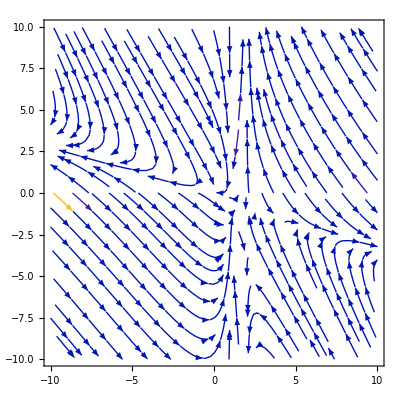

```mathematica
StreamPlot[{udotrhs,zdotrhs},{u,-10,10},{z,-10,10}]
```

```mathematica
dAdΧ=(Aprimerhs/Χprimerhs/.{A[r]->A[Χ],Χ[r]->Χ})//Simplify
```

(2 (1+λ) Χ^2 (-6+Χ+λ Χ)+Χ (6 (4+λ)-24 (1+λ) Χ+(1+λ) (-2+K (2+λ)) Χ^2) A[Χ]-2 (6-(23+6 λ) Χ+(-4+K (5+3 λ)) Χ^2) A[Χ]^2+(-24+(-6+K (14+3 λ)) Χ) A[Χ]^3-6 K A[Χ]^4)/(Χ (Χ (-6 λ-14 (1+λ) Χ+(1+λ) (-2+K (2+λ)) Χ^2)+2 Χ (16+3 λ+(4-K (5+3 λ)) Χ) A[Χ]+(-18+(-6+K (14+3 λ)) Χ) A[Χ]^2-6 K A[Χ]^3))

```mathematica
D[Υxy[[1]],x]//Simplify
D[Υxy[[2]],y]//Simplify
Bendixson=(D[Υxy[[1]],x]+D[Υxy[[2]],y])/.{K->1,λ->1}//Simplify
```

-1/(6 (-2 y+x (2+λ))^2)(12 y^3 (3+K y)+3 x^4 (2+3 λ+λ^2) (-2+K (2+λ))-4 x^3 (-4 y (3+2 λ)+7 (2+3 λ+λ^2)+K y (14+17 λ+5 λ^2))-4 x y (-6 λ+y (32+6 λ)+y^2 (-6+K (14+3 λ)))+x^2 (-6 λ (2+λ)+2 y (74+64 λ+3 λ^2)+y^2 (-6 (10+λ)+K (88+56 λ+3 λ^2))))

-1/(6 (-2 y+x (2+λ))^2)(12 y^2 (2+8 y+3 K y^2)+x^4 (2+3 λ+λ^2) (-2+K (2+λ))-4 x^3 (11+16 λ+5 λ^2+y (2+λ) (-4+5 K+3 K λ))-4 x y (6 (2+λ)+y (59+24 λ)+y^2 (-6+26 K+9 K λ))+x^2 (6 (4+2 λ+λ^2)+4 y (46+35 λ+6 λ^2)+y^2 (-52+104 K-18 λ+72 K λ+9 K λ^2)))

-(12 x^4-4 x^3 (37+14 y)+6 y^2 (2+11 y+4 y^2)-2 x y (12+121 y+40 y^2)+x^2 (12+315 y+98 y^2))/(3 (3 x-2 y)^2)

## Analysis

#### Moving fixed points

```mathematica
fixedpoint1=(Solve[Aprimerhs==0&&Χprimerhs==0,{Χ[r],A[r]}]//Simplify)[[1]];
fixedpoint2=(Solve[Aprimerhs==0&&Χprimerhs==0,{Χ[r],A[r]}]//Simplify)[[2]];
fixedpoint3=(Solve[Aprimerhs==0&&Χprimerhs==0,{Χ[r],A[r]}]//Simplify)[[3]];
fixedpoint4=(Solve[Aprimerhs==0&&Χprimerhs==0,{Χ[r],A[r]}]//Simplify)[[4]];
fixedpoint5=(Solve[Aprimerhs==0&&Χprimerhs==0,{Χ[r],A[r]}]//Simplify)[[5]];
fixedpoint6=(Solve[Aprimerhs==0&&Χprimerhs==0,{Χ[r],A[r]}]//Simplify)[[6]];
```

```mathematica
{fixedpoint1[[1]][[2]],fixedpoint1[[2]][[2]],fixedpoint2[[1]][[2]],fixedpoint2[[2]][[2]],fixedpoint3[[1]][[2]],fixedpoint3[[2]][[2]],fixedpoint4[[1]][[2]],fixedpoint4[[2]][[2]],fixedpoint5[[1]][[2]],fixedpoint5[[2]][[2]],fixedpoint6[[1]][[2]],fixedpoint6[[2]][[2]]}
```

{0,-(2+√(4-2 K))/K,0,(-2+√(4-2 K))/K,-(7-4 K+√((-1+K)^2 (4-9 λ+6 K λ)))/(5+λ+K^2 λ-2 K (1+λ)),-(-9+K^2 (-4+λ)+λ-2 √((-1+K)^2 (4-9 λ+6 K λ))+K (13-2 λ+√((-1+K)^2 (4-9 λ+6 K λ))))/((-1+K) (5+λ+K^2 λ-2 K (1+λ))),(-7+4 K+√((-1+K)^2 (4-9 λ+6 K λ)))/(5+λ+K^2 λ-2 K (1+λ)),-(-9+K^2 (-4+λ)+λ+2 √((-1+K)^2 (4-9 λ+6 K λ))-K (-13+2 λ+√((-1+K)^2 (4-9 λ+6 K λ))))/((-1+K) (5+λ+K^2 λ-2 K (1+λ))),-(2+2 λ+√2 √(-((-2+K) λ (1+λ))))/((1+λ) (2+K λ)),-(2+2 λ+√2 √(-((-2+K) λ (1+λ))))/(2+K λ),(-2-2 λ+√2 √(-((-2+K) λ (1+λ))))/((1+λ) (2+K λ)),(-2-2 λ+√2 √(-((-2+K) λ (1+λ))))/(2+K λ)}

```mathematica
{Listf1K,Listf2K,Listf3K,Listf4K,Listf5K,Listf6K}=Table[{},{6}];
For[n=0.1,n<2,n+=0.1,AppendTo[Listf1K,{(fixedpoint1/. {K->n})[[1]][[2]],(fixedpoint1/. {K->n})[[2]][[2]]}]]
For[n=0.1,n<2,n+=0.1,AppendTo[Listf2K,{(fixedpoint2/. {K->n})[[1]][[2]],(fixedpoint2/. {K->n})[[2]][[2]]}]]
For[n=0.1,n<2,n+=0.1,AppendTo[Listf3K,{(fixedpoint3/. {K->n})[[1]][[2]],(fixedpoint3/. {K->n})[[2]][[2]]}]]
For[n=0.1,n<2,n+=0.1,AppendTo[Listf4K,{(fixedpoint4/. {K->n})[[1]][[2]],(fixedpoint4/. {K->n})[[2]][[2]]}]]
For[n=0.1,n<2,n+=0.1,AppendTo[Listf5K,{(fixedpoint5/. {K->n})[[1]][[2]],(fixedpoint5/. {K->n})[[2]][[2]]}]]
For[n=0.1,n<2,n+=0.1,AppendTo[Listf6K,{(fixedpoint6/. {K->n})[[1]][[2]],(fixedpoint6/. {K->n})[[2]][[2]]}]]
```

```mathematica
{Listf1λ,Listf2λ,Listf3λ,Listf4λ,Listf5λ,Listf6λ}=Table[{},{6}];
For[n=0,n<100,n+=10,AppendTo[Listf1λ,{(fixedpoint1/. {λ->n})[[1]][[2]],(fixedpoint1/. {λ->n})[[2]][[2]]}]]
For[n=0,n<100,n+=10,AppendTo[Listf2λ,{(fixedpoint2/. {λ->n})[[1]][[2]],(fixedpoint2/. {λ->n})[[2]][[2]]}]]
For[n=0,n<100,n+=10,AppendTo[Listf3λ,{(fixedpoint3/. {λ->n})[[1]][[2]],(fixedpoint3/. {λ->n})[[2]][[2]]}]]
For[n=0,n<100,n+=10,AppendTo[Listf4λ,{(fixedpoint4/. {λ->n})[[1]][[2]],(fixedpoint4/. {λ->n})[[2]][[2]]}]]
For[n=0,n<100,n+=10,AppendTo[Listf5λ,{(fixedpoint5/. {λ->n})[[1]][[2]],(fixedpoint5/. {λ->n})[[2]][[2]]}]]
For[n=0,n<100,n+=10,AppendTo[Listf6λ,{(fixedpoint6/. {λ->n})[[1]][[2]],(fixedpoint6/. {λ->n})[[2]][[2]]}]]
```

```mathematica
Manipulate[Show[Plot[3 x/2,{x,-5,5},PlotStyle->White],Graphics[{Black,PointSize[0.01],Point[{0,-2+√2}]}],Graphics[{Black,PointSize[0.01],Point[{0,-2-√2}]}],Graphics[{Red,PointSize[0.01],Point/@{Listf1λ/.{K->i}}}],Graphics[{Orange,PointSize[0.01],Point/@{Listf2λ/.{K->i}}}],Graphics[{Yellow,PointSize[0.01],Point/@{Select[Listf3λ/.{K->i},Element[#,Reals]&]}}],
Graphics[{Green,PointSize[0.01],Point/@{Select[Listf4λ/.{K->i},Element[#,Reals]&]}}],
Graphics[{Blue,PointSize[0.01],Point/@{Select[Listf5λ/.{K->i},Element[#,Reals]&]}}],
Graphics[{Pink,PointSize[0.01],Point/@{Select[Listf6λ/.{K->i},Element[#,Reals]&]}}]],{i,0.01,2,0.01}]
```

```mathematica
Manipulate[Show[Plot[3 x/2,{x,-5,5},PlotStyle->White],Graphics[{Red,PointSize[0.01],Point/@{Listf1K}}],Graphics[{Orange,PointSize[0.01],Point/@{Listf2K}}],Graphics[{Yellow,PointSize[0.01],Point/@{Select[Listf3K/.{λ->i},Element[#,Reals]&]}}],Graphics[{Green,PointSize[0.01],Point/@{Select[Listf4K/.{λ->i},Element[#,Reals]&]}}],Graphics[{Blue,PointSize[0.01],Point/@{Select[Listf5K/.{λ->i},Element[#,Reals]&]}}],
Graphics[{Pink,PointSize[0.01],Point/@{Select[Listf6K/.{λ->i},Element[#,Reals]&]}}]],{i,0,10,0.01}]
```

```mathematica
Manipulate[Show[Plot[3 x/2,{x,-5,5},PlotStyle->White],Graphics[{Red,PointSize[0.01],Point[{fixedpoint1[[1]][[2]],fixedpoint1[[2]][[2]]/.{K->i}}]}],Graphics[{Orange,PointSize[0.01],Point[{fixedpoint2[[1]][[2]]/.{K->i,λ->j},fixedpoint2[[2]][[2]]/.{K->i}}]}],
Graphics[{Yellow,PointSize[0.01],Point[{fixedpoint3[[1]][[2]]/.{K->i,λ->j},fixedpoint3[[2]][[2]]/.{K->i,λ->j}}]}],
Graphics[{Green,PointSize[0.01],Point[{fixedpoint4[[1]][[2]]/.{K->i,λ->j},fixedpoint4[[2]][[2]]/.{K->i,λ->j}}]}],
Graphics[{Blue,PointSize[0.01],Point[{fixedpoint5[[1]][[2]]/.{K->i,λ->j},fixedpoint5[[2]][[2]]/.{K->i,λ->j}}]}],
Graphics[{Pink,PointSize[0.01],Point[{fixedpoint6[[1]][[2]]/.{K->i,λ->j},fixedpoint6[[2]][[2]]/.{K->i,λ->j}}]}]],{i,0.1,2,0.01},{j,0,100}]
```

```mathematica
Limit[{fixedpoint1[[1]][[2]],fixedpoint1[[2]][[2]]},{K->1,λ->1}]
Limit[{fixedpoint2[[1]][[2]],fixedpoint2[[2]][[2]]},{K->1,λ->1}]
Limit[{fixedpoint3[[1]][[2]],fixedpoint3[[2]][[2]]},{K->1,λ->1}]
Limit[{fixedpoint4[[1]][[2]],fixedpoint4[[2]][[2]]},{K->1,λ->1}]
Limit[{fixedpoint5[[1]][[2]],fixedpoint5[[2]][[2]]},{K->1,λ->1}]
Limit[{fixedpoint6[[1]][[2]],fixedpoint6[[2]][[2]]},{K->1,λ->1}]
```

{0,-2-√2}

{0,-2+√2}

{-1,Indeterminate}

{-1,Indeterminate}

{-1,-2}

{-1/3,-2/3}

```mathematica
Solve[(Aprimerhs==0/.{K->1,λ->1})&&(Χprimerhs==0/.{K->1,λ->1}),{A[r],Χ[r]}]//Simplify
```

{{A[r]→-2,Χ[r]→-1},{A[r]→-4/3,Χ[r]→-1},{A[r]→-2/3,Χ[r]→-1/3},{A[r]→-2-√2,Χ[r]→0},{A[r]→-2+√2,Χ[r]→0}}

#### Parametric plot of the fixed points

```mathematica
(*parametricplotfpoints=Show[ParametricPlot[{fixedpoint1[[1]][[2]],fixedpoint1[[2]][[2]]},{K,0,2},{λ,0,Infinity},PlotRange->{{-3,3},{-3,3}},BoundaryStyle->Directive[Red, Thick],PlotStyle->Red,ImageSize->Medium,PlotLegends->{"f_1"}],ParametricPlot[{fixedpoint2[[1]][[2]],fixedpoint2[[2]][[2]]},{K,0,2},{λ,0,Infinity},PlotRange->{{-3,3},{-3,3}},BoundaryStyle->Directive[Blue, Thick],PlotStyle->Blue,ImageSize->Medium,PlotLegends->{"f_2"}],
ParametricPlot[{fixedpoint3[[1]][[2]],fixedpoint3[[2]][[2]]},{K,0,2},{λ,0,Infinity},PlotRange->{{-3,3},{-3,3}},PlotStyle->RGBColor[77/255,175/255,74/255],BoundaryStyle->RGBColor[77/255,175/255,74/255],ImageSize->Medium,PlotLegends->{"f_3"}],
ParametricPlot[{fixedpoint4[[1]][[2]],fixedpoint4[[2]][[2]]},{K,0,2},{λ,0,Infinity},PlotRange->{{-3,3},{-3,3}},PlotStyle->RGBColor[152/255,78/255,163/255],BoundaryStyle->RGBColor[152/255,78/255,163/255],ImageSize->Medium,PlotLegends->{"f_4"}],
ParametricPlot[{fixedpoint5[[1]][[2]],fixedpoint5[[2]][[2]]},{K,0,2},{λ,0,Infinity},PlotRange->{{-3,3},{-3,3}},PlotStyle->RGBColor[255/255,127/255,0/255],BoundaryStyle->RGBColor[255/255,127/255,0/255],ImageSize->Medium,PlotLegends->{"f_5"}],
ParametricPlot[{fixedpoint6[[1]][[2]],fixedpoint6[[2]][[2]]},{K,0,2},{λ,0,Infinity},PlotRange->{{-3,3},{-3,3}},PlotStyle->RGBColor[255/255,255/255,51/255],BoundaryStyle->RGBColor[255/255,255/255,51/255],ImageSize->Medium,PlotLegends->{"f_6"}],Background->White,AxesLabel->{"",""}
]
Export["C:\\Users\\Aiver\\Documents\\4th Year\\Physics 199\\Final Thesis Tex\\figures\\parametricplotfpoints.pdf",parametricplotfpoints]*)
```

```mathematica
(*Show[ParametricPlot[{fixedpoint1[[1]][[2]],fixedpoint1[[2]][[2]]},{K,0,2},{λ,0,Infinity},PlotRange->{{-3,3},{-3,3}},BoundaryStyle->Directive[Red, Thick],PlotStyle->Red,ImageSize->Medium,PlotLegends->{"f_1"},FrameStyle->Directive[White,12]],ParametricPlot[{fixedpoint2[[1]][[2]],fixedpoint2[[2]][[2]]},{K,0,2},{λ,0,Infinity},PlotRange->{{-3,3},{-3,3}},BoundaryStyle->Directive[Blue, Thick],PlotStyle->Blue,ImageSize->Medium,PlotLegends->{"f_2"},FrameStyle->Directive[White,12]],
ParametricPlot[{fixedpoint3[[1]][[2]],fixedpoint3[[2]][[2]]},{K,0,2},{λ,0,Infinity},PlotRange->{{-3,3},{-3,3}},PlotStyle->RGBColor[77/255,175/255,74/255],BoundaryStyle->RGBColor[77/255,175/255,74/255],ImageSize->Medium,PlotLegends->{"f_3"},FrameStyle->Directive[White,12]],
ParametricPlot[{fixedpoint4[[1]][[2]],fixedpoint4[[2]][[2]]},{K,0,2},{λ,0,Infinity},PlotRange->{{-3,3},{-3,3}},PlotStyle->RGBColor[152/255,78/255,163/255],BoundaryStyle->RGBColor[152/255,78/255,163/255],ImageSize->Medium,PlotLegends->{"f_4"},FrameStyle->Directive[White,12]],
ParametricPlot[{fixedpoint5[[1]][[2]],fixedpoint5[[2]][[2]]},{K,0,2},{λ,0,Infinity},PlotRange->{{-3,3},{-3,3}},PlotStyle->RGBColor[255/255,127/255,0/255],BoundaryStyle->RGBColor[255/255,127/255,0/255],ImageSize->Medium,PlotLegends->{"f_5"},FrameStyle->Directive[White,12]],
ParametricPlot[{fixedpoint6[[1]][[2]],fixedpoint6[[2]][[2]]},{K,0,2},{λ,0,Infinity},PlotRange->{{-3,3},{-3,3}},PlotStyle->RGBColor[255/255,255/255,51/255],BoundaryStyle->RGBColor[255/255,255/255,51/255],ImageSize->Medium,PlotLegends->{"f_6"},FrameStyle->Directive[White,12]],Background->Black,AxesLabel->{Style["",White,12],Style["",White,12]}
]*)
```

```mathematica
(*parametricplotf1234=Show[ParametricPlot[{fixedpoint1[[1]][[2]],fixedpoint1[[2]][[2]]},{K,0,2},{λ,0,Infinity},PlotRange->{{-3,3},{-3,3}},BoundaryStyle->Directive[Red, Thick],PlotStyle->Red,ImageSize->Medium,PlotLegends->{"f_1"}],ParametricPlot[{fixedpoint2[[1]][[2]],fixedpoint2[[2]][[2]]},{K,0,2},{λ,0,Infinity},PlotRange->{{-3,3},{-3,3}},BoundaryStyle->Directive[Blue, Thick],PlotStyle->Blue,ImageSize->Medium,PlotLegends->{"f_2"}],
ParametricPlot[{fixedpoint3[[1]][[2]],fixedpoint3[[2]][[2]]},{K,0,2},{λ,0,Infinity},PlotRange->{{-3,3},{-3,3}},PlotStyle->RGBColor[77/255,175/255,74/255],BoundaryStyle->RGBColor[77/255,175/255,74/255],ImageSize->Medium,PlotLegends->{"f_3"}],
ParametricPlot[{fixedpoint4[[1]][[2]],fixedpoint4[[2]][[2]]},{K,0,2},{λ,0,Infinity},PlotRange->{{-3,3},{-3,3}},PlotStyle->RGBColor[152/255,78/255,163/255],BoundaryStyle->RGBColor[152/255,78/255,163/255],ImageSize->Medium,PlotLegends->{"f_4"}],Background->White,AxesLabel->{"",""}]
Export["C:\\Users\\Aiver\\Documents\\4th Year\\Physics 199\\Final Thesis Tex\\figures\\parametricplotf1234.pdf",parametricplotf1234]*)
```

```mathematica
(*Show[ParametricPlot[{fixedpoint1[[1]][[2]],fixedpoint1[[2]][[2]]},{K,0,2},{λ,0,Infinity},PlotRange->{{-3,3},{-3,3}},BoundaryStyle->Directive[Red, Thick],PlotStyle->Red,ImageSize->Medium,PlotLegends->{"f_1"},FrameStyle->Directive[White,12]],ParametricPlot[{fixedpoint2[[1]][[2]],fixedpoint2[[2]][[2]]},{K,0,2},{λ,0,Infinity},PlotRange->{{-3,3},{-3,3}},BoundaryStyle->Directive[Blue, Thick],PlotStyle->Blue,ImageSize->Medium,PlotLegends->{"f_2"},FrameStyle->Directive[White,12]],
ParametricPlot[{fixedpoint3[[1]][[2]],fixedpoint3[[2]][[2]]},{K,0,2},{λ,0,Infinity},PlotRange->{{-3,3},{-3,3}},PlotStyle->RGBColor[77/255,175/255,74/255],BoundaryStyle->RGBColor[77/255,175/255,74/255],ImageSize->Medium,PlotLegends->{"f_3"},FrameStyle->Directive[White,12]],
ParametricPlot[{fixedpoint4[[1]][[2]],fixedpoint4[[2]][[2]]},{K,0,2},{λ,0,Infinity},PlotRange->{{-3,3},{-3,3}},PlotStyle->RGBColor[152/255,78/255,163/255],BoundaryStyle->RGBColor[152/255,78/255,163/255],ImageSize->Medium,PlotLegends->{"f_4"},FrameStyle->Directive[White,12]],Background->Black,AxesLabel->{Style["",White,12],Style["",White,12]}
]*)
```

```mathematica
(*parametricplotf56=Show[ParametricPlot[{fixedpoint5[[1]][[2]],fixedpoint5[[2]][[2]]},{K,0,2},{λ,0,Infinity},PlotRange->{{-3,3},{-3,3}},PlotStyle->RGBColor[255/255,127/255,0/255],BoundaryStyle->RGBColor[255/255,127/255,0/255],ImageSize->Medium,PlotLegends->{"f_5"}],
ParametricPlot[{fixedpoint6[[1]][[2]],fixedpoint6[[2]][[2]]},{K,0,2},{λ,0,Infinity},PlotRange->{{-3,3},{-3,3}},PlotStyle->RGBColor[255/255,255/255,51/255],BoundaryStyle->RGBColor[255/255,255/255,51/255],ImageSize->Medium,PlotLegends->{"f_6"}],Background->White,AxesLabel->{"",""}]
Export["C:\\Users\\Aiver\\Documents\\4th Year\\Physics 199\\Final Thesis Tex\\figures\\parametricplotf56.pdf",parametricplotf56]*)
```

```mathematica
(*Show[
ParametricPlot[{fixedpoint5[[1]][[2]],fixedpoint5[[2]][[2]]},{K,0,2},{λ,0,Infinity},PlotRange->{{-3,3},{-3,3}},PlotStyle->RGBColor[255/255,127/255,0/255],BoundaryStyle->RGBColor[255/255,127/255,0/255],ImageSize->Medium,PlotLegends->{"f_5"},FrameStyle->Directive[White,12]],
ParametricPlot[{fixedpoint6[[1]][[2]],fixedpoint6[[2]][[2]]},{K,0,2},{λ,0,Infinity},PlotRange->{{-3,3},{-3,3}},PlotStyle->RGBColor[255/255,255/255,51/255],BoundaryStyle->RGBColor[255/255,255/255,51/255],ImageSize->Medium,PlotLegends->{"f_6"},FrameStyle->Directive[White,12]],Background->Black,AxesLabel->{Style["",White,12],Style["",White,12]}
]*)
```

### Analysis of each fixed point for arbitrary λ_s and K_B

```mathematica
JacobianY=(D[Υ,{{Χ[r],A[r]}}]//Simplify);
JacobianY//MatrixForm
```

((-12 K A[r]^4+4 A[r]^3 (-9+(-6+14 K+3 K λ) Χ[r])+A[r]^2 Χ[r] (8 (16+3 λ)+(6 (10+λ)-K (88+56 λ+3 λ^2)) Χ[r])+2 A[r] Χ[r] (-12 λ-(74+64 λ+3 λ^2) Χ[r]+2 (-12+14 K-8 λ+17 K λ+5 K λ^2) Χ[r]^2)-(2+λ) Χ[r]^2 (-6 λ-28 (1+λ) Χ[r]+3 (1+λ) (-2+K (2+λ)) Χ[r]^2))/(6 (-2 A[r]+(2+λ) Χ[r])^2) | (Χ[r] (-12 K A[r]^3-(2+λ) A[r] Χ[r] (-18+(-6+14 K+3 K λ) Χ[r])+2 A[r]^2 (-9+(-3+16 K+6 K λ) Χ[r])+Χ[r] (6 λ-(18+8 λ+3 λ^2) Χ[r]+2 (-3-λ+K (2+λ)^2) Χ[r]^2)))/(3 (-2 A[r]+(2+λ) Χ[r])^2)
((-6+8 K) A[r]^4-2 (2+3 λ+λ^2) Χ[r]^2 (-3+(1+λ) Χ[r])-2 A[r]^3 (-11+2 (-4+K (5+3 λ)) Χ[r])-(1+λ) A[r] Χ[r] (24-6 (5+3 λ) Χ[r]+(2+λ) (-2+K (2+λ)) Χ[r]^2)+2 A[r]^2 (6-24 (1+λ) Χ[r]+(-7-5 λ+K (8+10 λ+3 λ^2)) Χ[r]^2))/(3 (-2 A[r]+(2+λ) Χ[r])^2) | (-36 K A[r]^4+4 A[r]^3 (-24+(-6+K (26+9 λ)) Χ[r])-Χ[r]^2 (6 (4+2 λ+λ^2)-4 (11+16 λ+5 λ^2) Χ[r]+(2+3 λ+λ^2) (-2+K (2+λ)) Χ[r]^2)+4 (2+λ) A[r] Χ[r] (6-(23+6 λ) Χ[r]+(-4+K (5+3 λ)) Χ[r]^2)+A[r]^2 (-24+4 (59+24 λ) Χ[r]+(52+18 λ-K (104+72 λ+9 λ^2)) Χ[r]^2))/(6 (-2 A[r]+(2+λ) Χ[r])^2))

#### fixed point 1 : physical meaning

```mathematica
fixedpoint1
```

{Χ[r]→0,A[r]→-(2+√(4-2 K))/K}

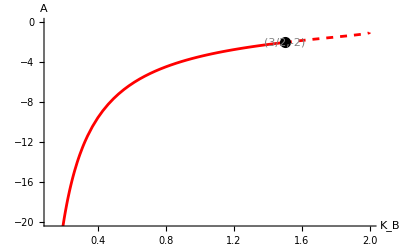

C:\Users\Aiver\Documents\4th Year\Physics 199\Final Thesis Tex\figures\bifurcationplotf1MOND.pdf

```mathematica
bifurcationplotf1MOND=Show[
Plot[-(2+√(4-2 K))/K,{K,0,3/2},PlotStyle->{Red}],
Plot[-(2+√(4-2 K))/K,{K,3/2,2},PlotStyle->{Red,Dashed}],
Graphics[{Black,PointSize[0.02],Point[{3/2,-2}],Gray,FontSize->12,Text["(3/2,-2)",{3/2,-2},{0,2}]}],
PlotRange->{All,{-20,0}},AxesOrigin->{0,0},AxesLabel->{Style["K_B",Black],Style["A",Black]},Background->White]

Export["C:\\Users\\Aiver\\Documents\\4th Year\\Physics 199\\Final Thesis Tex\\figures\\bifurcationplotf1MOND.pdf",bifurcationplotf1MOND]
```

Note that the fixed point stays negative for any value of K_B from 0 to 2. Therefore, this fixed point, f1, corresponds to a Minkowski spacetime for any K_B

```mathematica
(*Print[
"The scalar field solution at the fixed point (f_1) is ϕ(r) = ",ϕsolnf1Kλr=DSolve[r ϕ'[r]==fixedpoint1[[1]][[2]],ϕ[r],r][[1]][[1]][[2]],"\n",
"It's derivative is ϕ'(r) = ",ϕprimesolnf1Kλr=D[ϕsolnf1Kλr,r],"\n",
"The metric function α at the fixed point (f_1) is α(r) = ",αsolnf1Kλr=DSolve[r α'[r]==fixedpoint1[[2]][[2]],α[r],r][[1]][[1]][[2]],"\n",
"It's derivative is α'(r) = ",αprimesolnf1Kλr=D[αsolnf1Kλr,r],"\n",

"The value of γ upon substitution of α' and ϕ' at f3 is γ = ", gammanew[[1]][[2]]/.{α'[r]->αprimesolnf1Kλr,ϕ'[r]->ϕprimesolnf1Kλr}//Simplify
]*)
```

#### fixed point 1 : stability analysis

```mathematica
JacobianYf1=JacobianY/.fixedpoint1//Simplify;
```

```mathematica
λ1JacobianYf1=(Eigenvalues[JacobianYf1]//Simplify)[[1]];
λ2JacobianYf1=(Eigenvalues[JacobianYf1]//Simplify)[[2]];
```

```mathematica
v1JacobianYf1=(Eigenvectors[JacobianYf1]//Simplify)[[1]];
v2JacobianYf1=(Eigenvectors[JacobianYf1]//Simplify)[[2]];
```

```mathematica
Eigenvalues[JacobianYf1]//Simplify
```

{-(2+√(4-2 K)-2 K)/(2 K),(2 (-2-√(4-2 K)+K))/K}

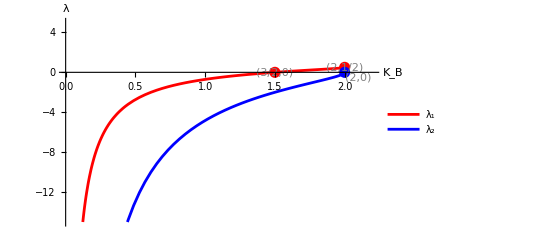

C:\Users\Aiver\Documents\4th Year\Physics 199\Mock Defense\plotf1eigenvalues.svg

```mathematica
plotf1eigenvalues=Show[Plot[{-(2+√(4-2 K)-2 K)/(2 K),(2 (-2-√(4-2 K)+K))/K},{K,0,2},AxesLabel->{Style["K_B",Black],Style["λ",Black]},PlotStyle->{Red,Blue},PlotRange->{{0,2.2},{-15,5}},PlotLegends->{Style["λ_1",Black],Style["λ_2",Black]},Background->White],Graphics[{Red,PointSize[0.02],Point[{3/2,0}],Gray,FontSize->12,Text["(3/2,0)",{3/2,0},{0,-2}]}],Graphics[{Red,PointSize[0.02],Point[{2,1/2}],Gray,FontSize->12,Text["(2,1/2)",{2,1/2},{0,-2}]}],
Graphics[{Blue,PointSize[0.02],Point[{2,0}],Gray,FontSize->12,Text["(2,0)",{2,0},{-1,3}]}]]

Export["C:\\Users\\Aiver\\Documents\\4th Year\\Physics 199\\Mock Defense\\plotf1eigenvalues.svg",plotf1eigenvalues,Background->None]
```

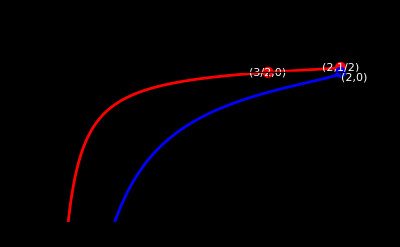

C:\Users\Aiver\Documents\4th Year\Physics 199\Mock Defense\plotf1eigenvalues.svg

```mathematica
plotf1eigenvalues=Show[Plot[{-(2+√(4-2 K)-2 K)/(2 K),(2 (-2-√(4-2 K)+K))/K},{K,0,2},AxesLabel->{Style["K_B",14,White],Style["λ",14,White]},PlotStyle->{Red,Blue},PlotRange->{{0,2.2},{-15,5}},Background->Black,AxesStyle->Directive[White,12,Thickness[0.003]]],Graphics[{Red,PointSize[0.02],Point[{3/2,0}],Gray,FontSize->12,Text[Style["(3/2,0)",White],{3/2,0},{0,-2}]}],Graphics[{Red,PointSize[0.02],Point[{2,1/2}],Gray,FontSize->12,Text[Style["(2,1/2)",White],{2,1/2},{0,-2}]}],
Graphics[{Blue,PointSize[0.02],Point[{2,0}],Gray,FontSize->12,Text[Style["(2,0)",White],{2,0},{-1,3}]}]]

Export["C:\\Users\\Aiver\\Documents\\4th Year\\Physics 199\\Mock Defense\\plotf1eigenvalues.svg",plotf1eigenvalues,Background->None]
```

```mathematica
(*Show[Plot[{-(2+√(4-2 K)-2 K)/(2 K),(2 (-2-√(4-2 K)+K))/K},{K,0,2},AxesLabel->{Style["K_B",Black],Style["λ",Black]},PlotStyle->{Red,Blue},PlotRange->{{0,2.2},{-15,5}},PlotLegends->{Style["λ_1",White],Style["λ_2",White]},Background->White],Graphics[{Red,PointSize[0.02],Point[{3/2,0}],White,FontSize->12,Text["(3/2,0)",{3/2,0},{0,-2}]}],Graphics[{Red,PointSize[0.02],Point[{2,1/2}],White,FontSize->12,Text["(2,1/2)",{2,1/2},{0,-2}]}],
Graphics[{Blue,PointSize[0.02],Point[{2,0}],White,FontSize->12,Text["(2,0)",{2,0},{-1,3}]}],FrameStyle->Directive[White,12],Background->Black,AxesLabel->{Style["K_B",White,12],Style["λ_i",White,12]},AxesStyle->White]*)
```

```mathematica
{-(2+√(4-2 K)-2 K)/(2 K),(2 (-2-√(4-2 K)+K))/K}/.K->3/2
```

{0,-2}

Since one eigenvalue is zero, this is a degenerate case where the node becomes a line of nodes.

```mathematica
Χprimef1=(JacobianYf1.{Χ[r],A[r]}//Simplify)[[1]];
Aprimef1=(JacobianYf1.{Χ[r],A[r]}//Simplify)[[2]]/.{A[r]->A[r]-fixedpoint1[[2]][[2]]}//Simplify;
```

```mathematica
JacobianYf1/.K->3/2//MatrixForm
Solve[-2/3 x-2(y+2)==0,y]
```

(0 | 0
-2/3 | -2)

{{y→1/3 (-6-x)}}

```mathematica
(*plotf1degenerate=Show[StreamPlot[{Χprimef1/.K->3/2,Aprimef1/.K->3/2},{Χ[r],-5,5},{A[r],-2-5,-2+5},FrameLabel->{Style["X(r̃)",Black],Style["A(r̃)",Black]},Background->White],Plot[1/3(-6-Χ[r]),{Χ[r],-5,5},PlotStyle->Red,PlotLegends->{""}],ImageSize->Medium]
Export["C:\\Users\\Aiver\\Documents\\4th Year\\Physics 199\\Final Thesis Tex\\figures\\f1degenerate.pdf",plotf1degenerate]*)
```

```mathematica
(*plotf1K95=Show[StreamPlot[{Χprimef1/.K->9/5,Aprimef1/.K->9/5},{Χ[r],-5,5},{A[r],-5/9 (2+√(2/5))-5,-5/9 (2+√(2/5))+5},FrameLabel->{Style["X(r̃)",Black],Style["A(r̃)",Black]},Background->White,PlotLabel->"K_B = 9/5"],
Graphics[{Red,PointSize[0.02],Point[{0,(fixedpoint1[[2]][[2]]/.K->9/5)/.K->9/5}],Black,FontSize->12,Text["(0,-1.46)",{0,-5/9 (2+√(2/5))},{1.2,1.3}]}]]
Export["C:\\Users\\Aiver\\Documents\\4th Year\\Physics 199\\Final Thesis Tex\\figures\\f1K95.pdf",plotf1K95]*)
```

#### fixed point 2: physical meaning

```mathematica
fixedpoint2
```

{Χ[r]→0,A[r]→(-2+√(4-2 K))/K}

```mathematica
gammanew[[1]][[2]]/.{α'[r]->αprimesolnatf2,ϕ'[r]->0}//Simplify
```

1/2 Log[1+2 r αprimesolnatf2+1/2 K r^2 αprimesolnatf2^2]

```mathematica
(*Print[
"The scalar field solution at the fixed point (f_1) is ϕ(r) = ",ϕsolnf2Kλr=DSolve[r ϕ'[r]==fixedpoint2[[1]][[2]],ϕ[r],r][[1]][[1]][[2]],"\n",
"It's derivative is ϕ'(r) = ",ϕprimesolnf2Kλr=D[ϕsolnf2Kλr,r],"\n",
"The metric function α at the fixed point (f_1) is α(r) = ",αsolnf2Kλr=DSolve[r α'[r]==fixedpoint2[[2]][[2]],α[r],r][[1]][[1]][[2]],"\n",
"It's derivative is α'(r) = ",αprimesolnf2Kλr=D[αsolnf2Kλr,r],"\n",

"The value of γ upon substitution of α' and ϕ' at f3 is γ = ", gammanew[[1]][[2]]/.{α'[r]->αprimesolnf2Kλr,ϕ'[r]->ϕprimesolnf2Kλr}//Simplify
]*)
```

#### fixed point 2: stability analysis

```mathematica
fixedpoint2
```

{Χ[r]→0,A[r]→(-2+√(4-2 K))/K}

```mathematica
JacobianYf2=JacobianY/.fixedpoint2//Simplify;
JacobianYf2//MatrixForm
λ1JacobianYf2=(Eigenvalues[JacobianYf2]//Simplify)[[1]];
λ2JacobianYf2=(Eigenvalues[JacobianYf2]//Simplify)[[2]];
```

((-2+√(4-2 K)+2 K)/(2 K) | 0
-1/3+(2 (-2+√(4-2 K)))/K^2+(16-5 √(4-2 K))/(6 K) | (2 (-2+√(4-2 K)+K))/K)

```mathematica
v1JacobianYf2=(Eigenvectors[JacobianYf2]//Simplify)[[1]];
v2JacobianYf2=(Eigenvectors[JacobianYf2]//Simplify)[[2]];
```

```mathematica
{Limit[(2 (-2+√(4-2 K)+K))/K,K->0],Limit[(-2+√(4-2 K)+2 K)/(2 K),K->0]}
```

{1,3/4}

```mathematica
plotf1eigenvalues=Show[Plot[{-(2+√(4-2 K)-2 K)/(2 K),(2 (-2-√(4-2 K)+K))/K},{K,0,2},AxesLabel->{Style["K_B",14,White],Style["λ",14,White]},PlotStyle->{Red,Blue},PlotRange->{{0,2.2},{-15,5}},Background->Black,AxesStyle->Directive[White,12,Thickness[0.003]]],Graphics[{Red,PointSize[0.02],Point[{3/2,0}],Gray,FontSize->12,Text[Style["(3/2,0)",White],{3/2,0},{0,-2}]}],Graphics[{Red,PointSize[0.02],Point[{2,1/2}],Gray,FontSize->12,Text[Style["(2,1/2)",White],{2,1/2},{0,-2}]}],
Graphics[{Blue,PointSize[0.02],Point[{2,0}],Gray,FontSize->12,Text[Style["(2,0)",White],{2,0},{-1,3}]}]]
```

-Graphics-

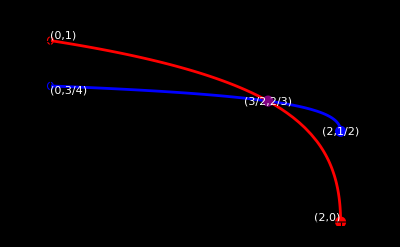

C:\Users\Aiver\Documents\4th Year\Physics 199\Mock Defense\f2eigenvalues.svg

```mathematica
plotf2eigenvalues=Show[Plot[{(2 (-2+√(4-2 K)+K))/K,(-2+√(4-2 K)+2 K)/(2 K)},{K,0,2},AxesLabel->{Style["K_B",14,White],Style["λ",14,White]},PlotStyle->{Red,Blue},PlotRange->{{0,2.2},{0,1.1}},Background->Black,AxesStyle->Directive[White,12,Thickness[0.003]]],
Graphics[{Purple,PointSize[0.02],Point[{3/2,2/3}],White,FontSize->12,Text["(3/2,2/3)",{3/2,2/3},{-1,-2}]}],
Graphics[{Blue,PointSize[0.02],Point[{2,1/2}],White,FontSize->12,Text["(2,1/2)",{2,1/2},{0,1.5}]}],
Graphics[{Red,PointSize[0.02],Point[{2,0}],White,FontSize->12,Text["(2,0)",{2,0},{1.2,-1.5}]}],
Graphics[{EdgeForm[Red],FaceForm[None],Disk[{0,1},0.02],White,FontSize->12,Text["(0,1)",{0,1},{-1.2,-1.5}]}],
Graphics[{EdgeForm[Blue],FaceForm[None],Disk[{0,3/4},0.02],White,FontSize->12,Text["(0,3/4)",{0,3/4},{-1.2,1.8}]}]]
Export["C:\\Users\\Aiver\\Documents\\4th Year\\Physics 199\\Mock Defense\\f2eigenvalues.svg",plotf2eigenvalues,Background->None]
```

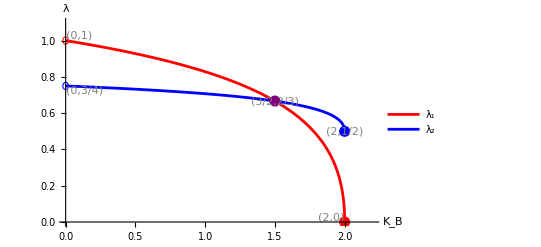

C:\Users\Aiver\Documents\4th Year\Physics 199\Final Thesis Tex\figures\plotf2eigenvalues.svg

```mathematica
plotf2eigenvalues=Show[Plot[{(2 (-2+√(4-2 K)+K))/K,(-2+√(4-2 K)+2 K)/(2 K)},{K,0,2},AxesLabel->{Style["K_B",Black],Style["λ",Black]},PlotStyle->{Red,Blue},PlotRange->{{0,2.2},{0,1.1}},PlotLegends->{Style["λ_1",Black],Style["λ_2",Black]},Background->White],
Graphics[{Purple,PointSize[0.02],Point[{3/2,2/3}],Gray,FontSize->12,Text["(3/2,2/3)",{3/2,2/3},{-1,-2}]}],
Graphics[{Blue,PointSize[0.02],Point[{2,1/2}],Gray,FontSize->12,Text["(2,1/2)",{2,1/2},{0,1.5}]}],
Graphics[{Red,PointSize[0.02],Point[{2,0}],Gray,FontSize->12,Text["(2,0)",{2,0},{1.2,-1.5}]}],
Graphics[{EdgeForm[Red],FaceForm[None],Disk[{0,1},0.02],Gray,FontSize->12,Text["(0,1)",{0,1},{-1.2,-1.5}]}],
Graphics[{EdgeForm[Blue],FaceForm[None],Disk[{0,3/4},0.02],Gray,FontSize->12,Text["(0,3/4)",{0,3/4},{-1.2,1.8}]}]]

Export["C:\\Users\\Aiver\\Documents\\4th Year\\Physics 199\\Final Thesis Tex\\figures\\plotf2eigenvalues.svg",plotf2eigenvalues]
```

```mathematica
(*Show[Plot[{(2 (-2+√(4-2 K)+K))/K,(-2+√(4-2 K)+2 K)/(2 K)},{K,0,2},AxesLabel->{Style["K_B",Black],Style["λ",Black]},PlotStyle->{Red,Blue},PlotRange->{{0,2.2},{0,1.1}},PlotLegends->{Style["λ_1",White],Style["λ_2",White]},Background->None],Graphics[{Purple,PointSize[0.02],Point[{3/2,2/3}],White,FontSize->12,Text["(3/2,2/3)",{3/2,2/3},{-1,-2}]}],
Graphics[{Blue,PointSize[0.02],Point[{2,1/2}],White,FontSize->12,Text["(2,1/2)",{2,1/2},{0,1.5}]}],
Graphics[{Red,PointSize[0.02],Point[{2,0}],White,FontSize->12,Text["(2,0)",{2,0},{1.2,-1.5}]}],
Graphics[{EdgeForm[Red],FaceForm[None],Disk[{0,1},0.02],White,FontSize->12,Text["(0,1)",{0,1},{-1.2,-1.5}]}],
Graphics[{EdgeForm[Blue],FaceForm[None],Disk[{0,3/4},0.02],White,FontSize->12,Text["(0,3/4)",{0,3/4},{-1.2,1.8}]}],Background->Black,AxesLabel->{Style["K_B",White,12],Style["λ_i",White,12]},AxesStyle->Directive[White,12]]*)
```

```mathematica
(*af2=(JacobianYf2/.K->3/2)[[1]][[1]];
bf2=(JacobianYf2/.K->3/2)[[1]][[2]];
cf2=(JacobianYf2/.K->3/2)[[2]][[1]];
df2=(JacobianYf2/.K->3/2)[[2]][[2]];
pf2=af2+df2;
qf2=af2 df2-bf2 cf2;
Print["Δ = ",pf2^2-4 qf2]*)
```

The discriminant equalling to zero means that this is a degenerate case where the eigenvalues are equal given by λ = p/2/. This corresponds to a case where the two asymptote s have converged.

```mathematica
Χprimef2=(JacobianYf2.{Χ[r],A[r]}//Simplify)[[1]]/.{A[r]->A[r]-fixedpoint2[[2]][[2]]}//Simplify;
Aprimef2=(JacobianYf2.{Χ[r],A[r]}//Simplify)[[2]]/.{A[r]->A[r]-fixedpoint2[[2]][[2]]}//Simplify;
```

```mathematica
(*plotdegeneratef2=Show[StreamPlot[{Χprimef2/.K->3/2,Aprimef2/.K->3/2},{Χ[r],-5,5},{A[r],-2/3-5,-2/3+5},FrameLabel->{Style["X(r̃)",Black],Style["A(r̃)",Black]},Background->White],Graphics[{Red,PointSize[0.02],Point[{0,fixedpoint2[[2]][[2]]/.K->3/2}],Black,FontSize->12,Text["(0,-2/3)",{0,-2/3},{1,1}]}],ImageSize->Medium]
Export["C:\\Users\\Aiver\\Documents\\4th Year\\Physics 199\\Final Thesis Tex\\figures\\f2degenerate.pdf",plotdegeneratef2]*)
```

```mathematica
(*plotf2K95=Show[StreamPlot[{Χprimef2/.K->9/5,Aprimef2/.K->9/5},{Χ[r],-5,5},{A[r],5/9 (-2+√(2/5))-5,5/9 (-2+√(2/5))+5},FrameLabel->{Style["X(r̃)",Black],Style["A(r̃)",Black]},Background->White,PlotLabel->"K_B = 9/5"],
Graphics[{Red,PointSize[0.02],Point[{0,(fixedpoint2[[2]][[2]]/.K->9/5)/.K->9/5}],Black,FontSize->12,Text["(0,-0.76)",{0,5/9 (-2+√(2/5))},{1.2,1.3}]}]]
Export["C:\\Users\\Aiver\\Documents\\4th Year\\Physics 199\\Final Thesis Tex\\figures\\f2K95.pdf",plotf2K95]*)
```

#### fixed point 3: physical meaning

```mathematica
fixedpoint3
```

{Χ[r]→-(7-4 K+√((-1+K)^2 (4-9 λ+6 K λ)))/(5+λ+K^2 λ-2 K (1+λ)),A[r]→-(-9+K^2 (-4+λ)+λ-2 √((-1+K)^2 (4-9 λ+6 K λ))+K (13-2 λ+√((-1+K)^2 (4-9 λ+6 K λ))))/((-1+K) (5+λ+K^2 λ-2 K (1+λ)))}

```mathematica
(*ϕsolnf3Kλr=DSolve[r ϕ'[r]==fixedpoint3[[1]][[2]],ϕ[r],r][[1]][[1]][[2]]
ϕprimesolnf3Kλr=D[ϕsolnf3Kλr,r]*)
```

```mathematica
(*αsolnf3Kλr=DSolve[r α'[r]==fixedpoint3[[2]][[2]],α[r],r][[1]][[1]][[2]]
αprimesolnf3Kλr=D[αsolnf3Kλr,r]*)
```

```mathematica
Limit[-(7-4 K+√((-1+K)^2 (4-9 λ+6 K λ)))/(5+λ+K^2 λ-2 K (1+λ)),{λ->Infinity,K->0}]
```

0

```mathematica
(*X3=ContourPlot[fixedpoint3[[1]][[2]],{K,0,2},{λ,0,Infinity},Contours->Function[{min,max},Range[min,max,0.1]],PlotLegends->Automatic,FrameLabel->{Style["K_B",Black],Style["λ_s",Black]},Background->White]
Export["C:\\Users\\Aiver\\Documents\\4th Year\\Physics 199\\Final Thesis Tex\\figures\\X3.pdf",X3]*)
```

```mathematica
(*A3=ContourPlot[fixedpoint3[[2]][[2]],{K,0,2},{λ,0,Infinity},Contours->Function[{min,max},Range[min,max,0.1]],PlotLegends->Automatic,FrameLabel->{Style["K_B",Black],Style["λ_s",Black]},Background->White]
Export["C:\\Users\\Aiver\\Documents\\4th Year\\Physics 199\\Final Thesis Tex\\figures\\A3.pdf",A3]*)
```

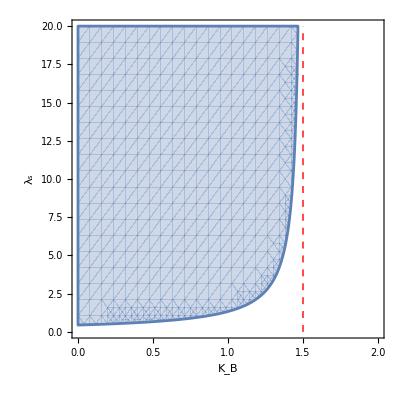

C:\Users\Aiver\Documents\4th Year\Physics 199\Final Thesis Tex\figures\Radicalineq.pdf

```mathematica
Radicalineq=Show[RegionPlot[-4/(3 (-3+2 K))<λ,{K,0,3/2},{λ,0,20},PlotRange->{{0,2},{0,20}}, FrameLabel->{Style["K_B",Black,14],Style["λ_s",Black,14]},FrameStyle->Black,FrameTicksStyle->14,PlotLegends->{Style["",Black,14]}],
Graphics[{Red,Dashed,Line[{{3/2,0},{3/2,20}}]}],Background->White]

Export["C:\\Users\\Aiver\\Documents\\4th Year\\Physics 199\\Final Thesis Tex\\figures\\Radicalineq.pdf",Radicalineq]
```

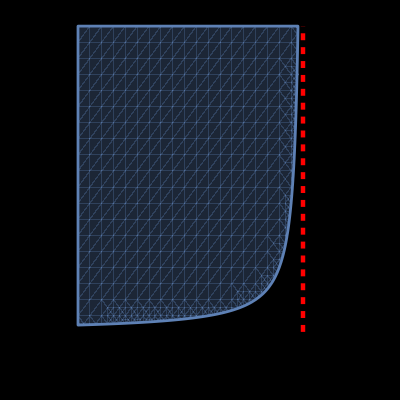

C:\Users\Aiver\Documents\4th Year\Physics 199\Mock Defense\Radicalineqblack.svg

```mathematica
Radicalineqblack=Show[RegionPlot[-4/(3 (-3+2 K))<λ,{K,0,3/2},{λ,0,20},PlotRange->{{0,2},{0,20}}, FrameLabel->{Style["K_B",White,14],Style["λ_s",White,14]},FrameStyle->White,FrameTicksStyle->Directive[14,White]],
Graphics[{Red,Directive[Dashed,Thickness[0.008]],Line[{{3/2,0},{3/2,20}}]}],Background->Black]

Export["C:\\Users\\Aiver\\Documents\\4th Year\\Physics 199\\Mock Defense\\Radicalineqblack.svg",Radicalineqblack,Background->None]
```

#### fixed point 3: stability analysis

```mathematica
JacobianYf3=JacobianY/.fixedpoint3;
λ1JacobianYf3=Eigenvalues[JacobianYf3][[1]];
λ2JacobianYf3=Eigenvalues[JacobianYf3][[2]];
```

```mathematica
v1JacobianYf3=(Eigenvectors[JacobianYf3]//Simplify)[[1]];
v2JacobianYf3=(Eigenvectors[JacobianYf3]//Simplify)[[2]];
```

```mathematica
(*f3eigenvaluesplot=Show[
Plot3D[Module[{val=λ1JacobianYf3/. {λ->1}},If[Element[val,Reals],val,Indeterminate]],{K,0,2},{λ,0,10},PlotStyle->Orange,WorkingPrecision->70],
Plot3D[Module[{val=λ2JacobianYf3/. {λ->1}},If[Element[val,Reals],val,Indeterminate]],{K,0,2},{λ,0,10},PlotStyle->Green,WorkingPrecision->70],,AxesLabel->{Style[Subscript[K, B],12,White],Style[Subscript[λ, s],12,White],Style[λ,12,White]},Background->Black,AxesStyle->White,BoxStyle->White
]*)
```

```mathematica
τf3=Tr[JacobianYf3]//Simplify;
```

```mathematica
τf3
```

-(((-1+K) (4+(-9+6 K) λ) (3 K^4 (16-7 λ) λ^2-5 λ^3+4 K^5 λ^3-28 (2+√((-1+K)^2 (4-9 λ+6 K λ)))+6 λ^2 (15+2 √((-1+K)^2 (4-9 λ+6 K λ)))-3 λ (-5+8 √((-1+K)^2 (4-9 λ+6 K λ)))+K^3 λ (24+44 λ^2-9 λ (25+√((-1+K)^2 (4-9 λ+6 K λ))))-2 K^2 (8+23 λ^3+3 λ (7+3 √((-1+K)^2 (4-9 λ+6 K λ)))-3 λ^2 (66+5 √((-1+K)^2 (4-9 λ+6 K λ))))+K (3 λ+24 λ^3+39 λ √((-1+K)^2 (4-9 λ+6 K λ))+8 (9+√((-1+K)^2 (4-9 λ+6 K λ)))-3 λ^2 (103+11 √((-1+K)^2 (4-9 λ+6 K λ))))))/((5+λ+K^2 λ-2 K (1+λ)) (4 K+6 K^2 λ-2 (2+√((-1+K)^2 (4-9 λ+6 K λ)))+λ (9+√((-1+K)^2 (4-9 λ+6 K λ)))-K λ (15+√((-1+K)^2 (4-9 λ+6 K λ))))^2))

```mathematica
Δf3=Det[JacobianYf3]//Simplify;
```

```mathematica
(*Plot3D[{fixedpoint3[[1]][[2]],fixedpoint3[[2]][[2]]},{K,0,2},{λ,0,Infinity},PlotStyle->{Blue,Red},AxesLabel->{Style[Subscript[K,B],12,White],Style[Subscript[λ,s],12,White],Style["λ",12,White]},Background->Black,AxesStyle->White,BoxStyle->White]*)
```

```mathematica
(*Plot3D[{Module[{val=(τf3+√(τf3^2-4Δf3))/2},If[Element[val,Reals],val,Indeterminate]],Module[{val=(τf3-√(τf3^2-4Δf3))/2},If[Element[val,Reals],val,Indeterminate]]},{K,0,2},{λ,0,Infinity},PlotStyle->{Green,Orange,Gray},AxesLabel->{Style[Subscript[K,B],12,White],Style[Subscript[λ,s],12,White],Style["λ",12,White]},Background->Black,AxesStyle->White,BoxStyle->White,WorkingPrecision->70]*)
```

```mathematica
(*Show[

Plot3D[{fixedpoint3[[1]][[2]],fixedpoint3[[2]][[2]]},{K,0,2},{λ,0,Infinity},PlotStyle->{Blue,Red},PerformanceGoal->"Quality"],
Plot3D[{Module[{val=(τf3+√(τf3^2-4Δf3))/2},If[Element[val,Reals],val,Indeterminate]],Module[{val=(τf3-√(τf3^2-4Δf3))/2},If[Element[val,Reals],val,Indeterminate]]},{K,0,2},{λ,0,Infinity},PlotStyle->{Green,Orange},PerformanceGoal->"Quality",WorkingPrecision->70],
AxesLabel->{Style[Subscript[K,B],12,White],Style[Subscript[λ,s],12,White],Style["λ",12,White]},Background->Black,AxesStyle->White,BoxStyle->White
]*)
```

```mathematica
λ1f3unscreened=Limit[(τf3+√(τf3^2-4Δf3))/2,λ->0,Assumptions->0<K<2]//Simplify
λ2f3unscreened=Limit[(τf3-√(τf3^2-4Δf3))/2,λ->0,Assumptions->0<K<2]//Simplify
```

((-1+K) (-7+2 K))/((1+√((-1+K)^2)-K) (-5+2 K))+(√((109+60 √((-1+K)^2)-(201+64 √((-1+K)^2)) K+16 (7+√((-1+K)^2)) K^2-20 K^3)/((5-2 K)^2 (1+√((-1+K)^2)-K))))/(√2)

((-1+K) (-7+2 K))/((1+√((-1+K)^2)-K) (-5+2 K))-(√((109+60 √((-1+K)^2)-(201+64 √((-1+K)^2)) K+16 (7+√((-1+K)^2)) K^2-20 K^3)/((5-2 K)^2 (1+√((-1+K)^2)-K))))/(√2)

```mathematica
(*Limit[(τf3+√(τf3^2-4Δf3))/2,λ->Infinity,Assumptions->0<K<2]*)
```

-Graphics-

-Graphics-

```mathematica
λf3screened=(3-2 K)/(-1+K);
(*when Subscript[K, B] >= 1 for Subscript[λ, 1]*)
(*when Subscript[K, B] < 1 for Subscript[λ, 2]*)
```

```mathematica
(*Show[
Plot[{Piecewise[{{-2,K<1},{λf3screened,K>=1}}],Piecewise[{{-2,K>=1},{λf3screened,K<1}}]},{K,0,2},AxesLabel->{"K_B","λ"},PlotStyle->{Orange,Green}],

Plot[{λ1f3unscreened,λ2f3unscreened},{K,0,2},PlotStyle->{Orange,Directive[Green,Dashing[0.02]]}],

PlotRange->{All,{-5,0.6}}
,AxesLabel->{Style["K_B",14,White],Style["λ",14,White]},Background->Black,AxesStyle->Directive[White,12,Thickness[0.003]]
]*)
```

```mathematica
λ2f3λ1=Limit[(τf3-√(τf3^2-4Δf3))/2,λ->1,Assumptions->0<K<2]//Simplify
```

ConditionalExpression[-(((-5+6 K) (-44+254 K-502 K^2+449 K^3-184 K^4+23 K^5+4 K^6+√(-5+6 K) (40-54 K+2 K^2+21 K^3-9 K^4) Abs[-1+K]+√2 √((-1+K)^3 (-1192+6880 K-9096 K^2-1876 K^3+9034 K^4-3852 K^5-80 K^6+179 K^7+3 K^8+√(-5+6 K) (416+840 K-3372 K^2+968 K^3+612 K^4-174 K^5-15 K^6) Abs[-1+K]))))/(2 (6-4 K+K^2) (-5+11 K-6 K^2+(1+K) √(-5+6 K) Abs[-1+K])^2)), K>5/6]

```mathematica
(*f3eigenvalues=GraphicsGrid[
{{Show[Plot[ Module[{val=λ1JacobianYf3/. {λ->1}},If[Element[val,Reals],val,Indeterminate]],{K,0,2},PlotStyle->Red,PlotRange->{{0,2},{-2.1,1/2}},WorkingPrecision->70,AxesLabel->{Style["K_B",Black,12],Style["λ",Black,12]}],
Plot[ Module[{val=λ2JacobianYf3/. {λ->1}},If[Element[val,Reals],val,Indeterminate]],{K,0,2},PlotStyle->Blue,PlotRange->{{0,2},{-2.1,1/2}},WorkingPrecision->70,AxesLabel->{Style["K_B",Black,12],Style["λ",Black,12]}],PlotLabel->Style["",Black,12]],
Show[Plot[ Module[{val=λ1JacobianYf3/. {λ->2}},If[Element[val,Reals],val,Indeterminate]],{K,0,2},PlotStyle->Red,PlotRange->{{0,2},{-2.1,1/2}},WorkingPrecision->50,AxesLabel->{Style["K_B",Black,12],Style["λ",Black,12]}],
Plot[ Module[{val=λ2JacobianYf3/. {λ->2}},If[Element[val,Reals],val,Indeterminate]],{K,0,2},PlotStyle->Blue,PlotRange->{{0,2},{-2.1,1/2}},WorkingPrecision->50,AxesLabel->{Style["K_B",Black,12],Style["λ",Black,12]}],PlotLabel->Style["",Black,12]]},
{Show[Plot[Module[{val=λ1JacobianYf3/. {λ->5}},If[Element[val,Reals],val,Indeterminate]],{K,0,2},PlotStyle->Red,PlotRange->{{0,2},{-2.1,1/2}},WorkingPrecision->50,AxesLabel->{Style["K_B",Black,12],Style["λ",Black,12]}],
Plot[Module[{val=λ2JacobianYf3/. {λ->5}},If[Element[val,Reals],val,Indeterminate]],{K,0,2},PlotStyle->Blue,PlotRange->{{0,2},{-2.1,1/2}},WorkingPrecision->50,AxesLabel->{Style["K_B",Black,12],Style["λ",Black,12]}],PlotLabel->Style["",Black,12]],
Show[Plot[ Module[{val=λ1JacobianYf3/. {λ->10}},If[Element[val,Reals],val,Indeterminate]],{K,0,2},PlotStyle->Red,PlotRange->{{0,2},{-2.1,1/2}},WorkingPrecision->50,AxesLabel->{Style["K_B",Black,12],Style["λ",Black,12]}],
Plot[Module[{val=λ2JacobianYf3/. {λ->10}},If[Element[val,Reals],val,Indeterminate]],{K,0,2},PlotStyle->Blue,PlotRange->{{0,2},{-2.1,1/2}},WorkingPrecision->50,AxesLabel->{Style["K_B",Black,12],Style["λ",Black,12]}],PlotLabel->Style["",Black,12]]}},
Frame->False]

Export["C:\\Users\\Aiver\\Documents\\4th Year\\Physics 199\\Final Thesis Tex\\figures\\f3eigenvalues.pdf",f3eigenvalues,Background->None]*)
```

```mathematica
(*f3eigenvaluesplot=Show[
Plot[ {Module[{val=λ1JacobianYf3/. {λ->1}},If[Element[val,Reals],val,Indeterminate]],
 Module[{val=λ1JacobianYf3/. {λ->2}},If[Element[val,Reals],val,Indeterminate]],
Module[{val=λ1JacobianYf3/. {λ->10}},If[Element[val,Reals],val,Indeterminate]]},
{K,0,2},Filling->Axis,PlotStyle->{Directive[Orange,Dashing[0.02]],Directive[Red,Dashing[0.02]],Directive[Yellow,Dashing[0.02]]},PlotRange->{{0,2},{-2.1,1/2}},WorkingPrecision->70],

Plot[ {Module[{val=λ2JacobianYf3/. {λ->1}},If[Element[val,Reals],val,Indeterminate]], 
Module[{val=λ2JacobianYf3/. {λ->2}},If[Element[val,Reals],val,Indeterminate]],
Module[{val=λ2JacobianYf3/. {λ->10}},If[Element[val,Reals],val,Indeterminate]]
},
{K,0,2},PlotStyle->{Green,Blue, Cyan},PlotRange->{{0,2},{-2.1,1/2}},WorkingPrecision->70],

PlotRange->{All,{-2.5,0.6}}
,AxesLabel->{Style["K_B",14,White],Style["λ",14,White]},Background->Black,AxesStyle->Directive[White,12,Thickness[0.003]]
]

Export["C:\\Users\\Aiver\\Documents\\4th Year\\Physics 199\\Mock Defense\\f3eigenvaluesplot.svg",f3eigenvaluesplot,Background->None]*)
```

```mathematica
(*Show[
Plot[{Piecewise[{{-2,K<1},{λf3screened,K>=1}}],Piecewise[{{-2,K>=1},{λf3screened,K<1}}]},{K,0,2},AxesLabel->{"K_B","λ"},PlotStyle->{Orange,Green}],

Plot[{λ1f3unscreened,λ2f3unscreened},{K,0,2},PlotStyle->{Orange,Directive[Green,Dashing[0.02]]}],

PlotRange->{All,{-5,0.6}}
,AxesLabel->{Style["K_B",14,White],Style["λ",14,White]},Background->Black,AxesStyle->Directive[White,12,Thickness[0.003]]
]*)
```

#### fixed point 4: physical meaning

```mathematica
fixedpoint4
```

{Χ[r]→(-7+4 K+√((-1+K)^2 (4-9 λ+6 K λ)))/(5+λ+K^2 λ-2 K (1+λ)),A[r]→-(-9+K^2 (-4+λ)+λ+2 √((-1+K)^2 (4-9 λ+6 K λ))-K (-13+2 λ+√((-1+K)^2 (4-9 λ+6 K λ))))/((-1+K) (5+λ+K^2 λ-2 K (1+λ)))}

```mathematica
fixedpoint4[[1]][[2]]==(-7+4 K+√((-1+K)^2 (4-9 λ+6 K λ)))/(5+λ+K^2 λ-2 K (1+λ))
```

True

```mathematica
ϕsolnf4Kλr=DSolve[r ϕ'[r]==fixedpoint4[[1]][[2]],ϕ[r],r][[1]][[1]][[2]]
ϕprimesolnf4Kλr=D[ϕsolnf4Kλr,r]
```

C[1]+((-7+4 K+√((-1+K)^2 (4-9 λ+6 K λ))) Log[r])/(5+λ+K^2 λ-2 K (1+λ))

(-7+4 K+√((-1+K)^2 (4-9 λ+6 K λ)))/(r (5+λ+K^2 λ-2 K (1+λ)))

```mathematica
αsolnf4Kλr=DSolve[r α'[r]==fixedpoint4[[2]][[2]],α[r],r][[1]][[1]][[2]]
αprimesolnf4Kλr=D[αsolnf4Kλr,r]
```

C[1]-((-9+K^2 (-4+λ)+λ+2 √((-1+K)^2 (4-9 λ+6 K λ))-K (-13+2 λ+√((-1+K)^2 (4-9 λ+6 K λ)))) Log[r])/((-1+K) (5+λ+K^2 λ-2 K (1+λ)))

-(-9+K^2 (-4+λ)+λ+2 √((-1+K)^2 (4-9 λ+6 K λ))-K (-13+2 λ+√((-1+K)^2 (4-9 λ+6 K λ))))/((-1+K) r (5+λ+K^2 λ-2 K (1+λ)))

```mathematica
(*coefofαf4=ContourPlot[-((-9+K^2 (-4+λ)+λ+2 √((-1+K)^2 (4-9 λ+6 K λ))-K (-13+2 λ+√((-1+K)^2 (4-9 λ+6 K λ)))) /((-1+K) (5+λ+K^2 λ-2 K (1+λ)))),{K,0,2},{λ,0,Infinity},Contours->Function[{min,max},Range[min,max,0.1]],PlotLegends->Automatic,FrameLabel->{Style["",Black],Style["",Black]},Background->White]
Export["C:\\Users\\Aiver\\Documents\\4th Year\\Physics 199\\Final Thesis Tex\\figures\\coefofαf4.pdf",coefofαf4]*)
```

```mathematica
(*coefofϕf4=ContourPlot[(-7+4 K+√((-1+K)^2 (4-9 λ+6 K λ)))/(5+λ+K^2 λ-2 K (1+λ)),{K,0,2},{λ,0,Infinity},Contours->Function[{min,max},Range[min,max,0.1]],PlotLegends->Automatic,FrameLabel->{Style["",Black],Style["",Black]},Background->White]
Export["C:\\Users\\Aiver\\Documents\\4th Year\\Physics 199\\Final Thesis Tex\\figures\\coefofϕf4.pdf",coefofϕf4]*)
```

```mathematica
(*Print[
"The value of γ upon substitution of α' and ϕ' is γ = ",gammanew[[1]][[2]]/.{α'[r]->αprimesolnf4Kλr,ϕ'[r]->ϕprimesolnf4Kλr}//Simplify]*)
```

#### fixed point 4: stability analysis

```mathematica
JacobianYf4=JacobianY/.fixedpoint4;
```

```mathematica
λ1JacobianYf4=Eigenvalues[JacobianYf4][[1]];
λ2JacobianYf4=Eigenvalues[JacobianYf4][[2]];
```

```mathematica
v1JacobianYf4=(Eigenvectors[JacobianYf4]//Simplify)[[1]];
v2JacobianYf4=(Eigenvectors[JacobianYf4]//Simplify)[[2]];
```

```mathematica
τf4=Tr[JacobianYf4]//Simplify;
Δf4=Det[JacobianYf4]//Simplify;
```

```mathematica
(*f4eigenvalues=GraphicsGrid[
{{Show[Plot[ Module[{val=λ1JacobianYf4/. {λ->1}},If[Element[val,Reals],val,Indeterminate]],{K,0,2},PlotStyle->Red,PlotRange->{{0,2},{-2.1,1/2}},WorkingPrecision->50,AxesLabel->{Style["K_B",Black,12],Style["λ",Black,12]}],
Plot[ Module[{val=λ2JacobianYf4/. {λ->1}},If[Element[val,Reals],val,Indeterminate]],{K,0,2},PlotStyle->Blue,PlotRange->{{0,2},{-2.1,1/2}},WorkingPrecision->50,AxesLabel->{Style["K_B",Black,12],Style["λ",Black,12]}],PlotLabel->Style["",Black,12]],
Show[Plot[ Module[{val=λ1JacobianYf4/. {λ->2}},If[Element[val,Reals],val,Indeterminate]],{K,0,2},PlotStyle->Red,PlotRange->{{0,2},{-2.1,1/2}},WorkingPrecision->50,AxesLabel->{Style["K_B",Black,12],Style["λ",Black,12]}],
Plot[ Module[{val=λ2JacobianYf4/. {λ->2}},If[Element[val,Reals],val,Indeterminate]],{K,0,2},PlotStyle->Blue,PlotRange->{{0,2},{-2.1,1/2}},WorkingPrecision->50,AxesLabel->{Style["K_B",Black,12],Style["λ",Black,12]}],PlotLabel->Style["",Black,12]]},
{Show[Plot[Module[{val=λ1JacobianYf4/. {λ->5}},If[Element[val,Reals],val,Indeterminate]],{K,0,2},PlotStyle->Red,PlotRange->{{0,2},{-2.1,1/2}},WorkingPrecision->50,AxesLabel->{Style["K_B",Black,12],Style["λ",Black,12]}],
Plot[Module[{val=λ2JacobianYf4/. {λ->5}},If[Element[val,Reals],val,Indeterminate]],{K,0,2},PlotStyle->Blue,PlotRange->{{0,2},{-2.1,1/2}},WorkingPrecision->50,AxesLabel->{Style["K_B",Black,12],Style["λ",Black,12]}],PlotLabel->Style["",Black,12]],
Show[Plot[ Module[{val=λ1JacobianYf4/. {λ->10}},If[Element[val,Reals],val,Indeterminate]],{K,0,2},PlotStyle->Red,PlotRange->{{0,2},{-2.1,1/2}},WorkingPrecision->50,AxesLabel->{Style["K_B",Black,12],Style["λ",Black,12]}],
Plot[Module[{val=λ2JacobianYf4/. {λ->10}},If[Element[val,Reals],val,Indeterminate]],{K,0,2},PlotStyle->Blue,PlotRange->{{0,2},{-2.1,1/2}},WorkingPrecision->50,AxesLabel->{Style["K_B",Black,12],Style["λ",Black,12]}],PlotLabel->Style["",Black,12]]}},
Frame->False]
Export["C:\\Users\\Aiver\\Documents\\4th Year\\Physics 199\\Final Thesis Tex\\figures\\f4eigenvalues.pdf",f4eigenvalues]*)
```

```mathematica
(*Plot3D[{fixedpoint4[[1]][[2]],fixedpoint4[[2]][[2]]},{K,0,2},{λ,0,Infinity},PlotStyle->{Blue,Red},AxesLabel->{Style[Subscript[K,B],12,White],Style[Subscript[λ,s],12,White],Style["λ",12,White]},Background->Black,AxesStyle->White,BoxStyle->White]*)
```

```mathematica
(*Show[Plot3D[{Module[{val=(τf4+√(τf4^2-4Δf4))/2},If[Element[val,Reals],val,Indeterminate]],
Module[{val=(τf4-√(τf4^2-4Δf4))/2},If[Element[val,Reals],val,Indeterminate]]},{K,0,2},{λ,0,Infinity},PlotStyle->{Directive[Green],Directive[Orange]},WorkingPrecision->70,
AxesLabel->{Style["K_B",12,White],Style["λ_s",12,White],Style["λ",12,White]},Background->Black,AxesStyle->White,BoxStyle->White],PerformanceGoal->"Quality"]*)
```

```mathematica
(*Show[

Plot3D[{fixedpoint4[[1]][[2]],fixedpoint4[[2]][[2]]},{K,0,2},{λ,0,Infinity},PlotStyle->{Blue,Red},PerformanceGoal->"Quality"],
Plot3D[{Module[{val=(τf4+√(τf4^2-4Δf4))/2},If[Element[val,Reals],val,Indeterminate]],Module[{val=(τf4-√(τf4^2-4Δf4))/2},If[Element[val,Reals],val,Indeterminate]]},{K,0,2},{λ,0,Infinity},PlotStyle->{Green,Orange},PerformanceGoal->"Quality",WorkingPrecision->70],
AxesLabel->{Style[Subscript[K,B],12,White],Style[Subscript[λ,s],12,White],Style["λ",12,White]},Background->Black,AxesStyle->White,BoxStyle->White
]*)
```

```mathematica
λ1f4unscreened=Limit[(τf4+√(τf4^2-4Δf4))/2,λ->0,Assumptions->0<K<2]//Simplify
λ2f4unscreened=Limit[(τf4-√(τf4^2-4Δf4))/2,λ->0,Assumptions->0<K<2]//Simplify
```

-((-1+K) (-7+2 K))/((-1+√((-1+K)^2)+K) (-5+2 K))+(√((-109+60 √((-1+K)^2)+(201-64 √((-1+K)^2)) K+16 (-7+√((-1+K)^2)) K^2+20 K^3)/((5-2 K)^2 (-1+√((-1+K)^2)+K))))/(√2)

-((-1+K) (-7+2 K))/((-1+√((-1+K)^2)+K) (-5+2 K))-(√((-109+60 √((-1+K)^2)+(201-64 √((-1+K)^2)) K+16 (-7+√((-1+K)^2)) K^2+20 K^3)/((5-2 K)^2 (-1+√((-1+K)^2)+K))))/(√2)

```mathematica
(*Limit[(τf4+√(τf4^2-4Δf4))/2,λ->Infinity,Assumptions->0<K<2]*)
```

-Graphics-

```mathematica
(*Limit[(τf4-√(τf4^2-4Δf4))/2,λ->Infinity,Assumptions->0<K<2]*)
```

-Graphics-

```mathematica
(*Show[
Plot[{λ1f4unscreened,λ2f4unscreened},{K,0,2},PlotStyle->{Orange,Directive[Green,Dashing[0.02]]}],
Plot[{Piecewise[{{-2,K<1},{λf3screened,K>=1}}],Piecewise[{{-2,K>=1},{λf3screened,K<1}}]},{K,0,2},AxesLabel->{"K_B","λ"},PlotStyle->{Orange,Green}],

PlotRange->{All,{-5,0.6}}
,AxesLabel->{Style["K_B",14,White],Style["λ",14,White]},Background->Black,AxesStyle->Directive[White,12,Thickness[0.003]]
]*)
```

```mathematica
(*f4eigenvaluesplot=Show[
Plot[ {Module[{val=λ1JacobianYf4/. {λ->1}},If[Element[val,Reals],val,Indeterminate]],
 Module[{val=λ1JacobianYf4/. {λ->2}},If[Element[val,Reals],val,Indeterminate]],
Module[{val=λ1JacobianYf4/. {λ->10}},If[Element[val,Reals],val,Indeterminate]]},
{K,0,2},Filling->Axis,PlotStyle->{Directive[Orange,Dashing[0.02]],Directive[Red,Dashing[0.02]],Directive[Yellow,Dashing[0.02]]},PlotRange->{{0,2},{-2.1,1/2}},WorkingPrecision->70],

Plot[ {Module[{val=λ2JacobianYf4/. {λ->1}},If[Element[val,Reals],val,Indeterminate]], 
Module[{val=λ2JacobianYf4/. {λ->2}},If[Element[val,Reals],val,Indeterminate]],
Module[{val=λ2JacobianYf4/. {λ->10}},If[Element[val,Reals],val,Indeterminate]]
},
{K,0,2},PlotStyle->{Green,Blue, Cyan},PlotRange->{{0,2},{-2.1,1/2}},WorkingPrecision->70],

PlotRange->{All,{-2.5,0.6}}
,AxesLabel->{Style["K_B",14,White],Style["λ",14,White]},Background->Black,AxesStyle->Directive[White,12,Thickness[0.003]]
]

Export["C:\\Users\\Aiver\\Documents\\4th Year\\Physics 199\\Mock Defense\\f4eigenvaluesplot.svg",f4eigenvaluesplot,Background->None]*)
```

#### fixed point 5: physical meaning

```mathematica
fixedpoint5
```

{Χ[r]→-(2+2 λ+√2 √(-((-2+K) λ (1+λ))))/((1+λ) (2+K λ)),A[r]→-(2+2 λ+√2 √(-((-2+K) λ (1+λ))))/(2+K λ)}

```mathematica
(*bifurcationplotf3linear=
Show[
Plot[fixedpoint3[[1]][[2]]/. {λ->0},{K,0,2},PlotStyle->Black,PlotLegends->{"λ_s = 0"}],
Plot[fixedpoint3[[1]][[2]]/. {λ->1},{K,0,2},PlotStyle->{RGBColor[27/255,158/255,119/255]},PlotLegends->{Style["λ_s = 1",Black]}],
Plot[fixedpoint3[[1]][[2]]/. {λ->2},{K,0,2},PlotStyle->{RGBColor[217/255,95/255,2/255]},PlotLegends->{"λ_s = 2"}],
Plot[fixedpoint3[[1]][[2]]/. {λ->5},{K,0,2/25},PlotStyle->{RGBColor[117/255,112/255,179/255],Dashed}],
Plot[fixedpoint3[[1]][[2]]/. {λ->5},{K,2/25,2},PlotStyle->{RGBColor[117/255,112/255,179/255]},PlotLegends->{"λ_s = 5"}],
Graphics[{Black,PointSize[0.02],Point/@{{2/25,-5/12}}/.{K->1,λ->1}}],
Plot[fixedpoint3[[1]][[2]]/. {λ->10},{K,0,28/25},PlotStyle->{RGBColor[231/255,41/255,138/255],Dashed}],
Plot[fixedpoint3[[1]][[2]]/. {λ->10},{K,28/25,2},PlotStyle->RGBColor[231/255,41/255,138/255],PlotLegends->{"λ_s = 10"}],
Graphics[{Black,PointSize[0.02],Point/@{{28/25,-5/11}}/.{K->1,λ->1}}],
Plot[fixedpoint3[[1]][[2]]/. {λ->100},{K,0,2},PlotStyle->{RGBColor[102/255,166/255,30/255],Dashed},PlotLegends->{"λ_s = 100"}],
Plot[0,{K,0,2},PlotStyle->{Gray,Dashed},PlotLegends->{"λ_s = ∞ "}],
PlotRange->{All,{-4,1}},AxesOrigin->{0,0},AxesLabel->{Style["K_B",Black],Style["X",Black]},Background->White]


Export["C:\\Users\\Aiver\\Documents\\4th Year\\Physics 199\\Final Thesis Tex\\figures\\bifurcationplotf3linear.pdf",bifurcationplotf3linear]*)
```

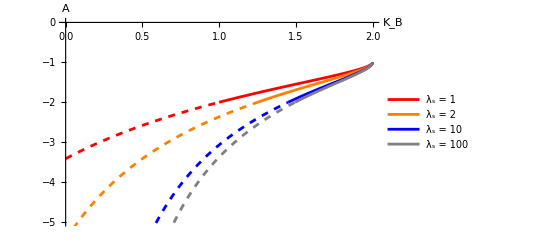

C:\Users\Aiver\Documents\4th Year\Physics 199\Final Thesis Tex\figures\bifurcationplotf5Alinear.pdf

```mathematica
bifurcationplotf5Alinear=Show[Plot[{fixedpoint5[[2]][[2]]/.{λ->1}},{K,0,1},PlotStyle->{{Red,Dashed}}],
Plot[{fixedpoint5[[2]][[2]]/.{λ->1}},{K,1,2},PlotStyle->{{Red}},PlotLegends->{"λ_s = 1"}],
Plot[{fixedpoint5[[2]][[2]]/.{λ->2}},{K,0,5/4},PlotStyle->{{Orange,Dashed}}],
Plot[{fixedpoint5[[2]][[2]]/.{λ->2}},{K,5/4,2},PlotStyle->{{Orange}},PlotLegends->{"λ_s = 2"}],
Plot[{fixedpoint5[[2]][[2]]/.{λ->10}},{K,0,29/20},PlotStyle->{{Blue,Dashed}}],
Plot[{fixedpoint5[[2]][[2]]/.{λ->10}},{K,29/20,2},PlotStyle->{{Blue}},PlotLegends->{"λ_s = 10"}],
Plot[{fixedpoint5[[2]][[2]]/.{λ->100}},{K,0,299/200},PlotStyle->{{Gray,Dashed}}],
Plot[{fixedpoint5[[2]][[2]]/.{λ->100}},{K,299/200,2},PlotStyle->{{Gray}},PlotLegends->{"λ_s = 100"}],AxesOrigin->{0,0},PlotRange->{All,{-5,0}},AxesLabel->{Style["K_B",Black],Style["A",Black]},Background->White]

Export["C:\\Users\\Aiver\\Documents\\4th Year\\Physics 199\\Final Thesis Tex\\figures\\bifurcationplotf5Alinear.pdf",bifurcationplotf5Alinear]
```

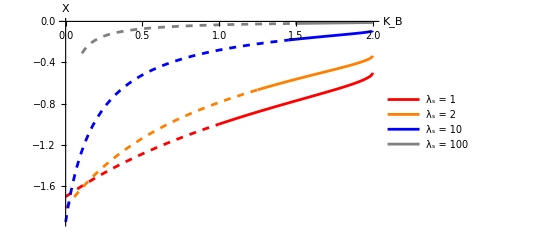

C:\Users\Aiver\Documents\4th Year\Physics 199\Final Thesis Tex\figures\bifurcationplotf5Xlinear.pdf

```mathematica
bifurcationplotf5Xlinear=Show[Plot[{fixedpoint5[[1]][[2]]/.{λ->1}},{K,0,1},PlotStyle->{{Red,Dashed}}],
Plot[{fixedpoint5[[1]][[2]]/.{λ->1}},{K,1,2},PlotStyle->{{Red}},PlotLegends->{"λ_s = 1"}],
Plot[{fixedpoint5[[1]][[2]]/.{λ->2}},{K,0,5/4},PlotStyle->{{Orange,Dashed}}],
Plot[{fixedpoint5[[1]][[2]]/.{λ->2}},{K,5/4,2},PlotStyle->{{Orange}},PlotLegends->{"λ_s = 2"}],
Plot[{fixedpoint5[[1]][[2]]/.{λ->10}},{K,0,29/20},PlotStyle->{{Blue,Dashed}}],
Plot[{fixedpoint5[[1]][[2]]/.{λ->10}},{K,29/20,2},PlotStyle->{{Blue}},PlotLegends->{"λ_s = 10"}],
Plot[{fixedpoint5[[1]][[2]]/.{λ->100}},{K,0,299/200},PlotStyle->{{Gray,Dashed}}],
Plot[{fixedpoint5[[1]][[2]]/.{λ->100}},{K,299/200,2},PlotStyle->{{Gray}},PlotLegends->{"λ_s = 100"}],AxesOrigin->{0,0},PlotRange->Full,AxesLabel->{Style["K_B",Black],Style["X",Black]},Background->White]

Export["C:\\Users\\Aiver\\Documents\\4th Year\\Physics 199\\Final Thesis Tex\\figures\\bifurcationplotf5Xlinear.pdf",bifurcationplotf5Xlinear]
```

```mathematica
(*ϕsolnf5Kλr=DSolve[r ϕ'[r]==fixedpoint5[[1]][[2]],ϕ[r],r][[1]][[1]][[2]]
ϕprimesolnf5Kλr=D[ϕsolnf5Kλr,r]*)
```

```mathematica
(*αsolnf5Kλr=DSolve[r α'[r]==fixedpoint5[[2]][[2]],α[r],r][[1]][[1]][[2]]
αprimesolnf5Kλr=D[αsolnf5Kλr,r]*)
```

```mathematica
(*Print[
"The value of γ upon evalution at α' and ϕ' is γ = ", gammanew[[1]][[2]]/.{α'[r]->αprimesolnf5Kλr,ϕ'[r]->ϕprimesolnf5Kλr}//Simplify]*)
```

```mathematica
(*coefofϕf5=ContourPlot[fixedpoint5[[1]][[2]],{K,0,2},{λ,0,Infinity},Contours->Function[{min,max},Range[min,max,0.1]],PlotLegends->Automatic,FrameLabel->{Style["",Black],Style["",Black]},Background->White]
Export["C:\\Users\\Aiver\\Documents\\4th Year\\Physics 199\\Final Thesis Tex\\figures\\coefofϕf5.pdf",coefofϕf5]*)
```

```mathematica
(*coefofαf5=ContourPlot[fixedpoint5[[2]][[2]],{K,0,2},{λ,0,Infinity},Contours->Function[{min,max},Range[min,max,0.1]],PlotLegends->Automatic,FrameLabel->{Style["",Black],Style["",Black]},Background->White]
Export["C:\\Users\\Aiver\\Documents\\4th Year\\Physics 199\\Final Thesis Tex\\figures\\coefofαf5.pdf",coefofαf5]*)
```

#### fixed point 5: stability analysis

```mathematica
JacobianYf5=JacobianY/.fixedpoint5//Simplify;
```

```mathematica
λ1JacobianYf5=(Eigenvalues[JacobianYf5]//Simplify)[[1]];
λ2JacobianYf5=(Eigenvalues[JacobianYf5]//Simplify)[[2]];
```

```mathematica
v1JacobianYf5=(Eigenvectors[JacobianYf5]//Simplify)[[1]];
v2JacobianYf5=(Eigenvectors[JacobianYf5]//Simplify)[[2]];
```

```mathematica
(*Simplify[Series[λ1JacobianYf5,{λ,Infinity,2}],Assumptions->{λ>0}]*)
```

```mathematica
(*Simplify[Series[λ2JacobianYf5,{λ,Infinity,1}],Assumptions->{λ>0}]*)
```

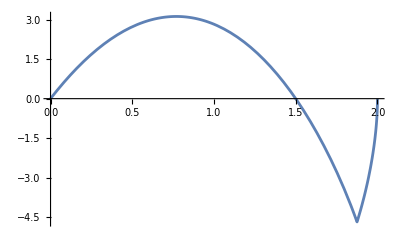

```mathematica
Plot[-((2+√(4-2 K)) K)+√2 √(K^2 (18 (2+√(4-2 K))-3 (11+4 √(4-2 K)) K+8 K^2)),{K,0,2}]
```

```mathematica
(*Simplify[Series[λ1JacobianYf3,{λ,Infinity,1}],Assumptions->{λ>0}]*)
```

```mathematica
(*Simplify[Series[λ2JacobianYf3,{λ,Infinity,1}],Assumptions->{λ>0}]*)
```

```mathematica
(*Simplify[Series[λ1JacobianYf4,{λ,Infinity,1}],Assumptions->{λ>0}]*)
```

```mathematica
(*Simplify[Series[λ2JacobianYf4,{λ,Infinity,1}],Assumptions->{λ>0}]*)
```

```mathematica
(*{λ1JacobianYf5λs1,λ2JacobianYf5λs1}={Limit[λ1JacobianYf5,λ->1],Limit[λ2JacobianYf5,λ->1]}*)
```

```mathematica
(*{λ1JacobianYf5λs1,λ2JacobianYf5λs1}/.K->9/5//N*)
```

```mathematica
(*Show[Plot3D[λ1JacobianYf5,{K,0,2},{λ,0,10},PlotStyle->Orange,AxesLabel->{Style[Subscript[K, B],Bold,White],Style[Subscript[λ, s],Bold,White],Style[λ,Bold,White]},Background->Black,AxesStyle->White,BoxStyle->White],Plot3D[λ2JacobianYf5,{K,0,2},{λ,0,10},PlotStyle->Green,Background->Black,AxesStyle->White,BoxStyle->White],Plot3D[0,{K,0,2},{λ,0,10},PlotStyle->Gray,Background->Black,AxesStyle->White,BoxStyle->White],PlotRange->Full]*)
```

```mathematica
(*λ1JacobianYf5screened=Limit[λ1JacobianYf5,λ->Infinity];
λ2JacobianYf5screened=Limit[λ2JacobianYf5,λ->Infinity];*)
```

```mathematica
(*Limit[λ2JacobianYf5,λ->0]*)
```

```mathematica
(*Solve[λ2JacobianYf5==0/.{λ->2},K]*)
```

```mathematica
(*eigenvaluesf5MOND=
Show[
Plot[{λ1JacobianYf5/.λ->1,λ1JacobianYf5/.λ->2,λ1JacobianYf5/.λ->10,λ1JacobianYf5screened},{K,0,2},PlotStyle->{Gray,RGBColor[254/255,204/255,92/255],RGBColor[253/255,141/255,60/255],
RGBColor[189/255,0/255,38/255]},PlotLegends->{"λ_1 , λ_s = 1"," λ_1 , λ_s= 2"," λ_1 , λ_s= 10"," λ_1 , λ_s= ∞"},Background->White],
Plot[{λ2JacobianYf5/.λ->1,λ2JacobianYf5/.λ->2,λ2JacobianYf5/.λ->10,λ2JacobianYf5screened},{K,0,2},PlotStyle->{Black,RGBColor[161/255,218/255,180/255],RGBColor[65/255,182/255,196/255],
RGBColor[34/255,94/255,168/255]},PlotLegends->{"λ_2 , λ_s = 1"," λ_2 , λ_s= 2"," λ_2 , λ_s= 10"," λ_2 , λ_s= ∞"},Background->White],PlotRange->{All,{-6,5}}
,AxesLabel->{Style["K_B",Black,12],Style["",Black,12]}]

Export["C:\\Users\\Aiver\\Documents\\4th Year\\Physics 199\\Final Thesis Tex\\figures\\eigenvaluesf5MOND.pdf",eigenvaluesf5MOND]*)
```

```mathematica
(*Show[Plot[{(2 (-2+√(4-2 K)+K))/K,(-2+√(4-2 K)+2 K)/(2 K)},{K,0,2},AxesLabel->{Style["K_B",14,White],Style["λ",14,White]},PlotStyle->{Red,Blue},PlotRange->{{0,2.2},{0,1.1}},Background->Black,AxesStyle->Directive[White,12,Thickness[0.003]]],
Graphics[{Purple,PointSize[0.02],Point[{3/2,2/3}],White,FontSize->12,Text["(3/2,2/3)",{3/2,2/3},{-1,-2}]}],
Graphics[{Blue,PointSize[0.02],Point[{2,1/2}],White,FontSize->12,Text["(2,1/2)",{2,1/2},{0,1.5}]}],
Graphics[{Red,PointSize[0.02],Point[{2,0}],White,FontSize->12,Text["(2,0)",{2,0},{1.2,-1.5}]}],
Graphics[{EdgeForm[Red],FaceForm[None],Disk[{0,1},0.02],White,FontSize->12,Text["(0,1)",{0,1},{-1.2,-1.5}]}],
Graphics[{EdgeForm[Blue],FaceForm[None],Disk[{0,3/4},0.02],White,FontSize->12,Text["(0,3/4)",{0,3/4},{-1.2,1.8}]}]]*)
```

```mathematica
(*f5eigenvaluesplot=
Show[
Plot[{λ1JacobianYf5/.λ->1,λ1JacobianYf5screened},{K,0,2},PlotStyle->{Orange,Directive[Orange,Dashing[0.02]]},Filling->{1->{2}}],
Plot[{λ2JacobianYf5/.λ->1,λ2JacobianYf5screened},{K,0,2},PlotStyle->{Green,Directive[Green,Dashing[0.02]]},Filling->{1->{2}}],PlotRange->{All,{-6,5}}
,AxesLabel->{Style["K_B",14,White],Style["λ",14,White]},AxesStyle->Directive[White,12,Thickness[0.003]],Background->Black]

Export["C:\\Users\\Aiver\\Documents\\4th Year\\Physics 199\\Mock Defense\\f5eigenvaluesplot.svg",f5eigenvaluesplot,Background->None]*)
```

#### fixed point 6: physical meaning

```mathematica
fixedpoint6
```

{Χ[r]→(-2-2 λ+√2 √(-((-2+K) λ (1+λ))))/((1+λ) (2+K λ)),A[r]→(-2-2 λ+√2 √(-((-2+K) λ (1+λ))))/(2+K λ)}

```mathematica
ϕsolnf6Kλr=DSolve[r ϕ'[r]==fixedpoint6[[1]][[2]],ϕ[r],r][[1]][[1]][[2]]
ϕprimesolnf6Kλr=D[ϕsolnf6Kλr,r]
```

C[1]+((-2-2 λ+√2 √(-((-2+K) λ (1+λ)))) Log[r])/((1+λ) (2+K λ))

(-2-2 λ+√2 √(-((-2+K) λ (1+λ))))/(r (1+λ) (2+K λ))

```mathematica
αsolnf6Kλr=DSolve[r α'[r]==fixedpoint6[[2]][[2]],α[r],r][[1]][[1]][[2]]
αprimesolnf6Kλr=D[αsolnf6Kλr,r]
```

C[1]+((-2-2 λ+√2 √(-((-2+K) λ (1+λ)))) Log[r])/(2+K λ)

(-2-2 λ+√2 √(-((-2+K) λ (1+λ))))/(r (2+K λ))

```mathematica
(*Print[
"The value of γ upon evalution at α' and ϕ' is γ = ", gammanew[[1]][[2]]/.{α'[r]->αprimesolnf6Kλr,ϕ'[r]->ϕprimesolnf6Kλr}//Simplify]*)
```

#### fixed point 6: stability analysis

```mathematica
JacobianYf6=JacobianY/.fixedpoint6//Simplify;
```

```mathematica
λ1JacobianYf6=(Eigenvalues[JacobianYf6]//Simplify)[[1]];
λ2JacobianYf6=(Eigenvalues[JacobianYf6]//Simplify)[[2]];
```

```mathematica
v1JacobianYf6=(Eigenvectors[JacobianYf6]//Simplify)[[1]];
v2JacobianYf6=(Eigenvectors[JacobianYf6]//Simplify)[[2]];
```

```mathematica
λ1JacobianYf6screened=Limit[λ1JacobianYf6,λ->Infinity];
λ2JacobianYf6screened=Limit[λ2JacobianYf6,λ->Infinity];
```

```mathematica
(*{λ1JacobianYf6λsinf,λ2JacobianYf6λsinf}={Limit[λ1JacobianYf6,λ->Infinity],Limit[λ2JacobianYf6,λ->Infinity]}*)
```

```mathematica
(*Show[
Plot[{λ1JacobianYf6/.λ->1,λ1JacobianYf6/.λ->10,λ1JacobianYf6/.λ->100},{K,0,2},PlotStyle->{Gray,Red, Green, Blue},PlotLegends->{"λ_1 , λ_s = 1"," λ_1 , λ_s= 10"," λ_1 , λ_s= 100"},Background->White],
Plot[{λ2JacobianYf6/.λ->1,λ2JacobianYf6/.λ->10,λ2JacobianYf6/.λ->100},{K,0,2},PlotStyle->{Black,Orange,Magenta,Yellow},PlotLegends->{"λ_2 , λ_s = 1"," λ_2 , λ_s= 10"," λ_2 , λ_s= 100"},Background->White],PlotRange->{All,{-2,1}}
,AxesLabel->{Style["K_B",Black,12],Style["",Black,12]}]*)
```

```mathematica
(*f6eigenvaluesplot=Show[
Plot[{λ1JacobianYf6/.λ->1,λ1JacobianYf6screened},{K,0,2},Filling->{1->{2}},PlotStyle->{Orange,Directive[Orange, Dashing[0.02]]}],
Plot[{λ2JacobianYf6/.λ->1,λ2JacobianYf6screened},{K,0,2},Filling->{1->{2}},PlotStyle->{Blue, Directive[Blue, Dashing[0.02]]}],PlotRange->{All,{-2,1}},AxesOrigin->{0,0}
,AxesLabel->{Style["K_B",14,White],Style["λ",14,White]},AxesStyle->Directive[White,12,Thickness[0.003]],Background->Black]

Export["C:\\Users\\Aiver\\Documents\\4th Year\\Physics 199\\Mock Defense\\f6eigenvaluesplot.svg",f6eigenvaluesplot,Background->None]*)
```

```mathematica
(*Plot3D[{λ1JacobianYf6,λ2JacobianYf6},{K,0,2},{λ,0,Infinity},AxesLabel->{Style["K_B",White,Bold],Style["λ_s",Black,Bold],Style["λ_i",Black,Bold]},Background->White,AxesStyle->Black,BoxStyle->Black,PlotStyle->{Blue,Orange}]*)
```

```mathematica
λ1JacobianYf1
```

-(2+√(4-2 K)-2 K)/(2 K)

### Linear solutions general

#### f_1 linear solutions

```mathematica
ϕ1linearsolnKBλs=DSolve[C[1]v1JacobianYf1[[1]] ⅇ^((λ1JacobianYf1)*Log[r/r0])+ C[2]v2JacobianYf1[[1]] ⅇ^(λ2JacobianYf1*Log[r/r0])==r ϕ'[r],ϕ[r],r][[1]][[1]]
α1linearsolnKBλs=DSolve[C[1]v1JacobianYf1[[2]] ⅇ^((λ1JacobianYf1)*Log[r/r0])+ C[2]v2JacobianYf1[[2]] ⅇ^(λ2JacobianYf1*Log[r/r0])==r α'[r],α[r],r][[1]][[1]]
```

ϕ[r]→-(6 (6+3 √(4-2 K)-2 K) K^2 r (r/r0)^(-(2+√(4-2 K))/(2 K)) C[1])/((2+√(4-2 K)-2 K) (-12 (2+√(4-2 K))+(16+5 √(4-2 K)) K-2 K^2) r0)+C[2]

α[r]→(-(2 K r (r/r0)^(-(2+√(4-2 K))/(2 K)) r0 C[1])/(2+√(4-2 K)-2 K)-(K r^2 (r/r0)^(-(2 (2+√(4-2 K)))/K) C[2])/(2 (2+√(4-2 K)-K)))/r0^2+C[3]

```mathematica
gammanew[[1]][[2]]/.{α->Function[{r},α1linearsolnKBλs[[2]]],ϕ->Function[{r},ϕ1linearsolnKBλs[[2]]]}
```

0

```mathematica
Limit[ϕ1linearsolnKBλs[[2]],r->Infinity,Assumptions->{r0>0,0<K<2,λ>0}]
```

ConditionalExpression[-∞, C[2]∈ℝ&&2+√(4-2 K)<2 K&&C[1]>0]

```mathematica
Limit[-Exp[2*α1linearsolnKBλs[[2]]],r->Infinity,Assumptions->{r0>0,0<K<2,λ>0}]
```

ConditionalExpression[-∞, (C[2]|C[3])∈ℝ&&2+√(4-2 K)<2 K&&C[1]>0]

#### f_2 linear solutions

```mathematica
ϕ2linearsolnKBλs=DSolve[C[1]v1JacobianYf2[[1]] ⅇ^((λ1JacobianYf2)*Log[r/r0])+ C[2]v2JacobianYf2[[1]] ⅇ^(λ2JacobianYf2*Log[r/r0])==r ϕ'[r],ϕ[r],r][[1]][[1]]
α2linearsolnKBλs=DSolve[C[1]v1JacobianYf2[[2]] ⅇ^((λ1JacobianYf2)*Log[r/r0])+ C[2]v2JacobianYf2[[2]] ⅇ^(λ2JacobianYf2*Log[r/r0])==r α'[r],α[r],r][[1]][[1]]
```

ϕ[r]→(6 K^2 (-6+3 √(4-2 K)+2 K) r (r/r0)^((-2+√(4-2 K))/(2 K)) C[2])/((-2+√(4-2 K)+2 K) (24-12 √(4-2 K)+(-16+5 √(4-2 K)) K+2 K^2) r0)+C[3]

α[r]→((K r^2 (r/r0)^((-4+2 √(4-2 K))/K) C[1])/(2 (-2+√(4-2 K)+K))+(2 K r (r/r0)^((-2+√(4-2 K))/(2 K)) r0 C[2])/(-2+√(4-2 K)+2 K))/r0^2+C[3]

```mathematica
gammanew[[1]][[2]]/.{α->Function[{r},α2linearsolnKBλs[[2]]],ϕ->Function[{r},ϕ2linearsolnKBλs[[2]]]}
```

0

```mathematica
ϕ2linearsolnKBλs
```

ϕ[r]→(6 K^2 (-6+3 √(4-2 K)+2 K) r (r/r0)^((-2+√(4-2 K))/(2 K)) C[2])/((-2+√(4-2 K)+2 K) (24-12 √(4-2 K)+(-16+5 √(4-2 K)) K+2 K^2) r0)+C[3]

#### f_3 linear solutions

```mathematica
(*ϕ3linearsolnKBλs=DSolve[C[1]v1JacobianYf3[[1]] ⅇ^((λ1JacobianYf3)*Log[r/r0])+ C[2]v2JacobianYf3[[1]] ⅇ^(λ2JacobianYf3*Log[r/r0])==r ϕ'[r],ϕ[r],r][[1]][[1]];
α3linearsolnKBλs=DSolve[C[1]v1JacobianYf3[[2]] ⅇ^((λ1JacobianYf3)*Log[r/r0])+ C[2]v2JacobianYf3[[2]] ⅇ^(λ2JacobianYf3*Log[r/r0])==r α'[r],α[r],r][[1]][[1]];*)
```

```mathematica
(* gammanew[[1]][[2]]/.{α->Function[{r},α3linearsolnKBλs[[2]]],ϕ->Function[{r},ϕ3linearsolnKBλs[[2]]]}*)
```

```mathematica
(*Limit[ϕ3linearsolnKBλs[[2]],r->Infinity,Assumptions->{r0>0,0<K<2,λ>0}]
Limit[-Exp[2*α3linearsolnKBλs[[2]]],r->Infinity,Assumptions->{r0>0,0<K<2,λ>0}]*)
```

#### f_4 linear solutions

```mathematica
(*ϕ4linearsolnKBλs=DSolve[C[1]v1JacobianYf4[[1]] ⅇ^((λ1JacobianYf4)*Log[r/r0])+ C[2]v2JacobianYf5[[1]] ⅇ^(λ2JacobianYf4*Log[r/r0])==r ϕ'[r],ϕ[r],r][[1]][[1]]
α4linearsolnKBλs=DSolve[C[1]v1JacobianYf4[[2]] ⅇ^((λ1JacobianYf4)*Log[r/r0])+ C[2]v2JacobianYf4[[2]] ⅇ^(λ2JacobianYf4*Log[r/r0])==r α'[r],α[r],r][[1]][[1]]*)
```

```mathematica
(*gammanew[[1]][[2]]/.{α->Function[{r},α4linearsolnKBλs[[2]]],ϕ->Function[{r},ϕ4linearsolnKBλs[[2]]]}*)
```

```mathematica
(*Limit[ϕ4linearsolnKBλs[[2]],r->Infinity,Assumptions->{r0>0,0<K<2,λ>0}]
Limit[-Exp[2*α4linearsolnKBλs[[2]]],r->Infinity,Assumptions->{r0>0,0<K<2,λ>0}]*)
```

#### f_5 linear solutions

```mathematica
(*ϕ5linearsolnKBλs=DSolve[C[1]v1JacobianYf5[[1]] ⅇ^((λ1JacobianYf5)*Log[r/r0])+ C[2]v2JacobianYf5[[1]] ⅇ^(λ2JacobianYf5*Log[r/r0])==r ϕ'[r],ϕ[r],r][[1]][[1]]
α5linearsolnKBλs=DSolve[C[1]v1JacobianYf5[[2]] ⅇ^((λ1JacobianYf5)*Log[r/r0])+ C[2]v2JacobianYf5[[2]] ⅇ^(λ2JacobianYf5*Log[r/r0])==r α'[r],α[r],r][[1]][[1]]*)
```

```mathematica
(*gammanew[[1]][[2]]/.{α->Function[{r},α5linearsolnKBλs[[2]]],ϕ->Function[{r},ϕ5linearsolnKBλs[[2]]]}*)
```

```mathematica
(*Limit[ϕ5linearsolnKBλs[[2]],r->Infinity,Assumptions->{r0>0,0<K<2,λ>0}]
Limit[-Exp[2*α5linearsolnKBλs[[2]]],r->Infinity,Assumptions->{r0>0,0<K<2,λ>0}]*)
```

#### f_6 linear solutions

```mathematica
(*ϕ6linearsolnKBλs=DSolve[C[1]v1JacobianYf6[[1]] ⅇ^((λ1JacobianYf6)*Log[r/r0])+ C[2]v2JacobianYf6[[1]] ⅇ^(λ2JacobianYf6*Log[r/r0])==r ϕ'[r],ϕ[r],r][[1]][[1]]
α6linearsolnKBλs=DSolve[C[1]v1JacobianYf6[[2]] ⅇ^((λ1JacobianYf6)*Log[r/r0])+ C[2]v2JacobianYf6[[2]] ⅇ^(λ2JacobianYf6*Log[r/r0])==r α'[r],α[r],r][[1]][[1]]*)
```

```mathematica
(*gammanew[[1]][[2]]/.{α->Function[{r},α6linearsolnKBλs[[2]]],ϕ->Function[{r},ϕ6linearsolnKBλs[[2]]]}*)
```

```mathematica
(*Limit[ϕ6linearsolnKBλs[[2]],r->Infinity,Assumptions->{r0>0,0<K<2,λ>0}]
Limit[-Exp[2*α6linearsolnKBλs[[2]]],r->Infinity,Assumptions->{r0>0,0<K<2,λ>0}]*)
```

#### General linear solutions

```mathematica
(*DSolve[r ϕ'[r]==(C[1]U1)/r0^λ1 r^λ1+(C[2]V1)/r0^λ2 r^λ2,ϕ[r],r][[1]][[1]]*)
ϕgenlinsoln=DSolve[r ϕ'[r]==a1 r^λ1+a2 r^λ2,ϕ[r],r][[1]][[1]]
```

ϕ[r]→(a1 r^λ1)/λ1+(a2 r^λ2)/λ2+C[1]

```mathematica
(*DSolve[r α'[r]==(C[1]U2)/r0^λ1 r^λ1+(C[2]V2)/r0^λ2 r^λ2,α[r],r][[1]][[1]]*)
αgenlinsoln=DSolve[r α'[r]==b1 r^λ1+b2 r^λ2,α[r],r][[1]][[1]]
```

α[r]→(b1 r^λ1)/λ1+(b2 r^λ2)/λ2+C[1]

```mathematica
ϕgenlinsolnf1=ϕgenlinsoln/.{λ1->λ1JacobianYf1,λ2->λ2JacobianYf1}//Simplify;
αgenlinsolnf1=αgenlinsoln/.{λ1->λ1JacobianYf1,λ2->λ2JacobianYf1}//Simplify;
```

```mathematica
ϕgenlinsolnf2=ϕgenlinsoln/.{λ1->λ1JacobianYf2,λ2->λ2JacobianYf2}//Simplify;
αgenlinsolnf2=αgenlinsoln/.{λ1->λ1JacobianYf2,λ2->λ2JacobianYf2}//Simplify;
```

```mathematica
ϕgenlinsolnf3=ϕgenlinsoln/.{λ1->λ1JacobianYf3,λ2->λ2JacobianYf3};
αgenlinsolnf3=αgenlinsoln/.{λ1->λ1JacobianYf3,λ2->λ2JacobianYf3};
```

```mathematica
ϕgenlinsolnf4=ϕgenlinsoln/.{λ1->λ1JacobianYf4,λ2->λ2JacobianYf4};
αgenlinsolnf4=αgenlinsoln/.{λ1->λ1JacobianYf4,λ2->λ2JacobianYf4};
```

```mathematica
ϕgenlinsolnf5=ϕgenlinsoln/.{λ1->λ1JacobianYf5,λ2->λ2JacobianYf5};
αgenlinsolnf5=αgenlinsoln/.{λ1->λ1JacobianYf5,λ2->λ2JacobianYf5};
```

```mathematica
ϕgenlinsolnf6=ϕgenlinsoln/.{λ1->λ1JacobianYf6,λ2->λ2JacobianYf6};
αgenlinsolnf6=αgenlinsoln/.{λ1->λ1JacobianYf6,λ2->λ2JacobianYf6};
```

```mathematica
gttgenlinsoln=-Exp[2*αgenlinsoln[[2]]]
```

-ⅇ^(2 ((b1 r^λ1)/λ1+(b2 r^λ2)/λ2+C[1]))

```mathematica
γgenlinsoln=gammanew[[1]][[2]]/.{α'[r]->D[αgenlinsoln[[2]],r],ϕ'[r]->D[ϕgenlinsoln[[2]],r]}
```

1/2 Log[1/6 (6+3 K r^2 (b1 r^(-1+λ1)+b2 r^(-1+λ2))^2+2 r (b1 r^(-1+λ1)+b2 r^(-1+λ2)) (6-(-2+K) r (a1 r^(-1+λ1)+a2 r^(-1+λ2)))-(-2+K) r^2 (a1 r^(-1+λ1)+a2 r^(-1+λ2))^2 (1+λ))]

```mathematica
γgenlinsoln//Simplify
```

1/2 Log[1/6 (6+3 K (b1 r^λ1+b2 r^λ2)^2-2 (b1 r^λ1+b2 r^λ2) (-6+a1 (-2+K) r^λ1+a2 (-2+K) r^λ2)-(-2+K) (a1 r^λ1+a2 r^λ2)^2 (1+λ))]

```mathematica
grrgenlinsoln=Exp[2*γgenlinsoln];
```

```mathematica
γgenlinsolnf1=gammanew[[1]][[2]]/.{α'[r]->D[αgenlinsolnf1[[2]],r],ϕ'[r]->D[ϕgenlinsolnf1[[2]],r]};
```

```mathematica
γgenlinsolnf2=gammanew[[1]][[2]]/.{α'[r]->D[αgenlinsolnf2[[2]],r],ϕ'[r]->D[ϕgenlinsolnf2[[2]],r]};
```

```mathematica
γgenlinsolnf3=gammanew[[1]][[2]]/.{α'[r]->D[αgenlinsolnf3[[2]],r],ϕ'[r]->D[ϕgenlinsolnf3[[2]],r]};
```

```mathematica
γgenlinsolnf4=gammanew[[1]][[2]]/.{α'[r]->D[αgenlinsolnf4[[2]],r],ϕ'[r]->D[ϕgenlinsolnf4[[2]],r]};
```

```mathematica
γgenlinsolnf5=gammanew[[1]][[2]]/.{α'[r]->D[αgenlinsolnf5[[2]],r],ϕ'[r]->D[ϕgenlinsolnf5[[2]],r]};
```

```mathematica
γgenlinsolnf6=gammanew[[1]][[2]]/.{α'[r]->D[αgenlinsolnf6[[2]],r],ϕ'[r]->D[ϕgenlinsolnf6[[2]],r]};
```

```mathematica
Limit[γgenlinsolnf1,r->Infinity,Assumptions->{0<K<2,λ>0}]
```

ConditionalExpression[∞, ]

```mathematica
ConditionalExpression[∞, (b2|a2)∈Reals&&2+√(4-2 K)<2 K&&10+5 √(4-2 K)>6 K&&a1 K (a1+2 b1+a1 λ)<2 a1^2+4 a1 b1+3 b1^2 K+2 a1^2 λ]
```

ConditionalExpression[∞, ]

```mathematica
Limit[gttgenlinsoln,r->Infinity,Assumptions->{λ1<0,λ2<0}]
Limit[gttgenlinsoln,r->Infinity,Assumptions->{λ1<0,λ2>0}]
Limit[gttgenlinsoln,r->Infinity,Assumptions->{λ1>0,λ2<0}]
Limit[gttgenlinsoln,r->Infinity,Assumptions->{λ1>0,λ2>0}]
```

-ⅇ^(2 C[1])

ConditionalExpression[-∞, (b1|C[1])∈ℝ&&b2>0]

ConditionalExpression[-∞, (b2|C[1])∈ℝ&&b1>0]

ConditionalExpression[-∞, (b1|C[1])∈ℝ&&b2>0&&λ1<λ2]

```mathematica
ConditionalExpression[-∞, (r0^-λ1|r0^-λ2|V2|C[2]|C[3])∈Reals&&λ1>λ2&&r0^λ1 U2 C[1]>0]
```

ConditionalExpression[-∞, ]

```mathematica
Limit[gttgenlinsoln,r->Infinity,Assumptions->{λ1<0,λ2>0,r0^λ2 V2 C[2]<0}]
```

ConditionalExpression[-∞, (b1|C[1])∈ℝ&&b2>0]

```mathematica
Limit[gttgenlinsoln,r->Infinity,Assumptions->{λ1>0,λ2<0,r0^λ1 U2 C[1]<0}]
```

ConditionalExpression[-∞, b2∈ℝ&&b1>0]

```mathematica
Limit[gttgenlinsoln,r->Infinity,Assumptions->{λ1>0,λ2>0,r0^λ2 V2 C[2]<0}]
```

ConditionalExpression[-∞, (b1|C[1])∈ℝ&&b2>0&&λ1<λ2]

```mathematica
Limit[γgenlinsoln,r->Infinity,Assumptions->{λ1<0,λ2<0}]
Limit[γgenlinsoln,r->Infinity,Assumptions->{λ1<0,λ2>0}]
Limit[γgenlinsoln,r->Infinity,Assumptions->{λ1>0,λ2<0}]
Limit[γgenlinsoln,r->Infinity,Assumptions->{λ1>0,λ2>0}]
```

0

ConditionalExpression[∞, ]

ConditionalExpression[∞, ]

ConditionalExpression[∞, ]

```mathematica
Limit[grrgenlinsoln,r->Infinity,Assumptions->{λ1<0,λ2<0}]
Limit[grrgenlinsoln,r->Infinity,Assumptions->{λ1<0,λ2>0}]
Limit[grrgenlinsoln,r->Infinity,Assumptions->{λ1>0,λ2<0}]
Limit[grrgenlinsoln,r->Infinity,Assumptions->{λ1>0,λ2>0}]
```

1

ConditionalExpression[∞, ]

ConditionalExpression[∞, ]

ConditionalExpression[∞, ]

```mathematica
ConditionalExpression[∞, (r0^-λ1|U1|C[1]|r0^-λ2|U2)∈Reals&&λ2>1&&λ1+λ2==0&&r0^(2 λ2) (-2 V1^2+K V1^2-4 V1 V2+2 K V1 V2-3 K V2^2-2 V1^2 λ+K V1^2 λ) C[2]^2<0]
```

ConditionalExpression[∞, ]

```mathematica
ConditionalExpression[∞, (r0^-λ1|r0^-λ2|V1|C[2]|V2)∈Reals&&λ1<1&&λ1+λ2>0&&r0^(2 λ1) (-2 U1^2+K U1^2-4 U1 U2+2 K U1 U2-3 K U2^2-2 U1^2 λ+K U1^2 λ) C[1]^2<0]
```

ConditionalExpression[∞, ]

```mathematica
ConditionalExpression[∞, (r0^-λ1|r0^-λ2|V1|C[2]|V2)∈Reals&&λ1<1&&λ1<2 λ2&&λ1>λ2&&λ2<1&&r0^(2 λ1) (-2 U1^2+K U1^2-4 U1 U2+2 K U1 U2-3 K U2^2-2 U1^2 λ+K U1^2 λ) C[1]^2<0]
```

ConditionalExpression[∞, ]

### Linear solutions for λ_s=1 and K_B=1 and the classification of fixed points

```mathematica
{f1K1λ1,f2K1λ1,f3K1λ1,f4K1λ1,f5K1λ1}=Solve[(Aprimerhs==0/.{K->1,λ->1})&&(Χprimerhs==0)/.{K->1,λ->1},{Χ[r],A[r]}]//Simplify
```

{{Χ[r]→-1,A[r]→-2},{Χ[r]→-1,A[r]→-4/3},{Χ[r]→-1/3,A[r]→-2/3},{Χ[r]→0,A[r]→-2-√2},{Χ[r]→0,A[r]→-2+√2}}

```mathematica
Jacobianf1K1λ1=JacobianY/.f1K1λ1/.{K->1,λ->1}//Simplify;
Jacobianf2K1λ1=JacobianY/.f2K1λ1/.{K->1,λ->1}//Simplify;
Jacobianf3K1λ1=JacobianY/.f3K1λ1/.{K->1,λ->1}//Simplify;
Jacobianf4K1λ1=JacobianY/.f4K1λ1/.{K->1,λ->1}//Simplify;
Jacobianf5K1λ1=JacobianY/.f5K1λ1/.{K->1,λ->1}//Simplify;
```

#### Eigensystem of fixed points and their nature

```mathematica
Eigensystem[Jacobianf1K1λ1]
f1K1λ1eigenvalue1=Eigensystem[Jacobianf1K1λ1][[1]][[1]];
f1K1λ1eigenvalue2=Eigensystem[Jacobianf1K1λ1][[1]][[2]];
f1K1λ1eigenvector1=Eigensystem[Jacobianf1K1λ1][[2]][[1]];
f1K1λ1eigenvector2=Eigensystem[Jacobianf1K1λ1][[2]][[2]];
```

{{-2,0},{{1/2,1},{-1/4,1}}}

It is a degenerate case, specifically a line of fixed points

```mathematica
Eigensystem[Jacobianf2K1λ1]
f2K1λ1eigenvalue1=Eigensystem[Jacobianf2K1λ1][[1]][[1]];
f2K1λ1eigenvalue2=Eigensystem[Jacobianf2K1λ1][[1]][[2]];
f2K1λ1eigenvector1=Eigensystem[Jacobianf2K1λ1][[2]][[1]];
f2K1λ1eigenvector2=Eigensystem[Jacobianf2K1λ1][[2]][[2]];
```

{{-2,-2/3},{{-3/2,1},{3/10,1}}}

It is an attractor

```mathematica
Eigensystem[Jacobianf3K1λ1]
f3K1λ1eigenvalue1=Eigensystem[Jacobianf3K1λ1][[1]][[1]];
f3K1λ1eigenvalue2=Eigensystem[Jacobianf3K1λ1][[1]][[2]];
f3K1λ1eigenvector1=Eigensystem[Jacobianf3K1λ1][[2]][[1]];
f3K1λ1eigenvector2=Eigensystem[Jacobianf3K1λ1][[2]][[2]];
```

{{-4/3,2/3},{{11/4,1},{1/2,1}}}

It is a saddle

```mathematica
Eigensystem[Jacobianf4K1λ1]
f4K1λ1eigenvalue1=Eigensystem[Jacobianf4K1λ1][[1]][[1]];
f4K1λ1eigenvalue2=Eigensystem[Jacobianf4K1λ1][[1]][[2]];
f4K1λ1eigenvector1=Eigensystem[Jacobianf4K1λ1][[2]][[1]];
f4K1λ1eigenvector2=Eigensystem[Jacobianf4K1λ1][[2]][[2]];
```

{{-2 (1+√2),-1/(√2)},{{0,1},{-(3 (4+3 √2))/(10+7 √2),1}}}

It is an attractor

```mathematica
Eigensystem[Jacobianf5K1λ1]
f5K1λ1eigenvalue1=Eigensystem[Jacobianf5K1λ1][[1]][[1]];
f5K1λ1eigenvalue2=Eigensystem[Jacobianf5K1λ1][[1]][[2]];
f5K1λ1eigenvector1=Eigensystem[Jacobianf5K1λ1][[2]][[1]];
f5K1λ1eigenvector2=Eigensystem[Jacobianf5K1λ1][[2]][[2]];
```

{{2 (-1+√2),1/(√2)},{{0,1},{-(3 (-4+3 √2))/(-10+7 √2),1}}}

It is a repeller

#### The physical meaning of the attractors

```mathematica
f2K1λ1
```

{Χ[r]→-1,A[r]→-4/3}

```mathematica
αf2K1λ1=DSolve[r α'[r]==f2K1λ1[[2]][[2]],α[r],r][[1]][[1]]
ϕf2K1λ1=DSolve[r ϕ'[r]==f2K1λ1[[1]][[2]],ϕ[r],r][[1]][[1]]
αprimef2K1λ1=D[αf2K1λ1,r]
ϕprimef2K1λ1=D[ϕf2K1λ1,r]
γf2K1λ1=gammanew[[1]][[2]]/.{αprimef2K1λ1,ϕprimef2K1λ1,K->1,λ->1}//Simplify
```

α[r]→C[1]-(4 Log[r])/3

ϕ[r]→C[1]-Log[r]

α'[r]→-4/(3 r)

ϕ'[r]→-1/r

-∞

```mathematica
gttf2K1λ1=-Exp[2*αf2K1λ1[[2]]]//Simplify
```

-ⅇ^(2 C[1])/r^(8/3)

```mathematica
f4K1λ1
```

{Χ[r]→0,A[r]→-2-√2}

```mathematica
(*αf4K1λ1=DSolve[r α'[r]==f4K1λ1[[2]][[2]],α[r],r][[1]][[1]]
ϕf4K1λ1=DSolve[r ϕ'[r]==f4K1λ1[[1]][[2]],ϕ[r],r][[1]][[1]]
αprimef4K1λ1=D[αf4K1λ1,r]
ϕprimef4K1λ1=D[ϕf4K1λ1,r]
γf4K1λ1=gammanew[[1]][[2]]/.{αprimef4K1λ1,ϕprimef4K1λ1,K->1,λ->1}//Simplify*)
```

```mathematica
(*gttf4K1λ1=-Exp[2*αf4K1λ1[[2]]]//Simplify*)
```

#### The linear solutions for the attractors

```mathematica
Xf2K1λ1=C[1] f2K1λ1eigenvector1[[1]] E^(f2K1λ1eigenvalue1*r)+C[2] f2K1λ1eigenvector2[[1]] E^(f2K1λ1eigenvalue2*r)
Af2K1λ1=C[1] f2K1λ1eigenvector1[[2]] E^(f2K1λ1eigenvalue1*r)+C[2] f2K1λ1eigenvector2[[2]] E^(f2K1λ1eigenvalue2*r)
```

-3/2 ⅇ^(-2 r) C[1]+3/10 ⅇ^(-2 r/3) C[2]

ⅇ^(-2 r) C[1]+ⅇ^(-2 r/3) C[2]

```mathematica
ϕlinearf2K1λ1=DSolve[r ϕ'[r]==Xf2K1λ1,ϕ[r],r][[1]][[1]]
αlinearf2K1λ1=DSolve[r α'[r]==Af2K1λ1,α[r],r][[1]][[1]]
αlinearprimef2K1λ1=D[αlinearf2K1λ1,r]
ϕlinearprimef2K1λ1=D[ϕlinearf2K1λ1,r]
```

ϕ[r]→C[3]+3/10 (-5 C[1] ExpIntegralEi[-2 r]+C[2] ExpIntegralEi[-(2 r)/3])

α[r]→C[3]+C[1] ExpIntegralEi[-2 r]+C[2] ExpIntegralEi[-(2 r)/3]

α'[r]→(ⅇ^(-2 r) C[1])/r+(ⅇ^(-2 r/3) C[2])/r

ϕ'[r]→3/10 (-(5 ⅇ^(-2 r) C[1])/r+(ⅇ^(-2 r/3) C[2])/r)

```mathematica
γlinearf2K1λ1=(gammanew/. {K->1,λ->1})/. {ϕlinearprimef2K1λ1,αlinearprimef2K1λ1}//Simplify
```

{γ[r]→1/2 Log[1+2 ⅇ^(-2 r) C[1]+3/4 ⅇ^(-4 r) C[1]^2+2 ⅇ^(-2 r/3) C[2]+3/10 ⅇ^(-8 r/3) C[1] C[2]+63/100 ⅇ^(-4 r/3) C[2]^2]}

```mathematica
gttlinearf2K1λ1=-Exp[2 αlinearf2K1λ1[[2]]]//Simplify
grrlinearf2K1λ1=Exp[2 γlinearf2K1λ1[[1]][[2]]]//Simplify
```

-ⅇ^(2 (C[3]+C[1] ExpIntegralEi[-2 r]+C[2] ExpIntegralEi[-(2 r)/3]))

1+2 ⅇ^(-2 r) C[1]+3/4 ⅇ^(-4 r) C[1]^2+2 ⅇ^(-2 r/3) C[2]+3/10 ⅇ^(-8 r/3) C[1] C[2]+63/100 ⅇ^(-4 r/3) C[2]^2

```mathematica
Limit[gttlinearf2K1λ1,r->Infinity]
Limit[grrlinearf2K1λ1,r->Infinity]
```

-ⅇ^(2 C[3])

1

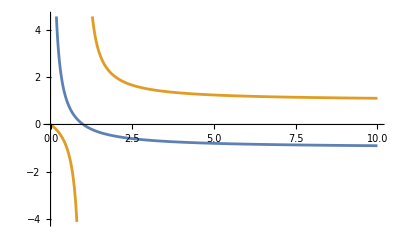

```mathematica
Plot[{-(1-1/r),(1-1/r)^-1},{r,0,10}]
```

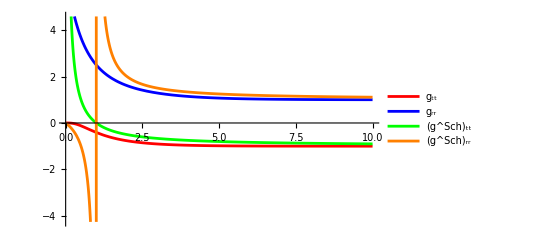

```mathematica
Plot[{gttlinearf2K1λ1/.{C[1]->1,C[2]->1,C[3]->0},grrlinearf2K1λ1/.{C[1]->1,C[2]->1,C[3]->0},-(1-1/r),(1-1/r)^-1},{r,0,10},PlotStyle->{Red,Blue,Green,Orange},PlotLegends->{"g_tt","g_rr","(g^Sch)_tt","(g^Sch)_rr"}]
```

```mathematica
Xf4K1λ1=C[1] f4K1λ1eigenvector1[[1]] E^(f4K1λ1eigenvalue1*r)+C[2] f4K1λ1eigenvector2[[1]] E^(f4K1λ1eigenvalue2*r)
Af4K1λ1=C[1] f4K1λ1eigenvector1[[2]] E^(f4K1λ1eigenvalue1*r)+C[2] f4K1λ1eigenvector2[[2]] E^(f4K1λ1eigenvalue2*r)
```

-(3 (4+3 √2) ⅇ^(-r/(√2)) C[2])/(10+7 √2)

ⅇ^(-2 (1+√2) r) C[1]+ⅇ^(-r/(√2)) C[2]

```mathematica
ϕlinearf4K1λ1=DSolve[r ϕ'[r]==Xf4K1λ1,ϕ[r],r][[1]][[1]]
αlinearf4K1λ1=DSolve[r α'[r]==Xf4K1λ1,α[r],r][[1]][[1]]
αlinearprimef4K1λ1=D[αlinearf4K1λ1,r]
ϕlinearprimef4K1λ1=D[ϕlinearf4K1λ1,r]
γlinearf4K1λ1=(gammanew/. {K->1,λ->1})/. {ϕlinearprimef4K1λ1,αlinearprimef4K1λ1}//Simplify
```

ϕ[r]→C[3]-3 (-1+√2) C[2] ExpIntegralEi[-r/(√2)]

α[r]→C[3]-3 (-1+√2) C[2] ExpIntegralEi[-r/(√2)]

α'[r]→-(3 (-1+√2) ⅇ^(-r/(√2)) C[2])/r

ϕ'[r]→-(3 (-1+√2) ⅇ^(-r/(√2)) C[2])/r

{γ[r]→1/2 Log[1-6 (-1+√2) ⅇ^(-r/(√2)) C[2]+21/2 (3-2 √2) ⅇ^(-√2 r) C[2]^2]}

```mathematica
gttlinearf4K1λ1=-Exp[2 αlinearf4K1λ1[[2]]]//Simplify
grrlinearf4K1λ1=Exp[2 γlinearf4K1λ1[[1]][[2]]]//Simplify
```

-ⅇ^(2 C[3]-6 (-1+√2) C[2] ExpIntegralEi[-r/(√2)])

1-6 (-1+√2) ⅇ^(-r/(√2)) C[2]+21/2 (3-2 √2) ⅇ^(-√2 r) C[2]^2

```mathematica
Limit[gttlinearf4K1λ1,r->Infinity]
Limit[grrlinearf4K1λ1,r->Infinity]
```

-ⅇ^(2 C[3])

1

### Streamplots for the choice λ_s=1 and K_B=9/5

```mathematica
f1K95λ1=fixedpoint1/.{K->9/5,λ->1}//Simplify;
f2K95λ1=fixedpoint2/.{K->9/5,λ->1}//Simplify;
f3K95λ1=fixedpoint3/.{K->9/5,λ->1}//Simplify;
f4K95λ1=fixedpoint4/.{K->9/5,λ->1}//Simplify;
f5K95λ1=fixedpoint5/.{K->9/5,λ->1}//Simplify;
f6K95λ1=fixedpoint6/.{K->9/5,λ->1}//Simplify;
```

```mathematica
{f1K95λ1,f2K95λ1,f3K95λ1,f4K95λ1,f5K95λ1,f6K95λ1}
```

{{Χ[r]→0,A[r]→-5/9 (2+√(2/5))},{Χ[r]→0,A[r]→1/9 (-10+√10)},{Χ[r]→1/51 (5-4 √145),A[r]→1/51 (-65+√145)},{Χ[r]→1/51 (5+4 √145),A[r]→1/51 (-65-√145)},{Χ[r]→-5/38 (4+2/(√5)),A[r]→-2/19 (10+√5)},{Χ[r]→1/19 (-10+√5),A[r]→2/19 (-10+√5)}}

```mathematica
(Solve[(Aprimerhs==0/.{K->9/5,λ->1})&&(Χprimerhs==0/.{K->9/5,λ->1}),{Χ[r],A[r]}]//Simplify)
```

{{Χ[r]→1/19 (-10-√5),A[r]→-2/19 (10+√5)},{Χ[r]→1/19 (-10+√5),A[r]→2/19 (-10+√5)},{Χ[r]→0,A[r]→1/9 (-10-√10)},{Χ[r]→0,A[r]→1/9 (-10+√10)},{Χ[r]→1/51 (5+4 √145),A[r]→1/51 (-65-√145)},{Χ[r]→1/51 (5-4 √145),A[r]→1/51 (-65+√145)}}

```mathematica
(Solve[(Aprimerhs==0/.{K->1,λ->1})&&(Χprimerhs==0/.{K->1,λ->1}),{Χ[r],A[r]}]//Simplify)
```

{{Χ[r]→-1,A[r]→-2},{Χ[r]→-1,A[r]→-4/3},{Χ[r]→-1/3,A[r]→-2/3},{Χ[r]→0,A[r]→-2-√2},{Χ[r]→0,A[r]→-2+√2}}

```mathematica
{dΧdr/. {K->9/5,λ->1},dAdr/. {K->9/5,λ->1}}
Solve[-18 x+12 y==0,y]
```

{(x (x (-6-28 x+(34 x^2)/5)+2 (19-(52 x)/5) x y+(-18+(123 x)/5) y^2-(54 y^3)/5))/(-18 x+12 y),(4 x^2 (-6+2 x)+x (30-48 x+(34 x^2)/5) y-2 (6-29 x+(52 x^2)/5) y^2+(-24+(123 x)/5) y^3-(54 y^4)/5)/(-18 x+12 y)}

{{y→(3 x)/2}}

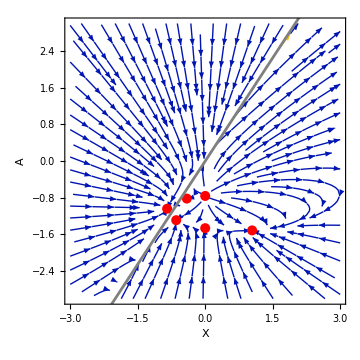

```mathematica
Show[StreamPlot[{dΧdr/. {K->9/5,λ->1},dAdr/. {K->9/5,λ->1}},{x,-3,3},{y,-3,3},FrameLabel->{Style["X",Black,12],Style["A",Black,12]},FrameStyle->Black],Graphics[{Red,PointSize[0.02],Point/@{{f1K95λ1[[1]][[2]],f1K95λ1[[2]][[2]]},{f2K95λ1[[1]][[2]],f2K95λ1[[2]][[2]]},{f3K95λ1[[1]][[2]],f3K95λ1[[2]][[2]]},{f4K95λ1[[1]][[2]],f4K95λ1[[2]][[2]]},{f5K95λ1[[1]][[2]],f5K95λ1[[2]][[2]]},{f6K95λ1[[1]][[2]],f6K95λ1[[2]][[2]]}},Text["",{f6K95λ1[[1]][[2]],f6K95λ1[[2]][[2]]},{1,1}]}],Plot[3/2 x,{x,-5,5},PlotStyle->Directive[Gray]],ImageSize->Medium]
```

```mathematica
Series[dΧdr/.{K->9/5},{λ,Infinity,1},Assumptions->λ>0]
```

-(3 x^3 λ)/10+1/30 x (30+70 x+x^2-30 y+36 x y-27 y^2)+(-6 x-7 x^2-x^3+6 y+4 x y-2 x^2 y+3 y^2+3 x y^2)/(3 λ)+O[1/λ]^2

```mathematica
Series[dAdr/.{K->9/5},{λ,Infinity,1},Assumptions->λ>0]
```

1/30 (-10 x^2-9 x^2 y) λ+1/30 (60 x-30 y+100 x y+x^2 y-60 y^2+36 x y^2-27 y^3)+(-6 x-x^2+6 y-8 x y-x^2 y+9 y^2-2 x y^2+3 y^3)/(3 λ)+O[1/λ]^2

```mathematica
Solve[1/30 x (30+70 x+x^2-30 y+36 x y-27 y^2)==0&&1/30 (60 x-30 y+100 x y+x^2 y-60 y^2+36 x y^2-27 y^3)==0,{x,y}]
```

{{x→-3,y→-3},{x→1-√19,y→-2},{x→1+√19,y→-2},{x→-1,y→-1},{x→0,y→0},{x→0,y→1/9 (-10-√10)},{x→0,y→1/9 (-10+√10)}}

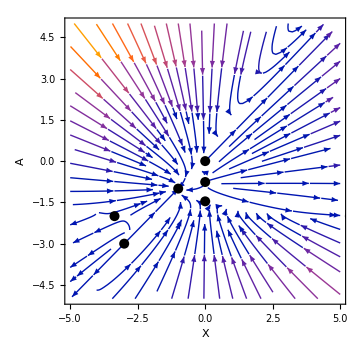
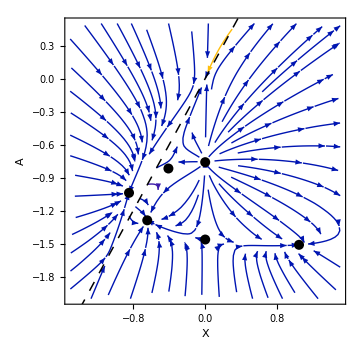

```mathematica
{
Show[StreamPlot[{1/30 x (30+70 x+x^2-30 y+36 x y-27 y^2),1/30 (60 x-30 y+100 x y+x^2 y-60 y^2+36 x y^2-27 y^3)},{x,-5,5},{y,-5,5},StreamPoints->70,StreamScale->Medium,FrameLabel->{Style["X",12],Style["A",12]}],Graphics[{Black,PointSize[0.02],Point/@{{-3,-3}},White,FontSize->14}],
Graphics[{Black,PointSize[0.02],Point/@{{1-√19,-2}},White,FontSize->14}],
Graphics[{Black,PointSize[0.02],Point/@{{1+√19,-2}},White,FontSize->14}],
Graphics[{Black,PointSize[0.02],Point/@{{-1,-1}},White,FontSize->14}],
Graphics[{Black,PointSize[0.02],Point/@{{0,0}},White,FontSize->14}],
Graphics[{Black,PointSize[0.02],Point/@{{0,1/9 (-10-√10)}},White,FontSize->14}],
Graphics[{Black,PointSize[0.02],Point/@{{0,1/9 (-10+√10)}},White,FontSize->14}],
ImageSize->Medium],
Show[StreamPlot[{dΧdr/. {K->9/5,λ->1},dAdr/. {K->9/5,λ->1}},{x,-1.5,1.5},{y,-2,0.5},StreamPoints->70,StreamScale->Medium,FrameLabel->{Style["X",12],Style["A",12]}],Graphics[{Black,PointSize[0.02],Point/@{{f1K95λ1[[1]][[2]],f1K95λ1[[2]][[2]]}},White,FontSize->14}],
Graphics[{Black,PointSize[0.02],Point/@{{f2K95λ1[[1]][[2]],f2K95λ1[[2]][[2]]}},White,FontSize->14}],
Graphics[{Black,PointSize[0.02],Point/@{{f3K95λ1[[1]][[2]],f3K95λ1[[2]][[2]]}},White,FontSize->14}],
Graphics[{Black,PointSize[0.02],Point/@{{f4K95λ1[[1]][[2]],f4K95λ1[[2]][[2]]}},White,FontSize->14}],
Graphics[{Black,PointSize[0.02],Point/@{{f5K95λ1[[1]][[2]],f5K95λ1[[2]][[2]]}},White,FontSize->14}],
Graphics[{Black,PointSize[0.02],Point/@{{f6K95λ1[[1]][[2]],f6K95λ1[[2]][[2]]}},White,FontSize->14}],
Plot[3/2 x,{x,-5,5},PlotStyle->Directive[Black,Dashing[0.02],Thickness[0.003]]],ImageSize->Medium]
}
```

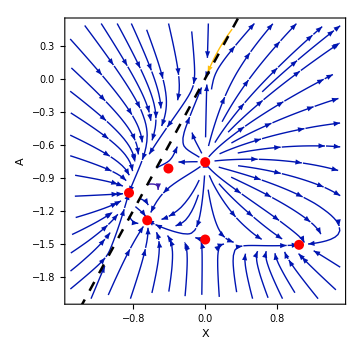

C:\Users\Aiver\Documents\4th Year\Physics 199\Thesis Revision\Figures\streamplot.pdf

```mathematica
streamplot=Show[StreamPlot[{dΧdr/. {K->9/5,λ->1},dAdr/. {K->9/5,λ->1}},{x,-1.5,1.5},{y,-2,0.5},StreamPoints->70,StreamScale->Medium,FrameLabel->{Style["X",Black,12],Style["A",Black,12]},FrameStyle->Directive[Black,12,Thickness[0.005]]],Graphics[{Red,PointSize[0.02],Point/@{{f1K95λ1[[1]][[2]],f1K95λ1[[2]][[2]]}},Red,FontSize->14,Text["",{f1K95λ1[[1]][[2]],f1K95λ1[[2]][[2]]},{1,1}]}],
Graphics[{Red,PointSize[0.02],Point/@{{f2K95λ1[[1]][[2]],f2K95λ1[[2]][[2]]}},Red,FontSize->14,Text["",{f2K95λ1[[1]][[2]],f2K95λ1[[2]][[2]]},{1,1}]}],
Graphics[{Red,PointSize[0.02],Point/@{{f3K95λ1[[1]][[2]],f3K95λ1[[2]][[2]]}},Red,FontSize->14,Text["",{f3K95λ1[[1]][[2]],f3K95λ1[[2]][[2]]},{1,1}]}],
Graphics[{Red,PointSize[0.02],Point/@{{f4K95λ1[[1]][[2]],f4K95λ1[[2]][[2]]}},Red,FontSize->14,Text["",{f4K95λ1[[1]][[2]],f4K95λ1[[2]][[2]]},{1,1}]}],
Graphics[{Red,PointSize[0.02],Point/@{{f5K95λ1[[1]][[2]],f5K95λ1[[2]][[2]]}},Red,FontSize->14,Text["",{f5K95λ1[[1]][[2]],f5K95λ1[[2]][[2]]},{1,1}]}],
Graphics[{Red,PointSize[0.02],Point/@{{f6K95λ1[[1]][[2]],f6K95λ1[[2]][[2]]}},Red,FontSize->14,Text["",{f6K95λ1[[1]][[2]],f6K95λ1[[2]][[2]]},{1,1}]}],
Plot[3/2 x,{x,-5,5},PlotStyle->Directive[Black,Dashing[0.02],Thickness[0.005]]],ImageSize->Medium]

Export["C:\\Users\\Aiver\\Documents\\4th Year\\Physics 199\\Thesis Revision\\Figures\\streamplot.pdf",streamplot]
```

```mathematica
fixedpoint2/. {K->9/5,λ->1}
```

{Χ[r]→0,A[r]→5/9 (-2+√(2/5))}

```mathematica
fixedpoint2/. {K->9/5,λ->1}
```

{Χ[r]→0,A[r]→5/9 (-2+√(2/5))}

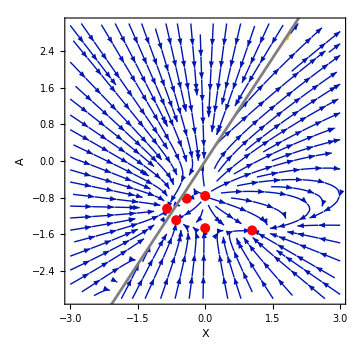

C:\Users\Aiver\Documents\4th Year\Physics 199\Final Thesis Tex\figures\streamplotK95.pdf

```mathematica
streamplotK95=Show[StreamPlot[{dΧdr/. {K->9/5,λ->1},dAdr/. {K->9/5,λ->1}},{x,-3,3},{y,-3,3},FrameLabel->{Style["X",Black,12],Style["A",Black,12]},FrameStyle->Black],Graphics[{Red,PointSize[0.02],Point/@{{f1K95λ1[[1]][[2]],f1K95λ1[[2]][[2]]}},Red,FontSize->12,Text["",{f1K95λ1[[1]][[2]],f1K95λ1[[2]][[2]]},{1,1}]}],
Graphics[{Red,PointSize[0.02],Point/@{{f2K95λ1[[1]][[2]],f2K95λ1[[2]][[2]]}},Red,FontSize->12,Text["",{f2K95λ1[[1]][[2]],f2K95λ1[[2]][[2]]},{1,1}]}],
Graphics[{Red,PointSize[0.02],Point/@{{f3K95λ1[[1]][[2]],f3K95λ1[[2]][[2]]}},Red,FontSize->12,Text["",{f3K95λ1[[1]][[2]],f3K95λ1[[2]][[2]]},{1,1}]}],
Graphics[{Red,PointSize[0.02],Point/@{{f4K95λ1[[1]][[2]],f4K95λ1[[2]][[2]]}},Red,FontSize->12,Text["",{f4K95λ1[[1]][[2]],f4K95λ1[[2]][[2]]},{1,1}]}],
Graphics[{Red,PointSize[0.02],Point/@{{f5K95λ1[[1]][[2]],f5K95λ1[[2]][[2]]}},Red,FontSize->12,Text["",{f5K95λ1[[1]][[2]],f5K95λ1[[2]][[2]]},{1,1}]}],
Graphics[{Red,PointSize[0.02],Point/@{{f6K95λ1[[1]][[2]],f6K95λ1[[2]][[2]]}},Red,FontSize->12,Text["",{f6K95λ1[[1]][[2]],f6K95λ1[[2]][[2]]},{1,1}]}],
Plot[3/2 x,{x,-5,5},PlotStyle->Directive[Gray],PlotLegends->{Style["",Black,12]}],ImageSize->Medium,Background->White]

Export["C:\\Users\\Aiver\\Documents\\4th Year\\Physics 199\\Final Thesis Tex\\figures\\streamplotK95.pdf",streamplotK95]
```

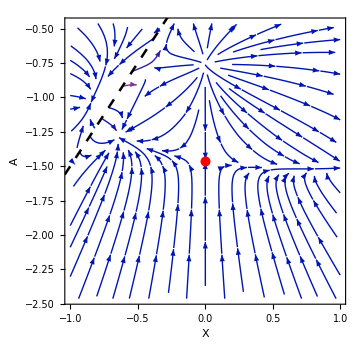
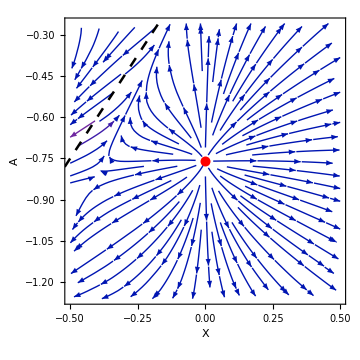
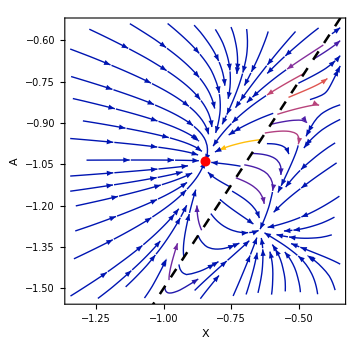
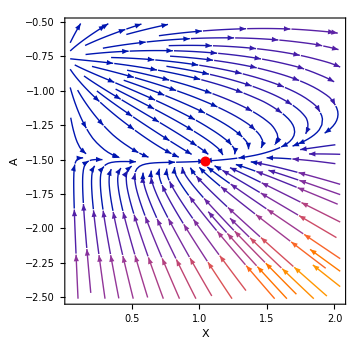
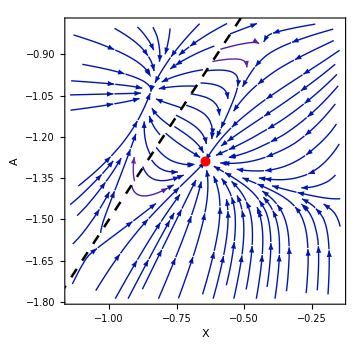
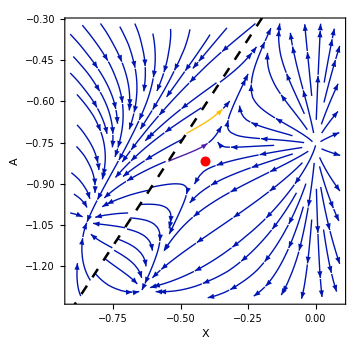

```mathematica
{streamplotK95f1=Show[StreamPlot[{dΧdr/. {K->9/5,λ->1},dAdr/. {K->9/5,λ->1}},{x,f1K95λ1[[1]][[2]]-1,f1K95λ1[[1]][[2]]+1},{y,f1K95λ1[[2]][[2]]-1,f1K95λ1[[2]][[2]]+1},StreamPoints->70,StreamScale->Medium,FrameLabel->{Style["X",Black,12],Style["A",Black,12]},FrameStyle->Directive[Black,12,Thickness[0.005]]],Graphics[{Red,PointSize[0.02],Point/@{{f1K95λ1[[1]][[2]],f1K95λ1[[2]][[2]]}},Red,FontSize->12,Text["",{f1K95λ1[[1]][[2]],f1K95λ1[[2]][[2]]},{1,1}]}],Plot[3/2 x,{x,-5,5},PlotStyle->Directive[Black,Dashing[0.02],Thickness[0.005]]],ImageSize->Medium,Background->White],

streamplotK95f2=Show[StreamPlot[{dΧdr/. {K->9/5,λ->1},dAdr/. {K->9/5,λ->1}},{x,f2K95λ1[[1]][[2]]-0.5,f2K95λ1[[1]][[2]]+0.5},{y,f2K95λ1[[2]][[2]]-0.5,f2K95λ1[[2]][[2]]+0.5},StreamPoints->70,StreamScale->Medium,FrameLabel->{Style["X",Black,12],Style["A",Black,12]},FrameStyle->Directive[Black,12,Thickness[0.005]]],Graphics[{Red,PointSize[0.02],Point/@{{f2K95λ1[[1]][[2]],f2K95λ1[[2]][[2]]}},Red,FontSize->12,Text["",{f2K95λ1[[1]][[2]],f2K95λ1[[2]][[2]]},{1,1}]}],Plot[3/2 x,{x,-5,5},PlotStyle->Directive[Black,Dashing[0.02],Thickness[0.005]]],ImageSize->Medium,Background->White],

streamplotK95f3=Show[StreamPlot[{dΧdr/. {K->9/5,λ->1},dAdr/. {K->9/5,λ->1}},{x,f3K95λ1[[1]][[2]]-0.5,f3K95λ1[[1]][[2]]+0.5},{y,f3K95λ1[[2]][[2]]-0.5,f3K95λ1[[2]][[2]]+0.5},StreamPoints->70,StreamScale->Medium,FrameLabel->{Style["X",Black,12],Style["A",Black,12]},FrameStyle->Directive[Black,12,Thickness[0.005]]],Graphics[{Red,PointSize[0.02],Point/@{{f3K95λ1[[1]][[2]],f3K95λ1[[2]][[2]]}},Red,FontSize->12,Text["",{f3K95λ1[[1]][[2]],f3K95λ1[[2]][[2]]},{1,1}]}],Plot[3/2 x,{x,-5,5},PlotStyle->Directive[Black,Dashing[0.02],Thickness[0.005]]],ImageSize->Medium,Background->White],

streamplotK95f4=Show[StreamPlot[{dΧdr/. {K->9/5,λ->1},dAdr/. {K->9/5,λ->1}},{x,f4K95λ1[[1]][[2]]-1,f4K95λ1[[1]][[2]]+1},{y,f4K95λ1[[2]][[2]]-1,f4K95λ1[[2]][[2]]+1},StreamPoints->70,StreamScale->Medium,FrameLabel->{Style["X",Black,12],Style["A",Black,12]},FrameStyle->Directive[Black,12,Thickness[0.005]]],Graphics[{Red,PointSize[0.02],Point/@{{f4K95λ1[[1]][[2]],f4K95λ1[[2]][[2]]}},Red,FontSize->12,Text["",{f4K95λ1[[1]][[2]],f4K95λ1[[2]][[2]]},{1,1}]}],Plot[3/2 x,{x,-5,5},PlotStyle->Directive[Black,Dashing[0.02],Thickness[0.005]]],ImageSize->Medium,Background->White],

streamplotK95f5=Show[StreamPlot[{dΧdr/. {K->9/5,λ->1},dAdr/. {K->9/5,λ->1}},{x,f5K95λ1[[1]][[2]]-0.5,f5K95λ1[[1]][[2]]+0.5},{y,f5K95λ1[[2]][[2]]-0.5,f5K95λ1[[2]][[2]]+0.5},StreamPoints->70,StreamScale->Medium,FrameLabel->{Style["X",Black,12],Style["A",Black,12]},FrameStyle->Directive[Black,12,Thickness[0.005]]],Graphics[{Red,PointSize[0.02],Point/@{{f5K95λ1[[1]][[2]],f5K95λ1[[2]][[2]]}},Red,FontSize->12,Text["",{f5K95λ1[[1]][[2]],f5K95λ1[[2]][[2]]},{1,1}]}],Plot[3/2 x,{x,-5,5},PlotStyle->Directive[Black,Dashing[0.02],Thickness[0.005]]],ImageSize->Medium,Background->White],

streamplotK95f6=Show[StreamPlot[{dΧdr/. {K->9/5,λ->1},dAdr/. {K->9/5,λ->1}},{x,f6K95λ1[[1]][[2]]-0.5,f6K95λ1[[1]][[2]]+0.5},{y,f6K95λ1[[2]][[2]]-0.5,f6K95λ1[[2]][[2]]+0.5},StreamPoints->70,StreamScale->Medium,FrameLabel->{Style["X",Black,12],Style["A",Black,12]},FrameStyle->Directive[Black,12,Thickness[0.005]]],Graphics[{Red,PointSize[0.02],Point/@{{f6K95λ1[[1]][[2]],f6K95λ1[[2]][[2]]}},Red,FontSize->12,Text["",{f6K95λ1[[1]][[2]],f6K95λ1[[2]][[2]]},{1,1}]}],Plot[3/2 x,{x,-5,5},PlotStyle->Directive[Black,Dashing[0.02],Thickness[0.005]]],ImageSize->Medium,Background->White]
}
```

```mathematica
Export["C:\\Users\\Aiver\\Documents\\4th Year\\Physics 199\\Final Thesis Tex\\figures\\streamplotK95f1.svg",streamplotK95f1];
Export["C:\\Users\\Aiver\\Documents\\4th Year\\Physics 199\\Final Thesis Tex\\figures\\streamplotK95f2.svg",streamplotK95f2];
Export["C:\\Users\\Aiver\\Documents\\4th Year\\Physics 199\\Final Thesis Tex\\figures\\streamplotK95f3.svg",streamplotK95f3];Export["C:\\Users\\Aiver\\Documents\\4th Year\\Physics 199\\Final Thesis Tex\\figures\\streamplotK95f4.svg",streamplotK95f4];
Export["C:\\Users\\Aiver\\Documents\\4th Year\\Physics 199\\Final Thesis Tex\\figures\\streamplotK95f5.svg",streamplotK95f4];
Export["C:\\Users\\Aiver\\Documents\\4th Year\\Physics 199\\Final Thesis Tex\\figures\\streamplotK95f6.svg",streamplotK95f6];
```

```mathematica
(*streamploteachK95=GraphicsGrid[{

{streamplotK95f1,streamplotK95f2},
{streamplotK95f3,streamplotK95f4},
{streamplotK95f5,streamplotK95f6}
},

Frame->False]

Export["C:\\Users\\Aiver\\Documents\\4th Year\\Physics 199\\Thesis Revision\\Figures\\streamploteachK95.pdf",streamploteachK95];*)
```

```mathematica
dAdX=(Aprimerhs/Χprimerhs)/.{Χ[r]->X,A[r]->A[X]};
```

```mathematica
dXdA=(Χprimerhs/Aprimerhs)/.{Χ[r]->X[A],A[r]->A};
```

```mathematica
XofAsolnminus32f3=NDSolve[{X'[A]==dXdA/.{K->9/5,λ->1},X[-19/10]==-3/2},X[A],{A,-19/10,fixedpoint3[[2]][[2]]/.{K->9/5,λ->1}}]
```

{{X[A]→InterpolatingFunction[…][A]}}

```mathematica
AofXsolnminus32f3=NDSolve[{A'[X]==dAdX/.{K->9/5,λ->1},A[-3/2]==-19/10},A[X],{X,-3/2,fixedpoint3[[1]][[2]]/.{K->9/5,λ->1}}]
```

{{A[X]→InterpolatingFunction[…][X]}}

```mathematica
XofAofrsolnminus32f3=XofAsolnminus32f3[[1]][[1]][[2]]/.A->A[r]
```

InterpolatingFunction[…][A[r]]

```mathematica
FofAsolnminus32f3=Aprimerhs/.{K->9/5,λ->1,Χ[r]->X}/.{X->XofAofrsolnminus32f3}
```

(-54/5 A[r]^4+4 (InterpolatingFunction[…][A[r]])^2 (-6+2 InterpolatingFunction[…][A[r]])+A[r]^3 (-24+123/5 InterpolatingFunction[…][A[r]])+A[r] InterpolatingFunction[…][A[r]] (30-48 InterpolatingFunction[…][A[r]]+34/5 (InterpolatingFunction[…][A[r]])^2)-2 A[r]^2 (6-29 InterpolatingFunction[…][A[r]]+52/5 (InterpolatingFunction[…][A[r]])^2))/(12 A[r]-18 InterpolatingFunction[…][A[r]])

```mathematica
Χprimerhs
```

(Χ[r] (-6 K A[r]^3+2 A[r] Χ[r] (16+3 λ+(4-5 K-3 K λ) Χ[r])+A[r]^2 (-18+(-6+14 K+3 K λ) Χ[r])+Χ[r] (-6 λ-14 (1+λ) Χ[r]+(1+λ) (-2+K (2+λ)) Χ[r]^2)))/(12 A[r]-6 (2+λ) Χ[r])

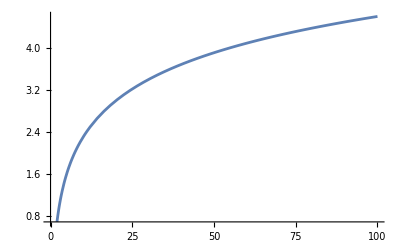

```mathematica
Plot[Log[r],{r,0,100}]
```

```mathematica
Asolnf3=NDSolve[{A'[r]==FofAsolnminus32f3,A[0]==-19/10},A[r],{r,0,10^3}]
```

{{A[r]→InterpolatingFunction[…][r]}}

```mathematica
t=NDSolve[{Asolnf3[[1]][[1]][[2]]==r α'[r],α[1/10]==2},α[r],{r,1/10,10^3}][[1]][[1]][[2]]
```

InterpolatingFunction[…][r]

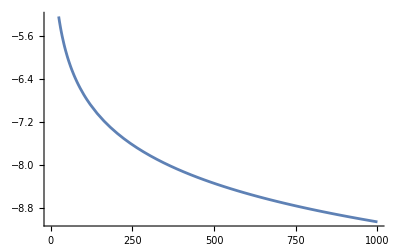

```mathematica
Plot[t,{r,1/10,10^3}]
```

```mathematica
α[1]==2
```

α[1]==2

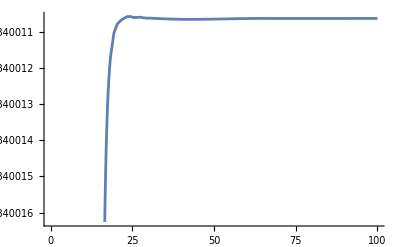

```mathematica
Plot[Asolnf3[[1]][[1]][[2]],{r,0,100}]
```

```mathematica
AofXsolnminus65minus1=Evaluate[A[X]/.NDSolve[{A'[X]==dAdX/.{K->9/5,λ->1},A[-6/5]==-1},A[X],{X,-6/5,1/51 (5-4 √145)}][[1]][[1]]];
```

```mathematica
A2expdim=A2exp/.{Χ[r]->r ϕ'[r],A[r]->r α'[r]};
Χ2expdim=Χ2exp/.{Χ[r]->r ϕ'[r],A[r]->r α'[r]};
```

```mathematica
solnK95Xminus65Aminus1nonlinear=NDSolve[{(1/r^2)*Χ2expdim==ϕ''[r]/.{K->9/5,λ->1},(1/r^2)*A2expdim==α''[r]/.{K->9/5,λ->1},ϕ'[2]==-1/2,α'[2]==-6/(5*2),ϕ[2]==0,α[2]==0},{ϕ[r],α[r]},{r,2,10^5}][[1]]
```

{ϕ[r]→InterpolatingFunction[…][r],α[r]→InterpolatingFunction[…][r]}

```mathematica
NDSolve[{A'[r]==Aprimerhs/.{K->9/5,λ->1},Χ[r]==Χprimerhs/.{K->9/5,λ->1},A[1/1000]==0,Χ[1/1000]==-3/2},{A[r],Χ[r]},{r,1/1000,10}]
```

NDSolve::ivres: NDSolve has computed initial values that give a zero residual for the differential-algebraic system, but some components are different from those specified. If you need them to be satisfied, giving initial conditions for all dependent variables and their derivatives is recommended.

{{A[r]→InterpolatingFunction[…][r],Χ[r]→InterpolatingFunction[…][r]}}

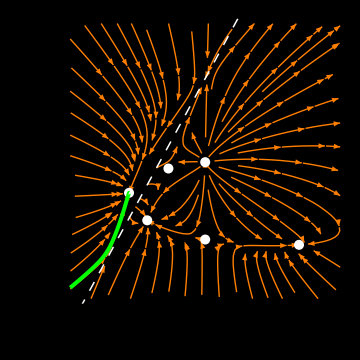

C:\Users\Aiver\Documents\4th Year\Physics 199\Thesis poster\streamplotwline.svg

```mathematica
streamplotwline=Show[StreamPlot[{dΧdr/. {K->9/5,λ->1},dAdr/. {K->9/5,λ->1}},{x,-1.5,1.5},{y,-2,0.5},StreamPoints->70,StreamScale->Medium,StreamStyle->RGBColor[255/255,127/255,0/255],StreamColorFunction->None,FrameLabel->{Style["X",White,12],Style["A",White,12]},FrameStyle->Directive[White,12,Thickness[0.005]]],Graphics[{White,PointSize[0.02],Point/@{{f1K95λ1[[1]][[2]],f1K95λ1[[2]][[2]]}},White,FontSize->14,Text["",{f1K95λ1[[1]][[2]],f1K95λ1[[2]][[2]]},{1,1}]}],
Graphics[{White,PointSize[0.02],Point/@{{f2K95λ1[[1]][[2]],f2K95λ1[[2]][[2]]}},White,FontSize->14,Text["",{f2K95λ1[[1]][[2]],f2K95λ1[[2]][[2]]},{1,1}]}],
Graphics[{White,PointSize[0.02],Point/@{{f3K95λ1[[1]][[2]],f3K95λ1[[2]][[2]]}},White,FontSize->14,Text["",{f3K95λ1[[1]][[2]],f3K95λ1[[2]][[2]]},{1,1}]}],
Graphics[{White,PointSize[0.02],Point/@{{f4K95λ1[[1]][[2]],f4K95λ1[[2]][[2]]}},White,FontSize->14,Text["",{f4K95λ1[[1]][[2]],f4K95λ1[[2]][[2]]},{1,1}]}],
Graphics[{White,PointSize[0.02],Point/@{{f5K95λ1[[1]][[2]],f5K95λ1[[2]][[2]]}},White,FontSize->14,Text["",{f5K95λ1[[1]][[2]],f5K95λ1[[2]][[2]]},{1,1}]}],
Graphics[{White,PointSize[0.02],Point/@{{f6K95λ1[[1]][[2]],f6K95λ1[[2]][[2]]}},White,FontSize->14,Text["",{f6K95λ1[[1]][[2]],f6K95λ1[[2]][[2]]},{1,1}]}],
Plot[3/2 x,{x,-5,5},PlotStyle->Directive[White,Dashing[0.02],Thickness[0.003]]],
Plot[AofXsolnminus32f3[[1]][[1]][[2]],{X,-3/2,-846/1000},PlotStyle->Directive[Green,Thickness[0.008]]],ImageSize->Medium,Background->Black]
Export["C:\\Users\\Aiver\\Documents\\4th Year\\Physics 199\\Thesis poster\\streamplotwline.svg",streamplotwline,Background->None]
```

```mathematica
fixedpoint3[[1]][[2]]/.{K->9/5,λ->1}//N
```

-0.8464

```mathematica
{ϕsolnK95Xminus65Aminus1,αsolnK95Xminus65Aminus1}={Evaluate[ϕ[r]/.solnK95Xminus65Aminus1nonlinear[[1]]],Evaluate[α[r]/.solnK95Xminus65Aminus1nonlinear[[2]]]}
```

{InterpolatingFunction[…][r],InterpolatingFunction[…][r]}

```mathematica
solnK95Xminus65Aminus1=NDSolve[{Χ'[r]==Χprimerhs/.{K->9/5,λ->1},A'[r]==Aprimerhs/.{K->9/5,λ->1},Χ[0]==-6/5,A[0]==-1},{Χ[r],A[r]},{r,0,10},WorkingPrecision->30,MaxSteps->10000];
XsolnK95Xminus65Aminus1=Evaluate[Χ[r]/.solnK95Xminus65Aminus1[[1]][[1]]];
AsolnK95Xminus65Aminus1=Evaluate[A[r]/.solnK95Xminus65Aminus1[[1]][[2]]];
```

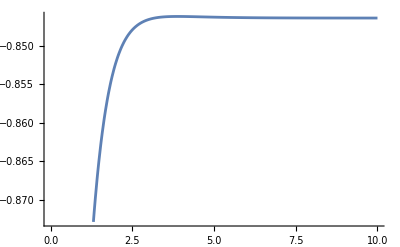

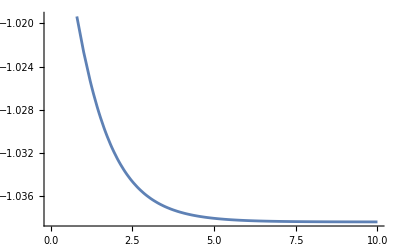

```mathematica
Plot[XsolnK95Xminus65Aminus1,{r,0,10}]
Plot[AsolnK95Xminus65Aminus1,{r,0,10}]
```

#### Isoclines

```mathematica
{dAdr==0/.{K->9/5,λ->1},dAdr==0/.{K->1,λ->1}}
```

{(4 x^2 (-6+2 x)+x (30-48 x+(34 x^2)/5) y-2 (6-29 x+(52 x^2)/5) y^2+(-24+(123 x)/5) y^3-(54 y^4)/5)/(-18 x+12 y)==0,(4 x^2 (-6+2 x)+x (30-48 x+2 x^2) y-2 (6-29 x+4 x^2) y^2+(-24+11 x) y^3-6 y^4)/(-18 x+12 y)==0}

```mathematica
IsoclineinfK95λ1=(Solve[dAdr==0/.{K->9/5,λ->1},y]//Simplify);
Isoclineinf1K95λ1=IsoclineinfK95λ1[[1]][[1]][[2]];
Isoclineinf2K95λ1=IsoclineinfK95λ1[[2]][[1]][[2]];
Isoclineinf3K95λ1=IsoclineinfK95λ1[[3]][[1]][[2]];
Isoclineinf4K95λ1=IsoclineinfK95λ1[[4]][[1]][[2]];

IsoclinezeroK95λ1=(Solve[dΧdr==0/.{K->9/5,λ->1},y]//Simplify);
Isoclinezero1K95λ1=IsoclinezeroK95λ1[[1]][[1]][[2]];
Isoclinezero2K95λ1=IsoclinezeroK95λ1[[2]][[1]][[2]];
Isoclinezero3K95λ1=IsoclinezeroK95λ1[[3]][[1]][[2]];
```

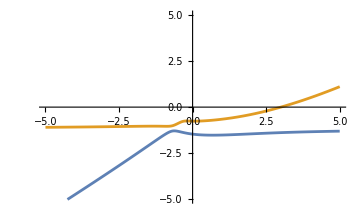
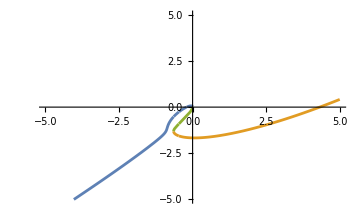

```mathematica
{Plot[{Isoclineinf1K95λ1,Isoclineinf2K95λ1,Isoclineinf3K95λ1,Isoclineinf4K95λ1},{x,-5,5},PlotRange->5,ImageSize->Medium],
Plot[{Isoclinezero1K95λ1,Isoclinezero2K95λ1,Isoclinezero3K95λ1},{x,-5,5},PlotRange->5,ImageSize->Medium]}
```

#### Streamplot with isoclines

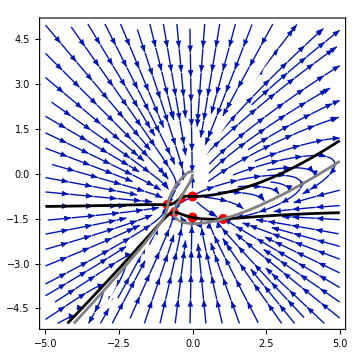

```mathematica
Show[StreamPlot[{dΧdr/. {K->9/5,λ->1},dAdr/. {K->9/5,λ->1}},{x,-5,5},{y,-5,5}],Graphics[{Red,PointSize[0.02],Point/@{{f1K95λ1[[1]][[2]],f1K95λ1[[2]][[2]]},{f2K95λ1[[1]][[2]],f2K95λ1[[2]][[2]]},{f3K95λ1[[1]][[2]],f3K95λ1[[2]][[2]]},{f4K95λ1[[1]][[2]],f4K95λ1[[2]][[2]]},{f5K95λ1[[1]][[2]],f5K95λ1[[2]][[2]]},{f6K95λ1[[1]][[2]],f6K95λ1[[2]][[2]]}}}],Plot[3/2 x,{x,-5,5},PlotStyle->White],Plot[{Isoclineinf1K95λ1,Isoclineinf2K95λ1,Isoclineinf3K95λ1,Isoclineinf4K95λ1},{x,-5,5},PlotRange->5,ImageSize->Medium,PlotStyle->Black],
Plot[{Isoclinezero1K95λ1,Isoclinezero2K95λ1,Isoclinezero3K95λ1},{x,-5,5},PlotRange->5,ImageSize->Medium,PlotStyle->Gray],ImageSize->Medium]
```

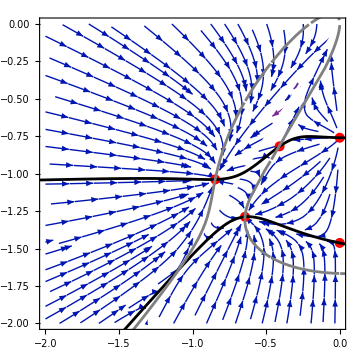

```mathematica
Show[StreamPlot[{dΧdr/. {K->9/5,λ->1},dAdr/. {K->9/5,λ->1}},{x,-2,0},{y,-2,0}],Graphics[{Red,PointSize[0.02],Point/@{{f1K95λ1[[1]][[2]],f1K95λ1[[2]][[2]]},{f2K95λ1[[1]][[2]],f2K95λ1[[2]][[2]]},{f3K95λ1[[1]][[2]],f3K95λ1[[2]][[2]]},{f4K95λ1[[1]][[2]],f4K95λ1[[2]][[2]]},{f5K95λ1[[1]][[2]],f5K95λ1[[2]][[2]]},{f6K95λ1[[1]][[2]],f6K95λ1[[2]][[2]]}}}],Plot[3/2 x,{x,-5,5},PlotStyle->White],Plot[{Isoclineinf1K95λ1,Isoclineinf2K95λ1,Isoclineinf3K95λ1,Isoclineinf4K95λ1},{x,-5,5},PlotRange->5,ImageSize->Medium,PlotStyle->Black],
Plot[{Isoclinezero1K95λ1,Isoclinezero2K95λ1,Isoclinezero3K95λ1},{x,-5,5},PlotRange->5,ImageSize->Medium,PlotStyle->Gray],ImageSize->Medium]
```

#### Attractors and their physical meaning

```mathematica
f3K95λ1
f4K95λ1
f5K95λ1
```

{Χ[r]→1/51 (5-4 √145),A[r]→1/51 (-65+√145)}

{Χ[r]→1/51 (5+4 √145),A[r]→1/51 (-65-√145)}

{Χ[r]→-5/38 (4+2/(√5)),A[r]→-2/19 (10+√5)}

```mathematica
λ1JacobianYf3K95λ1=λ1JacobianYf3/.{K->9/5,λ->1}//Simplify;
λ2JacobianYf3K95λ1=λ2JacobianYf3/.{K->9/5,λ->1}//Simplify;
```

```mathematica
λ2JacobianYf3K95λ1
```

(145 (-43339+3551 √145+√(1364889170-113344450 √145)))/(102 (145-14 √145)^2)

```mathematica
λ1JacobianYf4K95λ1=λ1JacobianYf4/.{K->9/5,λ->1}//Simplify;
λ2JacobianYf4K95λ1=λ2JacobianYf4/.{K->9/5,λ->1}//Simplify;
```

```mathematica
λ1JacobianYf5K95λ1=λ1JacobianYf5/.{K->9/5,λ->1}//Simplify;
λ2JacobianYf5K95λ1=λ2JacobianYf5/.{K->9/5,λ->1}//Simplify;
```

```mathematica
v1JacobianYf3K95λ1=Eigenvectors[JacobianYf3/.{K->9/5,λ->1}][[1]]//Simplify;
v2JacobianYf3K95λ1=Eigenvectors[JacobianYf3/.{K->9/5,λ->1}][[2]]//Simplify;
```

```mathematica
v1JacobianYf4K95λ1=Eigenvectors[JacobianYf4/.{K->9/5,λ->1}][[1]];
v2JacobianYf4K95λ1=Eigenvectors[JacobianYf4/.{K->9/5,λ->1}][[2]];
```

```mathematica
v1JacobianYf5K95λ1=Eigenvectors[JacobianYf5/.{K->9/5,λ->1}][[1]];
v2JacobianYf5K95λ1=Eigenvectors[JacobianYf5/.{K->9/5,λ->1}][[2]];
```

```mathematica
Xsolnf3K95λ1manual= C[1]v1JacobianYf3K95λ1[[1]] ⅇ^((λ1JacobianYf3K95λ1)*r)+ C[2]v2JacobianYf3K95λ1[[1]] ⅇ^(λ2JacobianYf3K95λ1*r);
Asolnf3K95λ1manual= C[1]v1JacobianYf3K95λ1[[2]] ⅇ^(λ1JacobianYf3K95λ1*r)+ C[2]v2JacobianYf3K95λ1[[2]] ⅇ^(λ2JacobianYf3K95λ1*r);
```

```mathematica
Xsolnf4K95λ1manual= C[1]v1JacobianYf4K95λ1[[1]] ⅇ^((λ1JacobianYf4K95λ1)*r)+ C[2]v2JacobianYf4K95λ1[[1]] ⅇ^(λ2JacobianYf4K95λ1*r);
Asolnf4K95λ1manual= C[1]v1JacobianYf4K95λ1[[2]] ⅇ^(λ1JacobianYf4K95λ1*r)+ C[2]v2JacobianYf4K95λ1[[2]] ⅇ^(λ2JacobianYf4K95λ1*r);
```

```mathematica
Xsolnf5K95λ1manual= C[1]v1JacobianYf5K95λ1[[1]] ⅇ^((λ1JacobianYf5K95λ1)*r)+ C[2]v2JacobianYf5K95λ1[[1]] ⅇ^(λ2JacobianYf5K95λ1*r);
Asolnf5K95λ1manual= C[1]v1JacobianYf5K95λ1[[2]] ⅇ^(λ1JacobianYf5K95λ1*r)+ C[2]v2JacobianYf5K95λ1[[2]] ⅇ^(λ2JacobianYf5K95λ1*r);
```

Linear solutions for α

```mathematica
Asolnf3K95λ1manual
```

ⅇ^(((43339-3551 √145+√(1364889170-113344450 √145)) r)/(102 (-341+28 √145))) C[1]+ⅇ^((145 (-43339+3551 √145+√(1364889170-113344450 √145)) r)/(102 (145-14 √145)^2)) C[2]

```mathematica
αsolnlinearf3K95λ1manual=DSolve[r α'[r]==(Asolnf3K95λ1manual/.r->Log[r]),α[r],r];
αsolnlinearf4K95λ1manual=DSolve[r α'[r]==(Asolnf4K95λ1manual/.r->Log[r]),α[r],r];
αsolnlinearf5K95λ1manual=DSolve[r α'[r]==(Asolnf5K95λ1manual/.r->Log[r]),α[r],r];
```

```mathematica
αsolnlinearf3K95λ1r0=DSolve[r α'[r]==(Asolnf3K95λ1manual/.r->Log[r/r0]),α[r],r];
αsolnlinearf4K95λ1r0=DSolve[r α'[r]==(Asolnf4K95λ1manual/.r->Log[r/r0]),α[r],r];
αsolnlinearf5K95λ1r0=DSolve[r α'[r]==(Asolnf5K95λ1manual/.r->Log[r/r0]),α[r],r];
```

```mathematica
αsolnlinearf3K95λ1r0[[1]][[1]][[2]]//Simplify
```

1/(-10558140063508+876805804412 √145)(-229961+19096 √145) (r/r0)^((29195659-2424383 √145-140 √(7916357186-657397810 √145)+341 √(1364889170-113344450 √145))/(102 (-229961+19096 √145))) ((-29195659+2424383 √145-140 √(7916357186-657397810 √145)+341 √(1364889170-113344450 √145)) C[1]+(-29195659+2424383 √145+140 √(7916357186-657397810 √145)-341 √(1364889170-113344450 √145)) (r/r0)^(((-341 √5+140 √29) √(272977834-22668890 √145))/(51 (-229961+19096 √145))) C[2])+C[3]

```mathematica
N[(29195659-2424383 √145-140 √(7916357186-657397810 √145)+341 √(1364889170-113344450 √145))/(102 (-229961+19096 √145))]
```

-2.

```mathematica
N[((-341 √5+140 √29) √(272977834-22668890 √145))/(51 (-229961+19096 √145))]
```

1.0384

```mathematica
αsolnlinearf3K95λ1AX=αsolnlinearf3K95λ1manual/.{C[1]->(A v2JacobianYf3K95λ1[[1]]-X v2JacobianYf3K95λ1[[2]])/(v1JacobianYf3K95λ1[[2]]*v2JacobianYf3K95λ1[[1]]-v1JacobianYf3K95λ1[[1]]v2JacobianYf3K95λ1[[2]]),C[2]->(A v1JacobianYf3K95λ1[[1]]-X v1JacobianYf3K95λ1[[2]])/(v1JacobianYf3K95λ1[[1]]*v2JacobianYf3K95λ1[[2]]-v1JacobianYf3K95λ1[[2]]v2JacobianYf3K95λ1[[1]])};
```

```mathematica
αsolnlinearf4K95λ1AX=αsolnlinearf4K95λ1manual/.{C[1]->(A v2JacobianYf3K95λ1[[1]]-X v2JacobianYf3K95λ1[[2]])/(v1JacobianYf3K95λ1[[2]]*v2JacobianYf3K95λ1[[1]]-v1JacobianYf3K95λ1[[1]]v2JacobianYf3K95λ1[[2]]),C[2]->(A v1JacobianYf3K95λ1[[1]]-X v1JacobianYf3K95λ1[[2]])/(v1JacobianYf3K95λ1[[1]]*v2JacobianYf3K95λ1[[2]]-v1JacobianYf3K95λ1[[2]]v2JacobianYf3K95λ1[[1]])};
```

```mathematica
αsolnlinearf5K95λ1AX=αsolnlinearf5K95λ1manual/.{C[1]->(A v2JacobianYf3K95λ1[[1]]-X v2JacobianYf3K95λ1[[2]])/(v1JacobianYf3K95λ1[[2]]*v2JacobianYf3K95λ1[[1]]-v1JacobianYf3K95λ1[[1]]v2JacobianYf3K95λ1[[2]]),C[2]->(A v1JacobianYf3K95λ1[[1]]-X v1JacobianYf3K95λ1[[2]])/(v1JacobianYf3K95λ1[[1]]*v2JacobianYf3K95λ1[[2]]-v1JacobianYf3K95λ1[[2]]v2JacobianYf3K95λ1[[1]])};
```

Linear solutions for ϕ

```mathematica
ϕsolnlinearf3K95λ1manual=DSolve[r ϕ'[r]==(Xsolnf3K95λ1manual/.r->Log[r]),ϕ[r],r];
ϕsolnlinearf4K95λ1manual=DSolve[r ϕ'[r]==(Xsolnf4K95λ1manual/.r->Log[r]),ϕ[r],r];
ϕsolnlinearf5K95λ1manual=DSolve[r ϕ'[r]==(Xsolnf5K95λ1manual/.r->Log[r]),ϕ[r],r];
```

```mathematica
ϕsolnlinearf3K95λ1AX=ϕsolnlinearf3K95λ1manual/.{C[1]->(A v2JacobianYf3K95λ1[[1]]-X v2JacobianYf3K95λ1[[2]])/(v1JacobianYf3K95λ1[[2]]*v2JacobianYf3K95λ1[[1]]-v1JacobianYf3K95λ1[[1]]v2JacobianYf3K95λ1[[2]]),C[2]->(A v1JacobianYf3K95λ1[[1]]-X v1JacobianYf3K95λ1[[2]])/(v1JacobianYf3K95λ1[[1]]*v2JacobianYf3K95λ1[[2]]-v1JacobianYf3K95λ1[[2]]v2JacobianYf3K95λ1[[1]])};
```

```mathematica
ϕsolnlinearf4K95λ1AX=ϕsolnlinearf4K95λ1manual/.{C[1]->(A v2JacobianYf3K95λ1[[1]]-X v2JacobianYf3K95λ1[[2]])/(v1JacobianYf3K95λ1[[2]]*v2JacobianYf3K95λ1[[1]]-v1JacobianYf3K95λ1[[1]]v2JacobianYf3K95λ1[[2]]),C[2]->(A v1JacobianYf3K95λ1[[1]]-X v1JacobianYf3K95λ1[[2]])/(v1JacobianYf3K95λ1[[1]]*v2JacobianYf3K95λ1[[2]]-v1JacobianYf3K95λ1[[2]]v2JacobianYf3K95λ1[[1]])};
```

```mathematica
ϕsolnlinearf5K95λ1AX=ϕsolnlinearf5K95λ1manual/.{C[1]->(A v2JacobianYf3K95λ1[[1]]-X v2JacobianYf3K95λ1[[2]])/(v1JacobianYf3K95λ1[[2]]*v2JacobianYf3K95λ1[[1]]-v1JacobianYf3K95λ1[[1]]v2JacobianYf3K95λ1[[2]]),C[2]->(A v1JacobianYf3K95λ1[[1]]-X v1JacobianYf3K95λ1[[2]])/(v1JacobianYf3K95λ1[[1]]*v2JacobianYf3K95λ1[[2]]-v1JacobianYf3K95λ1[[2]]v2JacobianYf3K95λ1[[1]])};
```

Linear solutions for α’ and ϕ’

```mathematica
αprimesolnlinearf3K95λ1AX=D[αsolnlinearf3K95λ1AX,r][[1]][[1]][[2]];
ϕprimesolnlinearf3K95λ1AX=D[ϕsolnlinearf3K95λ1AX,r][[1]][[1]][[2]];

αprimesolnlinearf4K95λ1AX=D[αsolnlinearf4K95λ1AX,r][[1]][[1]][[2]];
ϕprimesolnlinearf4K95λ1AX=D[ϕsolnlinearf4K95λ1AX,r][[1]][[1]][[2]];

αprimesolnlinearf5K95λ1AX=D[αsolnlinearf5K95λ1AX,r][[1]][[1]][[2]];
ϕprimesolnlinearf5K95λ1AX=D[ϕsolnlinearf5K95λ1AX,r][[1]][[1]][[2]];
```

Linear solutions for γ

```mathematica
γsolnlinearf3K95λ1AX=gammanew[[1]][[2]]/.{K->9/5,λ->1,α'[r]->αprimesolnlinearf3K95λ1AX,ϕ'[r]->ϕprimesolnlinearf3K95λ1AX};
γsolnlinearf4K95λ1AX=gammanew[[1]][[2]]/.{K->9/5,λ->1,α'[r]->αprimesolnlinearf4K95λ1AX,ϕ'[r]->ϕprimesolnlinearf4K95λ1AX};
γsolnlinearf5K95λ1AX=gammanew[[1]][[2]]/.{K->9/5,λ->1,α'[r]->αprimesolnlinearf5K95λ1AX,ϕ'[r]->ϕprimesolnlinearf5K95λ1AX};
```

```mathematica
(*f3withoffsetpoints=Show[StreamPlot[{dΧdr/. {K->9/5,λ->1},dAdr/. {K->9/5,λ->1}},{x,f3K95λ1[[1]][[2]]-0.5,f3K95λ1[[1]][[2]]+0.5},{y,f3K95λ1[[2]][[2]]-0.5,f3K95λ1[[2]][[2]]+0.5},FrameLabel->{Style["X",Black,12],Style["A",Black,12]},FrameStyle->Black],

Graphics[{Red,PointSize[0.02],Point/@{{f3K95λ1[[1]][[2]],f3K95λ1[[2]][[2]]}},Red,FontSize->14,Text["",{f3K95λ1[[1]][[2]],f3K95λ1[[2]][[2]]},{1,1}]}],Plot[3/2 x,{x,-5,5},PlotStyle->Gray],
Graphics[{Black,PointSize[0.02],Point/@{{f3K95λ1[[1]][[2]]+1/10,f3K95λ1[[2]][[2]]}},Red,FontSize->14}],

Graphics[{Black,PointSize[0.02],Point/@{{f3K95λ1[[1]][[2]]-1/10,f3K95λ1[[2]][[2]]}},Red,FontSize->14}],

Graphics[{Black,PointSize[0.02],Point/@{{f3K95λ1[[1]][[2]],f3K95λ1[[2]][[2]]-1/10}},Red,FontSize->12}],

Graphics[{Black,PointSize[0.02],Point/@{{f3K95λ1[[1]][[2]]-1/10,f3K95λ1[[2]][[2]]}},Red,FontSize->12}],

Graphics[{Black,PointSize[0.02],Point/@{{f3K95λ1[[1]][[2]],f3K95λ1[[2]][[2]]+1/10}},Red}],

ImageSize->Medium,Background->White]

Export["C:\\Users\\Aiver\\Documents\\4th Year\\Physics 199\\Final Thesis Tex\\figures\\f3withoffsetpoints.pdf",f3withoffsetpoints]*)
```

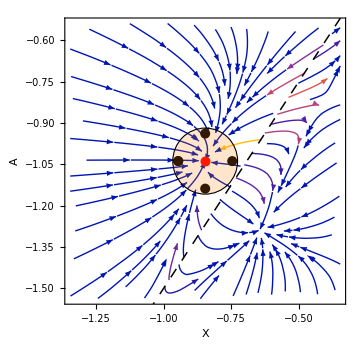

C:\Users\Aiver\Documents\4th Year\Physics 199\Thesis Revision\Figures\linearf3.pdf

```mathematica
linearf3=Show[StreamPlot[{dΧdr/. {K->9/5,λ->1},dAdr/. {K->9/5,λ->1}},{x,f3K95λ1[[1]][[2]]-0.5,f3K95λ1[[1]][[2]]+0.5},{y,f3K95λ1[[2]][[2]]-0.5,f3K95λ1[[2]][[2]]+0.5},StreamPoints->70,StreamScale->Medium,FrameLabel->{Style["X",Black,12],Style["A",Black,12]},FrameStyle->Directive[Black,12,Thickness[0.005]]],

Graphics[{Red,PointSize[0.02],Point/@{{f3K95λ1[[1]][[2]],f3K95λ1[[2]][[2]]}},Red,FontSize->16,Text["",{f3K95λ1[[1]][[2]],f3K95λ1[[2]][[2]]},{1,1}]}],
Plot[3/2 x,{x,-5,5},PlotStyle->Directive[Black,Dashing[0.02],Thickness[0.003]]],
Graphics[{Black,PointSize[0.02],Point/@{{f3K95λ1[[1]][[2]]+1/10,f3K95λ1[[2]][[2]]}},Red,FontSize->14}],

Graphics[{Black,PointSize[0.02],Point/@{{f3K95λ1[[1]][[2]]-1/10,f3K95λ1[[2]][[2]]}},Red,FontSize->14}],

Graphics[{Black,PointSize[0.02],Point/@{{f3K95λ1[[1]][[2]],f3K95λ1[[2]][[2]]-1/10}},Red,FontSize->12}],

Graphics[{Black,PointSize[0.02],Point/@{{f3K95λ1[[1]][[2]]-1/10,f3K95λ1[[2]][[2]]}},Red,FontSize->12}],

Graphics[{Black,PointSize[0.02],Point/@{{f3K95λ1[[1]][[2]],f3K95λ1[[2]][[2]]+1/10}},Red}],

Graphics[{EdgeForm[{Black,Dashing[{0.02}]}],FaceForm[{Orange,Opacity[0.2]}],Disk[{f3K95λ1[[1]][[2]],f3K95λ1[[2]][[2]]},12/100]  }],

ImageSize->Medium]


Export["C:\\Users\\Aiver\\Documents\\4th Year\\Physics 199\\Thesis Revision\\Figures\\linearf3.pdf",linearf3]
```

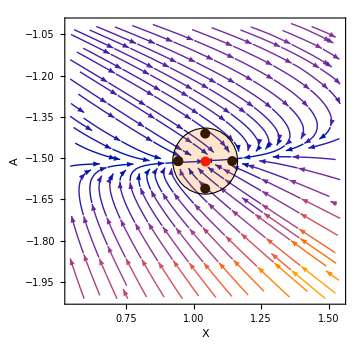

C:\Users\Aiver\Documents\4th Year\Physics 199\Thesis Revision\Figures\linearf4.pdf

```mathematica
linearf4=Show[StreamPlot[{dΧdr/. {K->9/5,λ->1},dAdr/. {K->9/5,λ->1}},{x,f4K95λ1[[1]][[2]]-0.5,f4K95λ1[[1]][[2]]+0.5},{y,f4K95λ1[[2]][[2]]-0.5,f4K95λ1[[2]][[2]]+0.5},StreamPoints->70,StreamScale->Medium,FrameLabel->{Style["X",Black,12],Style["A",Black,12]},FrameStyle->Directive[Black,12,Thickness[0.005]]],

Graphics[{Red,PointSize[0.02],Point/@{{f4K95λ1[[1]][[2]],f4K95λ1[[2]][[2]]}},Red,FontSize->16,Text["",{f4K95λ1[[1]][[2]],f4K95λ1[[2]][[2]]},{1,1}]}],Plot[3/2 x,{x,-5,5},PlotStyle->Directive[White,Dashing[0.02],Thickness[0.003]]],
Graphics[{Black,PointSize[0.02],Point/@{{f4K95λ1[[1]][[2]]+1/10,f4K95λ1[[2]][[2]]}},Red,FontSize->14}],

Graphics[{Black,PointSize[0.02],Point/@{{f4K95λ1[[1]][[2]]-1/10,f4K95λ1[[2]][[2]]}},Red,FontSize->14}],

Graphics[{Black,PointSize[0.02],Point/@{{f4K95λ1[[1]][[2]],f4K95λ1[[2]][[2]]-1/10}},Red,FontSize->12}],

Graphics[{Black,PointSize[0.02],Point/@{{f4K95λ1[[1]][[2]]-1/10,f4K95λ1[[2]][[2]]}},Red,FontSize->12}],

Graphics[{Black,PointSize[0.02],Point/@{{f4K95λ1[[1]][[2]],f4K95λ1[[2]][[2]]+1/10}},Red}],

Graphics[{EdgeForm[{Black,Dashing[{0.02}]}],FaceForm[{Orange,Opacity[0.2]}],Disk[{f4K95λ1[[1]][[2]],f4K95λ1[[2]][[2]]},12/100]  }],

ImageSize->Medium]


Export["C:\\Users\\Aiver\\Documents\\4th Year\\Physics 199\\Thesis Revision\\Figures\\linearf4.pdf",linearf4]
```

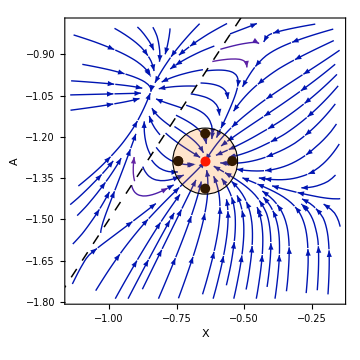

C:\Users\Aiver\Documents\4th Year\Physics 199\Thesis Revision\Figures\linearf5.pdf

```mathematica
linearf5=Show[StreamPlot[{dΧdr/. {K->9/5,λ->1},dAdr/. {K->9/5,λ->1}},{x,f5K95λ1[[1]][[2]]-0.5,f5K95λ1[[1]][[2]]+0.5},{y,f5K95λ1[[2]][[2]]-0.5,f5K95λ1[[2]][[2]]+0.5},StreamPoints->70,StreamScale->Medium,FrameLabel->{Style["X",Black,12],Style["A",Black,12]},FrameStyle->Directive[Black,12,Thickness[0.005]]],

Graphics[{Red,PointSize[0.02],Point/@{{f5K95λ1[[1]][[2]],f5K95λ1[[2]][[2]]}},Red,FontSize->16,Text["",{f5K95λ1[[1]][[2]],f5K95λ1[[2]][[2]]},{1,1}]}],
Plot[3/2 x,{x,-5,5},PlotStyle->Directive[Black,Dashing[0.02],Thickness[0.003]]],
Graphics[{Black,PointSize[0.02],Point/@{{f5K95λ1[[1]][[2]]+1/10,f5K95λ1[[2]][[2]]}},White,FontSize->14}],

Graphics[{Black,PointSize[0.02],Point/@{{f5K95λ1[[1]][[2]]-1/10,f5K95λ1[[2]][[2]]}},White,FontSize->14}],

Graphics[{Black,PointSize[0.02],Point/@{{f5K95λ1[[1]][[2]],f5K95λ1[[2]][[2]]-1/10}},White,FontSize->12}],

Graphics[{Black,PointSize[0.02],Point/@{{f5K95λ1[[1]][[2]]-1/10,f5K95λ1[[2]][[2]]}},White,FontSize->12}],

Graphics[{Black,PointSize[0.02],Point/@{{f5K95λ1[[1]][[2]],f5K95λ1[[2]][[2]]+1/10}},White}],

Graphics[{EdgeForm[{Black,Dashing[{0.02}]}],FaceForm[{Orange,Opacity[0.2]}],Disk[{f5K95λ1[[1]][[2]],f5K95λ1[[2]][[2]]},12/100]  }],

ImageSize->Medium]


Export["C:\\Users\\Aiver\\Documents\\4th Year\\Physics 199\\Thesis Revision\\Figures\\linearf5.pdf",linearf5]
```

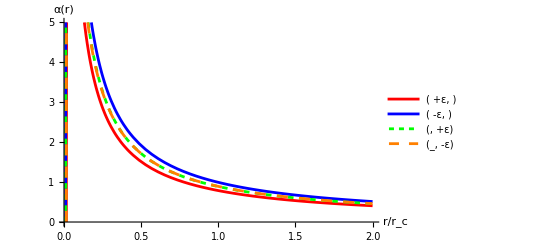

C:\Users\Aiver\Documents\4th Year\Physics 199\Thesis Revision\Figures\f3alpha.pdf

```mathematica
f3alpha=Plot[
{αsolnlinearf3K95λ1AX[[1]][[1]][[2]]/.{C[3]->0,
A->f3K95λ1[[1]][[2]]+1/10,X->f3K95λ1[[2]][[2]]},

αsolnlinearf3K95λ1AX[[1]][[1]][[2]]/.{C[3]->0,
A->f3K95λ1[[1]][[2]]-1/10,X->f3K95λ1[[2]][[2]]},

αsolnlinearf3K95λ1AX[[1]][[1]][[2]]/.{C[3]->0,
A->f3K95λ1[[1]][[2]],X->f3K95λ1[[2]][[2]]+1/10},

αsolnlinearf3K95λ1AX[[1]][[1]][[2]]/.{C[3]->0,
A->f3K95λ1[[1]][[2]],X->f3K95λ1[[2]][[2]]-1/10}

},{r,0,2},PlotRange->{All,{0,5}},
PlotStyle->{Red,Blue,Directive[Green,Dashing[0.01]],Directive[Orange,Dashing[0.02]]},
PlotLegends->Placed[{Style["( +ε, )",Black],Style["( -ε, )",Black],Style["(, +ε)",Black],Style["(_, -ε)",Black]},{Right,Top}],
AxesLabel->{Style["r/r_c",Black,14],Style["α(r)",Black,14]},AxesStyle->Directive[Black, 14,Thickness[0.005]]]

Export["C:\\Users\\Aiver\\Documents\\4th Year\\Physics 199\\Thesis Revision\\Figures\\f3alpha.pdf",f3alpha]
```

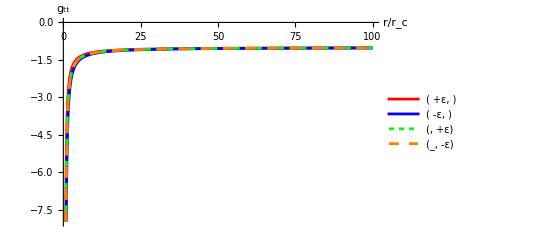

C:\Users\Aiver\Documents\4th Year\Physics 199\Thesis Revision\Figures\gttf3alpha.pdf

```mathematica
gttf3alpha=Plot[
{-Exp[2*αsolnlinearf3K95λ1AX[[1]][[1]][[2]]]/.{C[3]->0,
A->f3K95λ1[[1]][[2]]+1/10,X->f3K95λ1[[2]][[2]]},

-Exp[2*αsolnlinearf3K95λ1AX[[1]][[1]][[2]]]/.{C[3]->0,
A->f3K95λ1[[1]][[2]]-1/10,X->f3K95λ1[[2]][[2]]},

-Exp[2*αsolnlinearf3K95λ1AX[[1]][[1]][[2]]]/.{C[3]->0,
A->f3K95λ1[[1]][[2]],X->f3K95λ1[[2]][[2]]+1/10},

-Exp[2*αsolnlinearf3K95λ1AX[[1]][[1]][[2]]]/.{C[3]->0,
A->f3K95λ1[[1]][[2]],X->f3K95λ1[[2]][[2]]-1/10}

},{r,1/10,100},PlotRange->{All,{-8,0}},
PlotStyle->{Red,Blue,Directive[Green,Dashing[0.01]],Directive[Orange,Dashing[0.02]]},
PlotLegends->Placed[{Style["( +ε, )",Black],Style["( -ε, )",Black],Style["(, +ε)",Black],Style["(_, -ε)",Black]},{Right,Center}],
AxesLabel->{Style["r/r_c",Black,14],Style["g_tt",Black,14]},AxesStyle->Directive[Black, 14,Thickness[0.005]]]

Export["C:\\Users\\Aiver\\Documents\\4th Year\\Physics 199\\Thesis Revision\\Figures\\gttf3alpha.pdf",gttf3alpha]
```

```mathematica
(*Zoomed-in plot is now the inset again*)insetgttf3alpha=Plot[{-Exp[2*αsolnlinearf3K95λ1AX[[1]][[1]][[2]]]/. {C[3]->0,A->f3K95λ1[[1]][[2]]+1/10,X->f3K95λ1[[2]][[2]]},-Exp[2*αsolnlinearf3K95λ1AX[[1]][[1]][[2]]]/. {C[3]->0,A->f3K95λ1[[1]][[2]]-1/10,X->f3K95λ1[[2]][[2]]},-Exp[2*αsolnlinearf3K95λ1AX[[1]][[1]][[2]]]/. {C[3]->0,A->f3K95λ1[[1]][[2]],X->f3K95λ1[[2]][[2]]+1/10},-Exp[2*αsolnlinearf3K95λ1AX[[1]][[1]][[2]]]/. {C[3]->0,A->f3K95λ1[[1]][[2]],X->f3K95λ1[[2]][[2]]-1/10}},{r,1/100,10},PlotRange->{All,{-3,0}},
PlotStyle->{Red,Blue,Directive[Green,Dashing[0.01]],Directive[Orange,Dashing[0.02]]},AxesLabel->{Style["r/r_c",Black,12],Style["g_tt",Black,12]},AxesStyle->Directive[Black,12],ImageSize->Small];

(*Main plot over large r range*)
gttf3alpha=Plot[{-Exp[2*αsolnlinearf3K95λ1AX[[1]][[1]][[2]]]/. {C[3]->0,A->f3K95λ1[[1]][[2]]+1/10,X->f3K95λ1[[2]][[2]]},-Exp[2*αsolnlinearf3K95λ1AX[[1]][[1]][[2]]]/. {C[3]->0,A->f3K95λ1[[1]][[2]]-1/10,X->f3K95λ1[[2]][[2]]},-Exp[2*αsolnlinearf3K95λ1AX[[1]][[1]][[2]]]/. {C[3]->0,A->f3K95λ1[[1]][[2]],X->f3K95λ1[[2]][[2]]+1/10},-Exp[2*αsolnlinearf3K95λ1AX[[1]][[1]][[2]]]/. {C[3]->0,A->f3K95λ1[[1]][[2]],X->f3K95λ1[[2]][[2]]-1/10}},{r,1/100,10^4},PlotRange->{All,{-6,0}},PlotStyle->{Red,Blue,Directive[Green,Dashing[0.01]],Directive[Orange,Dashing[0.02]]},PlotLegends->{Style["(+ε, )",Black],Style["(-ε, )",Black],Style["(, +ε)",Black],Style["(, -ε)",Black]},
AxesLabel->{Style["r/r_c",Black,14],Style["g_tt",Black,14]},AxesStyle->Directive[Black,14,Thickness[0.005]],Epilog->{Inset[Framed[insetgttf3alpha,FrameStyle->Black,RoundingRadius->1],Scaled[{0.6,0.4}],(*adjust as needed*)Center,Scaled[{0.9,0.9}]  (*size of inset*)]}]

Export["C:\\Users\\Aiver\\Documents\\4th Year\\Physics 199\\Thesis Revision\\Figures\\gttf3alpha.pdf",gttf3alpha]
```

-Graphics-

C:\Users\Aiver\Documents\4th Year\Physics 199\Thesis Revision\Figures\gttf3alpha.pdf

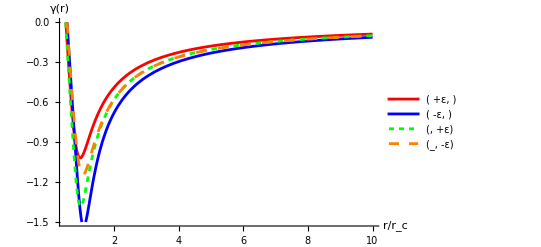

C:\Users\Aiver\Documents\4th Year\Physics 199\Thesis Revision\Figures\f3gamma.pdf

```mathematica
f3gamma=Plot[
{γsolnlinearf3K95λ1AX/.{
A->f3K95λ1[[1]][[2]]+1/10,X->f3K95λ1[[2]][[2]]},

γsolnlinearf3K95λ1AX/.{
A->f3K95λ1[[1]][[2]]-1/10,X->f3K95λ1[[2]][[2]]},

γsolnlinearf3K95λ1AX/.{
A->f3K95λ1[[1]][[2]],X->f3K95λ1[[2]][[2]]+1/10},

γsolnlinearf3K95λ1AX/.{
A->f3K95λ1[[1]][[2]],X->f3K95λ1[[2]][[2]]-1/10}

},{r,0,10},PlotRange->{All,{-1.5,0}},
PlotStyle->{Red,Blue,Directive[Green,Dashing[0.01]],Directive[Orange,Dashing[0.02]]},
PlotLegends->Placed[{Style["( +ε, )",Black],Style["( -ε, )",Black],Style["(, +ε)",Black],Style["(_, -ε)",Black]},{Right,Center}],
AxesLabel->{Style["r/r_c",Black,14],Style["γ(r)",Black,14]},AxesStyle->Directive[Black, 14,Thickness[0.005]]]

Export["C:\\Users\\Aiver\\Documents\\4th Year\\Physics 199\\Thesis Revision\\Figures\\f3gamma.pdf",f3gamma]
```

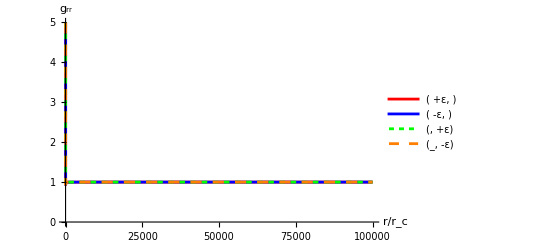

```mathematica
grrf3gamma=Plot[
{Exp[2*γsolnlinearf3K95λ1AX]/.{
A->f3K95λ1[[1]][[2]]+1/10,X->f3K95λ1[[2]][[2]]},

Exp[2*γsolnlinearf3K95λ1AX]/.{
A->f3K95λ1[[1]][[2]]-1/10,X->f3K95λ1[[2]][[2]]},

Exp[2*γsolnlinearf3K95λ1AX]/.{
A->f3K95λ1[[1]][[2]],X->f3K95λ1[[2]][[2]]+1/10},

Exp[2*γsolnlinearf3K95λ1AX]/.{
A->f3K95λ1[[1]][[2]],X->f3K95λ1[[2]][[2]]-1/10}

},{r,0,10^5},PlotRange->{All,{0,5}},
PlotStyle->{Red,Blue,Directive[Green,Dashing[0.01]],Directive[Orange,Dashing[0.02]]},
PlotLegends->{Style["( +ε, )",Black],Style["( -ε, )",Black],Style["(, +ε)",Black],Style["(_, -ε)",Black]},
AxesLabel->{Style["r/r_c",Black,14],Style["g_rr",Black,14]},AxesStyle->Directive[Black, 14,Thickness[0.005]]]
```

```mathematica
insetgrrf3gamma=Plot[{Exp[2*γsolnlinearf3K95λ1AX]/. {A->f3K95λ1[[1]][[2]]+1/10,X->f3K95λ1[[2]][[2]]},Exp[2*γsolnlinearf3K95λ1AX]/. {A->f3K95λ1[[1]][[2]]-1/10,X->f3K95λ1[[2]][[2]]},Exp[2*γsolnlinearf3K95λ1AX]/. {A->f3K95λ1[[1]][[2]],X->f3K95λ1[[2]][[2]]+1/10},Exp[2*γsolnlinearf3K95λ1AX]/. {A->f3K95λ1[[1]][[2]],X->f3K95λ1[[2]][[2]]-1/10}},{r,0,10},PlotRange->{All,{0,1}},PlotStyle->{Red,Blue,Directive[Green,Dashing[0.01]],Directive[Orange,Dashing[0.02]]},AxesStyle->Directive[Black,10],AxesLabel->{Style["r/r_c",Black,14],Style["g_rr",Black,14]},AxesStyle->Directive[Black, 14,Thickness[0.005]]];

grrf3gamma=Show[grrf3gamma,Epilog->{Inset[Framed[insetgrrf3gamma,FrameStyle->Black,RoundingRadius->1],Scaled[{0.6,0.6}],(*inset location in main plot*)Center,Scaled[{0.8,0.8}]   (*inset size relative to main plot*)]}]
(*Export["C:\\Users\\Aiver\\Documents\\4th Year\\Physics 199\\Thesis Revision\\Figures\\gttf3gamma.pdf",gttf3gamma]*)

Export["C:\\Users\\Aiver\\Documents\\4th Year\\Physics 199\\Thesis Revision\\Figures\\grrf3gamma.pdf",grrf3gamma]
```

-Graphics-

C:\Users\Aiver\Documents\4th Year\Physics 199\Thesis Revision\Figures\grrf3gamma.pdf

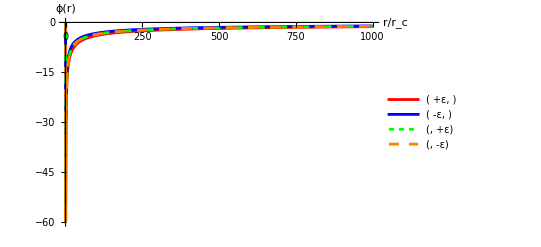

```mathematica
f4phi=Plot[
{ϕsolnlinearf4K95λ1AX[[1]][[1]][[2]]/.{C[3]->0,
A->f4K95λ1[[1]][[2]]+1/10,X->f4K95λ1[[2]][[2]]},

ϕsolnlinearf4K95λ1AX[[1]][[1]][[2]]/.{C[3]->0,
A->f4K95λ1[[1]][[2]]-1/10,X->f4K95λ1[[2]][[2]]},

ϕsolnlinearf4K95λ1AX[[1]][[1]][[2]]/.{C[3]->0,
A->f4K95λ1[[1]][[2]],X->f4K95λ1[[2]][[2]]+1/10},

ϕsolnlinearf4K95λ1AX[[1]][[1]][[2]]/.{C[3]->0,
A->f4K95λ1[[1]][[2]],X->f4K95λ1[[2]][[2]]-1/10}

},{r,0,10^3},PlotRange->{All,{-60,0}},
PlotStyle->{Red,Blue,Directive[Green,Dashing[0.01]],Directive[Orange,Dashing[0.02]]},
PlotLegends->{Style["( +ε, )",Black],Style["( -ε, )",Black],Style["(, +ε)",Black],Style["(, -ε)",Black]},
AxesLabel->{Style["r/r_c",Black,14],Style["ϕ(r)",Black,14]},AxesStyle->Directive[Black, 14,Thickness[0.005]]]
```

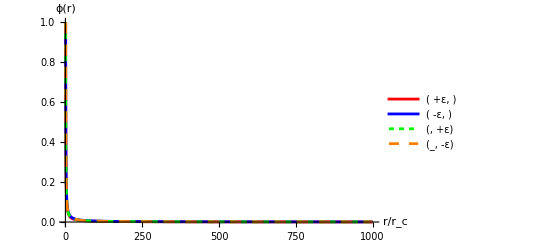

```mathematica
f3phi=Plot[
{ϕsolnlinearf3K95λ1AX[[1]][[1]][[2]]/.{C[3]->0,
A->f3K95λ1[[1]][[2]]+1/10,X->f3K95λ1[[2]][[2]]},

ϕsolnlinearf3K95λ1AX[[1]][[1]][[2]]/.{C[3]->0,
A->f3K95λ1[[1]][[2]]-1/10,X->f3K95λ1[[2]][[2]]},

ϕsolnlinearf3K95λ1AX[[1]][[1]][[2]]/.{C[3]->0,
A->f3K95λ1[[1]][[2]],X->f3K95λ1[[2]][[2]]+1/10},

ϕsolnlinearf3K95λ1AX[[1]][[1]][[2]]/.{C[3]->0,
A->f3K95λ1[[1]][[2]],X->f3K95λ1[[2]][[2]]-1/10}

},{r,0,10^3},PlotRange->{All,{0,1}},
PlotStyle->{Red,Blue,Directive[Green,Dashing[0.01]],Directive[Orange,Dashing[0.02]]},
PlotLegends->{Style["( +ε, )",Black],Style["( -ε, )",Black],Style["(, +ε)",Black],Style["(_, -ε)",Black]},
AxesLabel->{Style["r/r_c",Black,14],Style["ϕ(r)",Black,14]},AxesStyle->Directive[Black, 14,Thickness[0.005]]]
```

```mathematica
insetf3phi=Plot[
{ϕsolnlinearf3K95λ1AX[[1]][[1]][[2]]/.{C[3]->0,
A->f3K95λ1[[1]][[2]]+1/10,X->f3K95λ1[[2]][[2]]},

ϕsolnlinearf3K95λ1AX[[1]][[1]][[2]]/.{C[3]->0,
A->f3K95λ1[[1]][[2]]-1/10,X->f3K95λ1[[2]][[2]]},

ϕsolnlinearf3K95λ1AX[[1]][[1]][[2]]/.{C[3]->0,
A->f3K95λ1[[1]][[2]],X->f3K95λ1[[2]][[2]]+1/10},

ϕsolnlinearf3K95λ1AX[[1]][[1]][[2]]/.{C[3]->0,
A->f3K95λ1[[1]][[2]],X->f3K95λ1[[2]][[2]]-1/10}

},{r,0,3},PlotRange->{All,{0,3}},
PlotStyle->{Red,Blue,Directive[Green,Dashing[0.01]],Directive[Orange,Dashing[0.02]]},AxesLabel->{Style["r/r_c",Black,12],Style["ϕ(r)",Black,12]},AxesStyle->Directive[Black,12],ImageSize->Small];

f3phi=Show[f3phi,Epilog->{Inset[Framed[insetf3phi,FrameStyle->Black,RoundingRadius->1],Scaled[{0.6,0.6}],(*inset location in main plot*)Center,Scaled[{0.95,0.95}]   (*inset size relative to main plot*)]}]

Export["C:\\Users\\Aiver\\Documents\\4th Year\\Physics 199\\Thesis Revision\\Figures\\f3phi.pdf",f3phi]
```

-Graphics-

C:\Users\Aiver\Documents\4th Year\Physics 199\Thesis Revision\Figures\f3phi.pdf

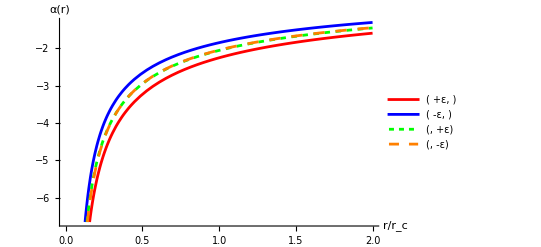

C:\Users\Aiver\Documents\4th Year\Physics 199\Thesis Revision\Figures\f4alpha.pdf

```mathematica
f4alpha=Plot[
{αsolnlinearf4K95λ1AX[[1]][[1]][[2]]/.{C[3]->0,
A->f4K95λ1[[1]][[2]]+1/10,X->f4K95λ1[[2]][[2]]},

αsolnlinearf4K95λ1AX[[1]][[1]][[2]]/.{C[3]->0,
A->f4K95λ1[[1]][[2]]-1/10,X->f4K95λ1[[2]][[2]]},

αsolnlinearf4K95λ1AX[[1]][[1]][[2]]/.{C[3]->0,
A->f4K95λ1[[1]][[2]],X->f4K95λ1[[2]][[2]]+1/10},

αsolnlinearf4K95λ1AX[[1]][[1]][[2]]/.{C[3]->0,
A->f4K95λ1[[1]][[2]],X->f4K95λ1[[2]][[2]]-1/10}

},{r,0,2},
PlotStyle->{Red,Blue,Directive[Green,Dashing[0.01]],Directive[Orange,Dashing[0.02]]},
PlotLegends->Placed[{Style["( +ε, )",Black],Style["( -ε, )",Black],Style["(, +ε)",Black],Style["(, -ε)",Black]},{Right,Center
}],
AxesLabel->{Style["r/r_c",Black,14],Style["α(r)",Black,14]},AxesStyle->Directive[Black, 14,Thickness[0.005]]]

Export["C:\\Users\\Aiver\\Documents\\4th Year\\Physics 199\\Thesis Revision\\Figures\\f4alpha.pdf",f4alpha]
```

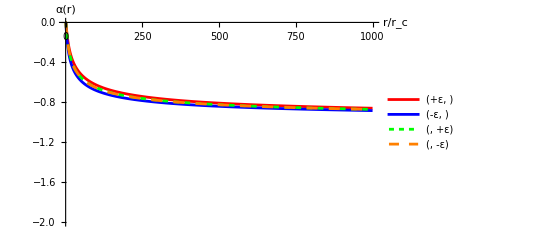

```mathematica
Plot[
{-Exp[2*αsolnlinearf4K95λ1AX[[1]][[1]][[2]]]/.{C[3]->0,
A->f4K95λ1[[1]][[2]]+1/10,X->f4K95λ1[[2]][[2]]},

-Exp[2*αsolnlinearf4K95λ1AX[[1]][[1]][[2]]]/.{C[3]->0,
A->f4K95λ1[[1]][[2]]-1/10,X->f4K95λ1[[2]][[2]]},

-Exp[2*αsolnlinearf4K95λ1AX[[1]][[1]][[2]]]/.{C[3]->0,
A->f4K95λ1[[1]][[2]],X->f4K95λ1[[2]][[2]]+1/10},

-Exp[2*αsolnlinearf4K95λ1AX[[1]][[1]][[2]]]/.{C[3]->0,
A->f4K95λ1[[1]][[2]],X->f4K95λ1[[2]][[2]]-1/10}

},{r,1/100,10^3},PlotRange->{All,{-2,0}},
PlotStyle->{Red,Blue,Directive[Green,Dashing[0.01]],Directive[Orange,Dashing[0.02]]},
PlotLegends->Placed[{Style["(+ε, )",Black],Style["(-ε, )",Black],Style["(, +ε)",Black],Style["(, -ε)",Black]},{Right,Bottom
}],
AxesLabel->{Style["r/r_c",Black,14],Style["α(r)",Black,14]},AxesStyle->Directive[Black, 14,Thickness[0.005]]]
```

```mathematica
(*Zoomed-in plot is now the inset again*)insetgttf4alpha=Plot[{-Exp[2*αsolnlinearf4K95λ1AX[[1]][[1]][[2]]]/. {C[3]->0,A->f4K95λ1[[1]][[2]]+1/10,X->f5K95λ1[[2]][[2]]},-Exp[2*αsolnlinearf4K95λ1AX[[1]][[1]][[2]]]/. {C[3]->0,A->f4K95λ1[[1]][[2]]-1/10,X->f4K95λ1[[2]][[2]]},-Exp[2*αsolnlinearf4K95λ1AX[[1]][[1]][[2]]]/. {C[3]->0,A->f4K95λ1[[1]][[2]],X->f4K95λ1[[2]][[2]]+1/10},-Exp[2*αsolnlinearf4K95λ1AX[[1]][[1]][[2]]]/. {C[3]->0,A->f4K95λ1[[1]][[2]],X->f4K95λ1[[2]][[2]]-1/10}},{r,1/100,100},PlotRange->{All,{-1,0}},
PlotStyle->{Red,Blue,Directive[Green,Dashing[0.01]],Directive[Orange,Dashing[0.02]]},AxesLabel->{Style["r/r_c",Black,12],Style["g_tt",Black,12]},AxesStyle->Directive[Black,12],ImageSize->Small];

(*Main plot over large r range*)
gttf4alpha=Plot[{-Exp[2*αsolnlinearf4K95λ1AX[[1]][[1]][[2]]]/. {C[3]->0,A->f4K95λ1[[1]][[2]]+1/10,X->f5K95λ1[[2]][[2]]},-Exp[2*αsolnlinearf4K95λ1AX[[1]][[1]][[2]]]/. {C[3]->0,A->f4K95λ1[[1]][[2]]-1/10,X->f4K95λ1[[2]][[2]]},-Exp[2*αsolnlinearf4K95λ1AX[[1]][[1]][[2]]]/. {C[3]->0,A->f4K95λ1[[1]][[2]],X->f4K95λ1[[2]][[2]]+1/10},-Exp[2*αsolnlinearf4K95λ1AX[[1]][[1]][[2]]]/. {C[3]->0,A->f4K95λ1[[1]][[2]],X->f4K95λ1[[2]][[2]]-1/10}},{r,1/100,10^4},PlotRange->{All,{-6,0}},PlotStyle->{Red,Blue,Directive[Green,Dashing[0.01]],Directive[Orange,Dashing[0.02]]},PlotLegends->{Style["(+ε, )",Black],Style["(-ε, )",Black],Style["(, +ε)",Black],Style["(, -ε)",Black]},
AxesLabel->{Style["r/r_c",Black,14],Style["g_tt",Black,14]},AxesStyle->Directive[Black,14,Thickness[0.005]],Epilog->{Inset[Framed[insetgttf4alpha,FrameStyle->Black,RoundingRadius->1],Scaled[{0.6,0.4}],(*adjust as needed*)Center,Scaled[{0.9,0.9}]  (*size of inset*)]}]

Export["C:\\Users\\Aiver\\Documents\\4th Year\\Physics 199\\Thesis Revision\\Figures\\gttf4alpha.pdf",gttf4alpha]
```

-Graphics-

C:\Users\Aiver\Documents\4th Year\Physics 199\Thesis Revision\Figures\gttf4alpha.pdf

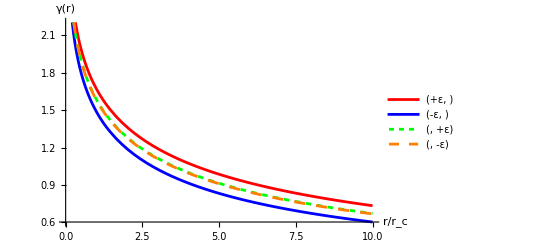

C:\Users\Aiver\Documents\4th Year\Physics 199\Thesis Revision\Figures\f4gamma.pdf

```mathematica
f4gamma=Plot[
{γsolnlinearf4K95λ1AX/.{
A->f4K95λ1[[1]][[2]]+1/10,X->f4K95λ1[[2]][[2]]},

γsolnlinearf4K95λ1AX/.{
A->f4K95λ1[[1]][[2]]-1/10,X->f4K95λ1[[2]][[2]]},

γsolnlinearf4K95λ1AX/.{
A->f4K95λ1[[1]][[2]],X->f4K95λ1[[2]][[2]]+1/10},

γsolnlinearf4K95λ1AX/.{
A->f4K95λ1[[1]][[2]],X->f4K95λ1[[2]][[2]]-1/10}

},{r,0,10},
PlotStyle->{Red,Blue,Directive[Green,Dashing[0.01]],Directive[Orange,Dashing[0.02]]},
PlotLegends->Placed[{Style["(+ε, )",Black],Style["(-ε, )",Black],Style["(, +ε)",Black],Style["(, -ε)",Black]},{Right,Top}],
AxesLabel->{Style["r/r_c",Black,14],Style["γ(r)",Black,14]},AxesStyle->Directive[Black, 14,Thickness[0.005]]]

Export["C:\\Users\\Aiver\\Documents\\4th Year\\Physics 199\\Thesis Revision\\Figures\\f4gamma.pdf",f4gamma]
```

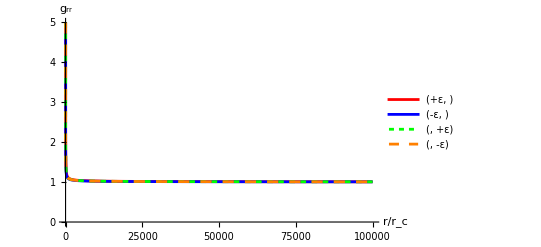

```mathematica
grrf4gamma=Plot[
{Exp[2*γsolnlinearf4K95λ1AX]/.{
A->f4K95λ1[[1]][[2]]+1/10,X->f4K95λ1[[2]][[2]]},

Exp[2*γsolnlinearf4K95λ1AX]/.{
A->f4K95λ1[[1]][[2]]-1/10,X->f4K95λ1[[2]][[2]]},

Exp[2*γsolnlinearf4K95λ1AX]/.{
A->f4K95λ1[[1]][[2]],X->f4K95λ1[[2]][[2]]+1/10},

Exp[2*γsolnlinearf4K95λ1AX]/.{
A->f4K95λ1[[1]][[2]],X->f4K95λ1[[2]][[2]]-1/10}

},{r,0,10^5},PlotRange->{All,{0,5}},
PlotStyle->{Red,Blue,Directive[Green,Dashing[0.01]],Directive[Orange,Dashing[0.02]]},
PlotLegends->{Style["(+ε, )",Black],Style["(-ε, )",Black],Style["(, +ε)",Black],Style["(, -ε)",Black]},
AxesLabel->{Style["r/r_c",Black,14],Style["g_rr",Black,14]},AxesStyle->Directive[Black, 14,Thickness[0.005]]]
```

```mathematica
insetgrrf4gamma=
Plot[{Exp[2*γsolnlinearf4K95λ1AX]/.{
A->f4K95λ1[[1]][[2]]+1/10,X->f4K95λ1[[2]][[2]]},

Exp[2*γsolnlinearf4K95λ1AX]/.{
A->f4K95λ1[[1]][[2]]-1/10,X->f4K95λ1[[2]][[2]]},

Exp[2*γsolnlinearf4K95λ1AX]/.{
A->f4K95λ1[[1]][[2]],X->f4K95λ1[[2]][[2]]+1/10},

Exp[2*γsolnlinearf4K95λ1AX]/.{
A->f4K95λ1[[1]][[2]],X->f4K95λ1[[2]][[2]]-1/10}

},{r,0,50},PlotRange->{All,{0,5}},
PlotStyle->{Red,Blue,Directive[Green,Dashing[0.01]],Directive[Orange,Dashing[0.02]]},AxesLabel->{Style["r/r_c",Black,12],Style["g_rr",Black,12]},AxesStyle->Directive[Black,12],ImageSize->Small];

grrf4gamma=Show[grrf4gamma,Epilog->{Inset[Framed[insetgrrf4gamma,FrameStyle->Black,RoundingRadius->1],Scaled[{0.6,0.6}],(*inset location in main plot*)Center,Scaled[{0.95,0.95}]   (*inset size relative to main plot*)]}]
(*Export["C:\\Users\\Aiver\\Documents\\4th Year\\Physics 199\\Thesis Revision\\Figures\\gttf3gamma.pdf",gttf3gamma]*)

Export["C:\\Users\\Aiver\\Documents\\4th Year\\Physics 199\\Thesis Revision\\Figures\\grrf4gamma.pdf",grrf4gamma]
```

-Graphics-

C:\Users\Aiver\Documents\4th Year\Physics 199\Thesis Revision\Figures\grrf4gamma.pdf

```mathematica
f4phi=Plot[
{ϕsolnlinearf4K95λ1AX[[1]][[1]][[2]]/.{C[3]->0,
A->f4K95λ1[[1]][[2]]+1/10,X->f4K95λ1[[2]][[2]]},

ϕsolnlinearf4K95λ1AX[[1]][[1]][[2]]/.{C[3]->0,
A->f4K95λ1[[1]][[2]]-1/10,X->f4K95λ1[[2]][[2]]},

ϕsolnlinearf4K95λ1AX[[1]][[1]][[2]]/.{C[3]->0,
A->f4K95λ1[[1]][[2]],X->f4K95λ1[[2]][[2]]+1/10},

ϕsolnlinearf4K95λ1AX[[1]][[1]][[2]]/.{C[3]->0,
A->f4K95λ1[[1]][[2]],X->f4K95λ1[[2]][[2]]-1/10}

},{r,0,10^3},PlotRange->{All,{-60,0}},
PlotStyle->{Red,Blue,Directive[Green,Dashing[0.01]],Directive[Orange,Dashing[0.02]]},
PlotLegends->{Style["( +ε, )",Black],Style["( -ε, )",Black],Style["(, +ε)",Black],Style["(, -ε)",Black]},
AxesLabel->{Style["r/r_c",Black,14],Style["ϕ(r)",Black,14]},AxesStyle->Directive[Black, 14,Thickness[0.005]]]
```

-Graphics-

```mathematica
insetf4phi=Plot[
{ϕsolnlinearf4K95λ1AX[[1]][[1]][[2]]/.{C[3]->0,
A->f4K95λ1[[1]][[2]]+1/10,X->f4K95λ1[[2]][[2]]},

ϕsolnlinearf4K95λ1AX[[1]][[1]][[2]]/.{C[3]->0,
A->f4K95λ1[[1]][[2]]-1/10,X->f4K95λ1[[2]][[2]]},

ϕsolnlinearf4K95λ1AX[[1]][[1]][[2]]/.{C[3]->0,
A->f4K95λ1[[1]][[2]],X->f4K95λ1[[2]][[2]]+1/10},

ϕsolnlinearf4K95λ1AX[[1]][[1]][[2]]/.{C[3]->0,
A->f4K95λ1[[1]][[2]],X->f4K95λ1[[2]][[2]]-1/10}

},{r,0,20},PlotRange->{All,{-20,0}},
PlotStyle->{Red,Blue,Directive[Green,Dashing[0.01]],Directive[Orange,Dashing[0.02]]},AxesLabel->{Style["r/r_c",Black,12],Style["ϕ(r)",Black,12]},AxesStyle->Directive[Black,12],ImageSize->Small];

f4phi=Show[f4phi,Epilog->{Inset[Framed[insetf4phi,FrameStyle->Black,RoundingRadius->1],Scaled[{0.6,0.4}],(*inset location in main plot*)Center,Scaled[{0.95,0.95}]   (*inset size relative to main plot*)]}]

Export["C:\\Users\\Aiver\\Documents\\4th Year\\Physics 199\\Thesis Revision\\Figures\\f4phi.pdf",f4phi]
```

-Graphics-

C:\Users\Aiver\Documents\4th Year\Physics 199\Thesis Revision\Figures\f4phi.pdf

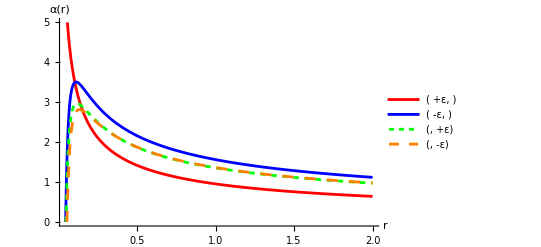

C:\Users\Aiver\Documents\4th Year\Physics 199\Thesis Revision\Figures\f5alpha.pdf

```mathematica
f5alpha=Plot[
{αsolnlinearf5K95λ1AX[[1]][[1]][[2]]/.{C[3]->0,
A->f5K95λ1[[1]][[2]]+1/10,X->f5K95λ1[[2]][[2]]},

αsolnlinearf4K95λ1AX[[1]][[1]][[2]]/.{C[3]->0,
A->f5K95λ1[[1]][[2]]-1/10,X->f5K95λ1[[2]][[2]]},

αsolnlinearf4K95λ1AX[[1]][[1]][[2]]/.{C[3]->0,
A->f5K95λ1[[1]][[2]],X->f5K95λ1[[2]][[2]]+1/10},

αsolnlinearf4K95λ1AX[[1]][[1]][[2]]/.{C[3]->0,
A->f5K95λ1[[1]][[2]],X->f5K95λ1[[2]][[2]]-1/10}

},{r,0,2},PlotRange->{All,{0,5}},
PlotStyle->{Red,Blue,Directive[Green,Dashing[0.01]],Directive[Orange,Dashing[0.02]]},
PlotLegends->Placed[{Style["( +ε, )",Black],Style["( -ε, )",Black],Style["(, +ε)",Black],Style["(, -ε)",Black]},{Right,Top
}],
AxesLabel->{Style["r",Black,14],Style["α(r)",Black,14]},AxesStyle->Directive[Black, 14,Thickness[0.005]]]

Export["C:\\Users\\Aiver\\Documents\\4th Year\\Physics 199\\Thesis Revision\\Figures\\f5alpha.pdf",f5alpha]
```

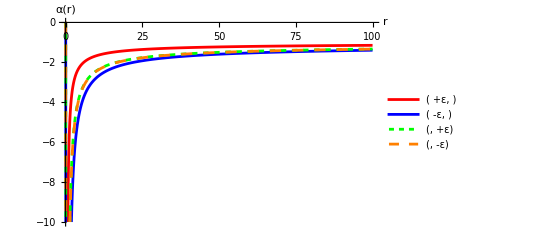

```mathematica
Plot[
{-Exp[2*αsolnlinearf5K95λ1AX[[1]][[1]][[2]]]/.{C[3]->0,
A->f5K95λ1[[1]][[2]]+1/10,X->f5K95λ1[[2]][[2]]},

-Exp[2*αsolnlinearf4K95λ1AX[[1]][[1]][[2]]]/.{C[3]->0,
A->f5K95λ1[[1]][[2]]-1/10,X->f5K95λ1[[2]][[2]]},

-Exp[2*αsolnlinearf4K95λ1AX[[1]][[1]][[2]]]/.{C[3]->0,
A->f5K95λ1[[1]][[2]],X->f5K95λ1[[2]][[2]]+1/10},

-Exp[2*αsolnlinearf4K95λ1AX[[1]][[1]][[2]]]/.{C[3]->0,
A->f5K95λ1[[1]][[2]],X->f5K95λ1[[2]][[2]]-1/10}

},{r,1/100,100},PlotRange->{All,{-10,0}},
PlotStyle->{Red,Blue,Directive[Green,Dashing[0.01]],Directive[Orange,Dashing[0.02]]},
PlotLegends->Placed[{Style["( +ε, )",Black],Style["( -ε, )",Black],Style["(, +ε)",Black],Style["(, -ε)",Black]},{Right,Center
}],
AxesLabel->{Style["r",Black,14],Style["α(r)",Black,14]},AxesStyle->Directive[Black, 14,Thickness[0.005]]]
```

```mathematica
(*Zoomed-in plot is now the inset again*)insetgttf5alpha=Plot[{-Exp[2*αsolnlinearf5K95λ1AX[[1]][[1]][[2]]]/. {C[3]->0,A->f5K95λ1[[1]][[2]]+1/10,X->f5K95λ1[[2]][[2]]},-Exp[2*αsolnlinearf5K95λ1AX[[1]][[1]][[2]]]/. {C[3]->0,A->f5K95λ1[[1]][[2]]-1/10,X->f5K95λ1[[2]][[2]]},-Exp[2*αsolnlinearf5K95λ1AX[[1]][[1]][[2]]]/. {C[3]->0,A->f5K95λ1[[1]][[2]],X->f5K95λ1[[2]][[2]]+1/10},-Exp[2*αsolnlinearf5K95λ1AX[[1]][[1]][[2]]]/. {C[3]->0,A->f5K95λ1[[1]][[2]],X->f5K95λ1[[2]][[2]]-1/10}},{r,1/100,10},PlotRange->{All,{-10,0}},FrameTicks->{{None,None},{None,None}},
PlotStyle->{Red,Blue,Directive[Green,Dashing[0.01]],Directive[Orange,Dashing[0.02]]},AxesLabel->{Style["r/r_c",Black,12],Style["g_tt",Black,12]},AxesStyle->Directive[Black,12],ImageSize->Small];

(*Main plot over large r range*)
gttf5alpha=Plot[{-Exp[2*αsolnlinearf5K95λ1AX[[1]][[1]][[2]]]/. {C[3]->0,A->f5K95λ1[[1]][[2]]+1/10,X->f5K95λ1[[2]][[2]]},-Exp[2*αsolnlinearf5K95λ1AX[[1]][[1]][[2]]]/. {C[3]->0,A->f5K95λ1[[1]][[2]]-1/10,X->f5K95λ1[[2]][[2]]},-Exp[2*αsolnlinearf5K95λ1AX[[1]][[1]][[2]]]/. {C[3]->0,A->f5K95λ1[[1]][[2]],X->f5K95λ1[[2]][[2]]+1/10},-Exp[2*αsolnlinearf5K95λ1AX[[1]][[1]][[2]]]/. {C[3]->0,A->f5K95λ1[[1]][[2]],X->f5K95λ1[[2]][[2]]-1/10}},{r,1/100,10^4},PlotRange->{All,{-6,0}},PlotStyle->{Red,Blue,Directive[Green,Dashing[0.01]],Directive[Orange,Dashing[0.02]]},PlotLegends->{Style["(+ε, )",Black],Style["(-ε, )",Black],Style["(, +ε)",Black],Style["(, -ε)",Black]},
AxesLabel->{Style["r/r_c",Black,14],Style["g_tt",Black,14]},AxesStyle->Directive[Black,14,Thickness[0.005]],Epilog->{Inset[Framed[insetgttf4alpha,FrameStyle->Black,RoundingRadius->1],Scaled[{0.6,0.4}],(*adjust as needed*)Center,Scaled[{0.95,0.95}]  (*size of inset*)]}]

Export["C:\\Users\\Aiver\\Documents\\4th Year\\Physics 199\\Thesis Revision\\Figures\\gttf5alpha.pdf",gttf5alpha]
```

-Graphics-

C:\Users\Aiver\Documents\4th Year\Physics 199\Thesis Revision\Figures\gttf5alpha.pdf

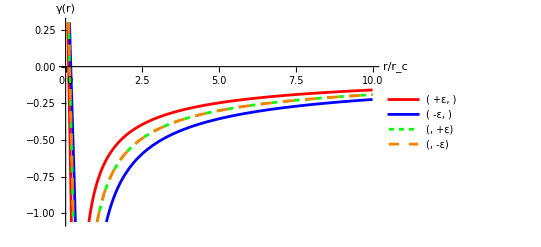

C:\Users\Aiver\Documents\4th Year\Physics 199\Thesis Revision\Figures\f5gamma.pdf

```mathematica
f5gamma=Plot[
{γsolnlinearf5K95λ1AX/.{
A->f5K95λ1[[1]][[2]]+1/10,X->f5K95λ1[[2]][[2]]},

γsolnlinearf5K95λ1AX/.{
A->f5K95λ1[[1]][[2]]-1/10,X->f5K95λ1[[2]][[2]]},

γsolnlinearf5K95λ1AX/.{
A->f5K95λ1[[1]][[2]],X->f5K95λ1[[2]][[2]]+1/10},

γsolnlinearf5K95λ1AX/.{
A->f5K95λ1[[1]][[2]],X->f5K95λ1[[2]][[2]]-1/10}

},{r,0,10},
PlotStyle->{Red,Blue,Directive[Green,Dashing[0.01]],Directive[Orange,Dashing[0.02]]},
PlotLegends->Placed[{Style["( +ε, )",Black],Style["( -ε, )",Black],Style["(, +ε)",Black],Style["(, -ε)",Black]},{Right,Bottom
}],
AxesLabel->{Style["r/r_c",Black,14],Style["γ(r)",Black,14]},AxesStyle->Directive[Black, 14,Thickness[0.005]]]

Export["C:\\Users\\Aiver\\Documents\\4th Year\\Physics 199\\Thesis Revision\\Figures\\f5gamma.pdf",f5gamma]
```

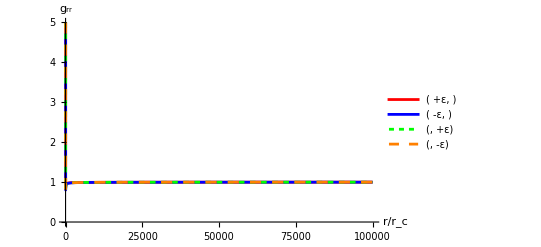

```mathematica
grrf5gamma=Plot[
{Exp[2*γsolnlinearf5K95λ1AX]/.{
A->f5K95λ1[[1]][[2]]+1/10,X->f5K95λ1[[2]][[2]]},

Exp[2*γsolnlinearf5K95λ1AX]/.{
A->f5K95λ1[[1]][[2]]-1/10,X->f5K95λ1[[2]][[2]]},

Exp[2*γsolnlinearf5K95λ1AX]/.{
A->f5K95λ1[[1]][[2]],X->f5K95λ1[[2]][[2]]+1/10},

Exp[2*γsolnlinearf5K95λ1AX]/.{
A->f5K95λ1[[1]][[2]],X->f5K95λ1[[2]][[2]]-1/10}

},{r,0,10^5},PlotRange->{All,{0,5}},
PlotStyle->{Red,Blue,Directive[Green,Dashing[0.01]],Directive[Orange,Dashing[0.02]]},
PlotLegends->{Style["( +ε, )",Black],Style["( -ε, )",Black],Style["(, +ε)",Black],Style["(, -ε)",Black]},
AxesLabel->{Style["r/r_c",Black,14],Style["g_rr",Black,14]},AxesStyle->Directive[Black, 14,Thickness[0.005]]]
```

```mathematica
insetgrrf5gamma=Plot[
{Exp[2*γsolnlinearf5K95λ1AX]/.{
A->f5K95λ1[[1]][[2]]+1/10,X->f5K95λ1[[2]][[2]]},

Exp[2*γsolnlinearf5K95λ1AX]/.{
A->f5K95λ1[[1]][[2]]-1/10,X->f5K95λ1[[2]][[2]]},

Exp[2*γsolnlinearf5K95λ1AX]/.{
A->f5K95λ1[[1]][[2]],X->f5K95λ1[[2]][[2]]+1/10},

Exp[2*γsolnlinearf5K95λ1AX]/.{
A->f5K95λ1[[1]][[2]],X->f5K95λ1[[2]][[2]]-1/10}

},{r,0,10},PlotRange->{All,{0,1}},
PlotStyle->{Red,Blue,Directive[Green,Dashing[0.01]],Directive[Orange,Dashing[0.02]]},AxesLabel->{Style["r/r_c",Black,12],Style["g_rr",Black,12]},AxesStyle->Directive[Black,12],ImageSize->Small];

grrf5gamma=Show[grrf5gamma,Epilog->{Inset[Framed[insetgrrf5gamma,FrameStyle->Black,RoundingRadius->1],Scaled[{0.6,0.6}],(*inset location in main plot*)Center,Scaled[{0.95,0.95}]   (*inset size relative to main plot*)]}]

Export["C:\\Users\\Aiver\\Documents\\4th Year\\Physics 199\\Thesis Revision\\Figures\\grrf5gamma.pdf",grrf5gamma]
```

-Graphics-

C:\Users\Aiver\Documents\4th Year\Physics 199\Thesis Revision\Figures\grrf5gamma.pdf

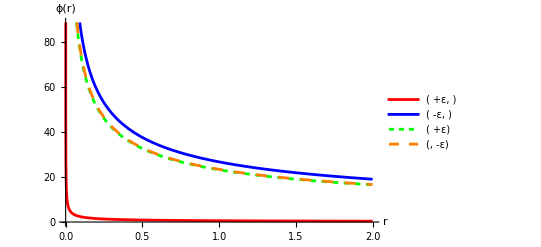

C:\Users\Aiver\Documents\4th Year\Physics 199\Thesis Revision\Figures\f5phi.pdf

```mathematica
f5phi=Plot[
{ϕsolnlinearf5K95λ1AX[[1]][[1]][[2]]/.{C[3]->0,
A->f5K95λ1[[1]][[2]]+1/10,X->f5K95λ1[[2]][[2]]},

ϕsolnlinearf4K95λ1AX[[1]][[1]][[2]]/.{C[3]->0,
A->f5K95λ1[[1]][[2]]-1/10,X->f5K95λ1[[2]][[2]]},

ϕsolnlinearf4K95λ1AX[[1]][[1]][[2]]/.{C[3]->0,
A->f5K95λ1[[1]][[2]],X->f5K95λ1[[2]][[2]]+1/10},

ϕsolnlinearf4K95λ1AX[[1]][[1]][[2]]/.{C[3]->0,
A->f5K95λ1[[1]][[2]],X->f5K95λ1[[2]][[2]]-1/10}

},{r,0,2},
PlotStyle->{Red,Blue,Directive[Green,Dashing[0.01]],Directive[Orange,Dashing[0.02]]},
PlotLegends->Placed[{Style["( +ε, )",Black],Style["( -ε, )",Black],Style["(  +ε)",Black],Style["(, -ε)",Black]},{Right,Top
}],
AxesLabel->{Style["r",Black,14],Style["ϕ(r)",Black,14]},AxesStyle->Directive[Black, 14,Thickness[0.005]]]

Export["C:\\Users\\Aiver\\Documents\\4th Year\\Physics 199\\Thesis Revision\\Figures\\f5phi.pdf",f5phi]
```

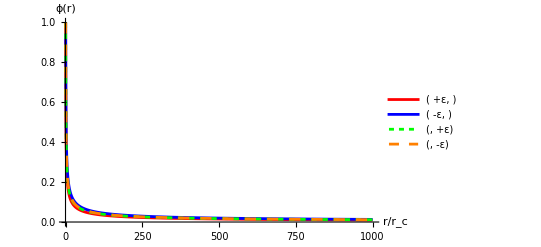

```mathematica
f5phi=Plot[
{ϕsolnlinearf5K95λ1AX[[1]][[1]][[2]]/.{C[3]->0,
A->f5K95λ1[[1]][[2]]+1/10,X->f5K95λ1[[2]][[2]]},

ϕsolnlinearf5K95λ1AX[[1]][[1]][[2]]/.{C[3]->0,
A->f5K95λ1[[1]][[2]]-1/10,X->f5K95λ1[[2]][[2]]},

ϕsolnlinearf5K95λ1AX[[1]][[1]][[2]]/.{C[3]->0,
A->f5K95λ1[[1]][[2]],X->f5K95λ1[[2]][[2]]+1/10},

ϕsolnlinearf5K95λ1AX[[1]][[1]][[2]]/.{C[3]->0,
A->f5K95λ1[[1]][[2]],X->f5K95λ1[[2]][[2]]-1/10}

},{r,0,10^3},PlotRange->{All,{0,1}},
PlotStyle->{Red,Blue,Directive[Green,Dashing[0.01]],Directive[Orange,Dashing[0.02]]},
PlotLegends->{Style["( +ε, )",Black],Style["( -ε, )",Black],Style["(, +ε)",Black],Style["(, -ε)",Black]},
AxesLabel->{Style["r/r_c",Black,14],Style["ϕ(r)",Black,14]},AxesStyle->Directive[Black, 14,Thickness[0.005]]]
```

```mathematica
insetf5phi=Plot[
{ϕsolnlinearf5K95λ1AX[[1]][[1]][[2]]/.{C[3]->0,
A->f5K95λ1[[1]][[2]]+1/10,X->f5K95λ1[[2]][[2]]},

ϕsolnlinearf5K95λ1AX[[1]][[1]][[2]]/.{C[3]->0,
A->f5K95λ1[[1]][[2]]-1/10,X->f5K95λ1[[2]][[2]]},

ϕsolnlinearf5K95λ1AX[[1]][[1]][[2]]/.{C[3]->0,
A->f5K95λ1[[1]][[2]],X->f5K95λ1[[2]][[2]]+1/10},

ϕsolnlinearf5K95λ1AX[[1]][[1]][[2]]/.{C[3]->0,
A->f5K95λ1[[1]][[2]],X->f5K95λ1[[2]][[2]]-1/10}

},{r,0,2},PlotRange->{All,{0,2}},
PlotStyle->{Red,Blue,Directive[Green,Dashing[0.01]],Directive[Orange,Dashing[0.02]]},AxesLabel->{Style["r/r_c",Black,12],Style["ϕ(r)",Black,12]},AxesStyle->Directive[Black,12],ImageSize->Small];

f5phi=Show[f5phi,Epilog->{Inset[Framed[insetf5phi,FrameStyle->Black,RoundingRadius->1],Scaled[{0.6,0.6}],(*inset location in main plot*)Center,Scaled[{0.95,0.95}]   (*inset size relative to main plot*)]}]

Export["C:\\Users\\Aiver\\Documents\\4th Year\\Physics 199\\Thesis Revision\\Figures\\f5phi.pdf",f5phi]
```

-Graphics-

C:\Users\Aiver\Documents\4th Year\Physics 199\Thesis Revision\Figures\f5phi.pdf

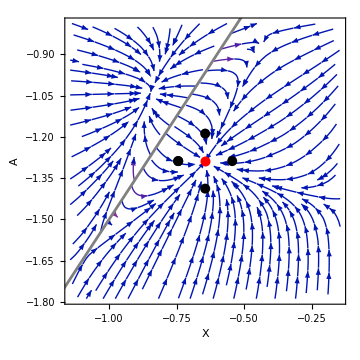

C:\Users\Aiver\Documents\4th Year\Physics 199\Final Thesis Tex\figures\f5withoffsetpoints.pdf

```mathematica
f5withoffsetpoints=Show[StreamPlot[{dΧdr/. {K->9/5,λ->1},dAdr/. {K->9/5,λ->1}},{x,f5K95λ1[[1]][[2]]-0.5,f5K95λ1[[1]][[2]]+0.5},{y,f5K95λ1[[2]][[2]]-0.5,f5K95λ1[[2]][[2]]+0.5},FrameLabel->{Style["X",Black,12],Style["A",Black,12]},FrameStyle->Black],

Graphics[{Red,PointSize[0.02],Point/@{{f5K95λ1[[1]][[2]],f5K95λ1[[2]][[2]]}},Red,FontSize->14,Text["",{f5K95λ1[[1]][[2]],f5K95λ1[[2]][[2]]},{1,1}]}],Plot[3/2 x,{x,-5,5},PlotStyle->Gray],
Graphics[{Black,PointSize[0.02],Point/@{{f5K95λ1[[1]][[2]]+1/10,f5K95λ1[[2]][[2]]}},Red,FontSize->14}],

Graphics[{Black,PointSize[0.02],Point/@{{f5K95λ1[[1]][[2]]-1/10,f5K95λ1[[2]][[2]]}},Red,FontSize->14}],

Graphics[{Black,PointSize[0.02],Point/@{{f5K95λ1[[1]][[2]],f5K95λ1[[2]][[2]]-1/10}},Red,FontSize->12}],

Graphics[{Black,PointSize[0.02],Point/@{{f5K95λ1[[1]][[2]]-1/10,f5K95λ1[[2]][[2]]}},Red,FontSize->12}],

Graphics[{Black,PointSize[0.02],Point/@{{f5K95λ1[[1]][[2]],f5K95λ1[[2]][[2]]+1/10}},Red}],

ImageSize->Medium,Background->White]

Export["C:\\Users\\Aiver\\Documents\\4th Year\\Physics 199\\Final Thesis Tex\\figures\\f5withoffsetpoints.pdf",f5withoffsetpoints]
```

```mathematica
(*αsolnlinearfpointsK95λ1plots=GraphicsGrid[{{αsolnlinearf3K95λ1plots},{αsolnlinearf4K95λ1plots},{αsolnlinearf5K95λ1plots}}]

Export["C:\\Users\\Aiver\\Documents\\4th Year\\Physics 199\\Final Thesis Tex\\figures\\αsolnlinearfpointsK95λ1plots.pdf",αsolnlinearfpointsK95λ1plots]*)
```

```mathematica
(*ϕsolnlinearfpointsK95λ1plots=GraphicsGrid[{{ϕsolnlinearf3K95λ1plots},{ϕsolnlinearf4K95λ1plots},{ϕsolnlinearf5K95λ1plots}}]

Export["C:\\Users\\Aiver\\Documents\\4th Year\\Physics 199\\Final Thesis Tex\\figures\\ϕsolnlinearfpointsK95λ1plots.pdf",ϕsolnlinearfpointsK95λ1plots]*)
```

```mathematica
{c1K95Xminus65Aminus1,c2K95Xminus65Aminus1}=(Solve[(Xsolnf3K95λ1manual==-6/5/.{r->0})&&(Asolnf3K95λ1manual==-1/.{r->0}),{C[1],C[2]}]//Simplify)[[1]]
```

{C[1]→(-73225+6407 √145)/177480,C[2]→-719/1224-6407/(1224 √145)}

```mathematica
Asolnf3K95λ1c1c2dim=Asolnf3K95λ1manual/.{c1K95Xminus65Aminus1,c2K95Xminus65Aminus1}/.r->Log[r]//Simplify
```

((-73225+6407 √145) r^((43339-3551 √145+√(1364889170-113344450 √145))/(102 (-341+28 √145))))/177480-((104255+6407 √145) r^(-(-43339+3551 √145+√(1364889170-113344450 √145))/(102 (-341+28 √145))))/177480

```mathematica
αsolnf3K95λ1c1c2dim=DSolve[r α'[r]==Asolnf3K95λ1c1c2dim,α[r],r][[1]][[1]][[2]]
```

((-341+28 √145) r^(-(-43339+3551 √145+√(1364889170-113344450 √145))/(102 (-341+28 √145))) ((104255+6407 √145)/(-43339+3551 √145+√(1364889170-113344450 √145))-((73225-6407 √145) r^((√(1364889170-113344450 √145))/(51 (-341+28 √145))))/(43339-3551 √145+√(1364889170-113344450 √145))))/1740+C[1]

General::munfl: Exp[-7347.] is too small to represent as a normalized machine number; precision may be lost.

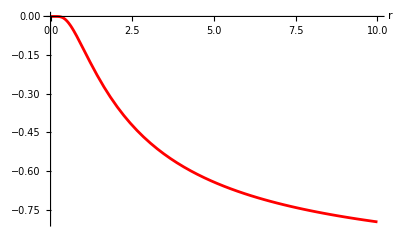

```mathematica
Show[Plot[-Exp[2*αsolnlinearf3K95λ1manual[[1]][[1]][[2]]/.{C[1]->0,C[2]->1,C[3]->0}],{r,0,10},PlotStyle->Red],
Plot[Exp[2*γsolnlinearf3K95λ1manual/.{C[1]->0,C[2]->1,C[3]->0}],{r,0,10},PlotStyle->Blue],PlotRange->Full,Background->White,AxesStyle->Black,AxesLabel->{Style["r",Black,12],Style["",Black,12]}]
```

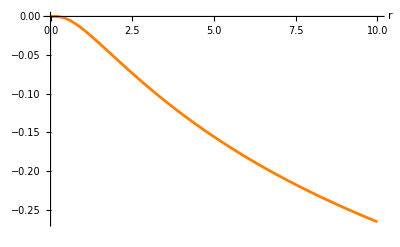

```mathematica
Show[Plot[-Exp[2*αsolnlinearf4K95λ1manual[[1]][[1]][[2]]/.{C[1]->0,C[2]->1,C[3]->0}],{r,0,10},PlotStyle->Orange],
Plot[Exp[2*γsolnlinearf4K95λ1manual/.{C[1]->0,C[2]->1,C[3]->0}],{r,0,10},PlotStyle->Green],PlotRange->Full,Background->White,AxesStyle->Black,AxesLabel->{Style["r",Black,12],Style["",Black,12]}]
```

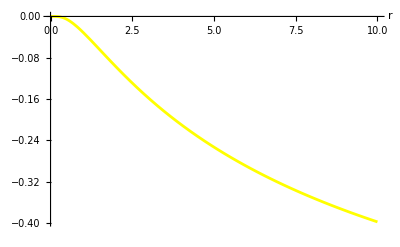

```mathematica
Show[Plot[-Exp[2*αsolnlinearf5K95λ1manual[[1]][[1]][[2]]/.{C[1]->0,C[2]->1,C[3]->0}],{r,0,10},PlotStyle->Yellow],
Plot[Exp[2*γsolnlinearf5K95λ1manual/.{C[1]->0,C[2]->1,C[3]->0}],{r,0,10},PlotStyle->Magenta],PlotRange->Full,Background->White,AxesStyle->Black,AxesLabel->{Style["r",Black,12],Style["",Black,12]}]
```

```mathematica
af3K95λ1=JacobianYf3[[1]][[1]]/.{K->9/5,λ->1}//Simplify;
bf3K95λ1=JacobianYf3[[1]][[2]]/.{K->9/5,λ->1}//Simplify;
cf3K95λ1=JacobianYf3[[2]][[1]]/.{K->9/5,λ->1}//Simplify;
df3K95λ1=JacobianYf3[[2]][[2]]/.{K->9/5,λ->1}//Simplify;
```

```mathematica
Asolnf3K95λ1=(DSolve[{X'[r]==af3K95λ1 X[r]+bf3K95λ1 A[r] ,(A'[r]==cf3K95λ1 X[r]+cf3K95λ1 A[r] )},{X[r],A[r]},r]//Simplify)[[1]][[1]][[2]];
Xsolnf3K95λ1=(DSolve[{X'[r]==af3K95λ1 X[r]+bf3K95λ1 A[r] ,(A'[r]==cf3K95λ1 X[r]+cf3K95λ1 A[r] )},{X[r],A[r]},r]//Simplify)[[1]][[2]][[2]];
```

```mathematica
αsolnlinearf3K95λ1=DSolve[r α'[r]==Asolnf3K95λ1,α[r],r];
```